```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=StringSplit[Import["movie_lines.tsv","Text"],{"\t","\n"}];
lines=StringReplace[Partition[data,5][[All,-1]],{"\""->""}];
linesJoined=StringJoin[Riffle[lines," "]];
sentences=TextCases[linesJoined,"Sentence"];
quoraquestions=SemanticImport["train.csv"];
quora=RandomSample[Join[quoraquestions[[All,5]],quoraquestions[[All,4]]],26654];
validChars = {"\t", "\n", " ", "!", "\"", "#", "$", "%", "&", "'", "(", ")", "*", "+", ",", "-", ".", "/", "0", "1", "2", "3", "4", "5", "6", 
    "7", "8", "9", ":", ";", "<", "=", ">", "?", "@", "A", "B", "C", "D", "E", "F", "G", "H", "I", "J", "K", "L", "M", "N", "O", "P", "Q", "R", 
    "S", "T", "U", "V", "W", "X", "Y", "Z", "[", "\\", "]", "^", "_", "`", "a", "b", "c", "d", "e", "f", "g", "h", "i", "j", "k", "l", "m", 
    "n", "o", "p", "q", "r", "s", "t", "u", "v", "w", "x", "y", "z", "{", "|", "}", "~"}; 
wikiSimport=Import["wikisentences1.mx"];
wikiS = StringDelete[wikiSimport, Except[validChars]];
questions=Join[Normal[quora],Select[sentences,StringContainsQ[#,"?"]&]];
questionsWithoutQuestions = StringReplace[questions,{"?"->"."}];
normalLines=Join[wikiS,RandomSample[Complement[sentences,questions][[80;;64213]],19653]];
```

```mathematica
trainingqs=Thread[#->"Question"]&/@questionsWithoutQuestions;
trainingnotqs=Thread[#->"Not a Question"]&/@normalLines;
trainingJoined=Join[trainingqs,trainingnotqs];
training=RandomSample[trainingJoined,17000];
validationset=RandomSample[Complement[trainingJoined,training],1700];
```

```mathematica
in=NetExtract[NetModel["Wolfram English Character-Level Language Model V1"],{"Input","Encoding"}]
```

{	,
, !"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\]^_`abcdefghijklmnopqrstuvwxyz{|}~,Automatic}

```mathematica
testset1=RandomSample[Complement[trainingJoined,validationset,training],1700]
```

{Simple choices might include what to eat for dinner or what to wear on a Saturday morning  choices that have relatively low-impact on the chooser's life overall.→Not a Question,The older generation won't have any problem with it.→Not a Question,How pancreatic cancer is treated.→Question,I feel like they'd do anything to keep their -- I can paint anywhere.→Not a Question,Big step.→Not a Question,What'd she say.→Question,Nine.→Question,Why would they look for you.→Question,I do not know the password of my laptop. How will I get the files back.→Question,I lost the key for those cuffs.→Not a Question,Did it.→Question,What should I do to become a faster runner within 15 days.→Question,What about my movie rights.→Question,Alternatively, it can be defined as the use of weapon systems to create a specific lethal or nonlethal effect on a target.→Not a Question,I would rather we all stay-- Don't stop just slow down.→Not a Question,I'm shipping out sooner than I thought.→Not a Question,You're saying I have no choice.→Not a Question,Are Australians homophobic and racist.→Question,In the English language it is translated as Anthony, and has some female derivatives:→Not a Question,I thought your parents were in Italy.→Not a Question,How someone strong like you scared from a message.→Question,What would you do if you liked someone and now that person seems to have fallen out of love with you and wants to be your friend.→Question,Answer the phone.→Not a Question,Can an Indian woman who doesn't hail from a political family ever become prime minister. How.→Question,How do I improve my vocabulary and fluency in english daily.→Question,Big fan.→Not a Question,Margret may refer to -
1410 Margret, an asteroid
SS Margret, a Norwegian steamship in service 1994-06/18
Margret Grebowicz, Polish philosopher, author, and professor→Not a Question,What is your 6th least favourite type of fruit.→Question,Sounds good Talby.→Not a Question,They were jealous of him.→Not a Question,Cause he was a liar.→Not a Question,This is a completely different situation from when two different counts each allege the same offence, which is sometimes wrongly referred to as duplicity.→Not a Question,What's more prestigious: being the PhD student of a famous professor at a state school or being a PhD student in math at any top Ivy League school.→Question,A number of primarily neo-Assyrian and Christian native Mesopotamian states existed between the 1st century BC and 3rd century AD, including Adiabene, Osroene, and Hatra.→Not a Question,She.→Not a Question,Each community (monastery, priory or abbey) within the order maintains its own autonomy, while the order itself represents their mutual interests.→Not a Question,It focuses on the following aspects of viruses: their structure, classification and evolution, their ways to infect and exploit host cells for reproduction, their interaction with host organism physiology and immunity, the diseases they cause, the techniques to isolate and culture them, and their use in research and therapy.→Not a Question,How good is the eyesight of a groundhog. Are they even capable of seeing their shadows.→Question,Is it radical for you to have a hand in shaping your future and the future of your children.→Question,You see what's hanging on the wall.→Question,The cheetah is characterised by a slender body, deep chest, spotted coat, small rounded head, black tear-like streaks on the face, long thin legs and long spotted tail.→Not a Question,What are you communist.→Question,What are the differences between the novel Anna Karenina and the 2012 movie adaptation.→Question,Are you a giraffe.→Question,What are the easiest ways to earn money online.→Question,The first-person perspective distinguishes self-hood from personal identity.→Not a Question,Why are there no car sharing vehicles at airports late at night, while they are plentiful during the day.→Question,It may be addressed to the audience expressly (in character or out) or represent an unspoken thought.→Not a Question,What are examples of positive and negative feedback.→Question,Fry generally stay near where they were spawned for about a year before moving on.→Not a Question,It refers to the mobile phone being used outside the range of its home network and connects to another available cell network.→Not a Question,What happen when we die.→Question,What is the best VPN service for Spain.→Question,I can't give you wealth...  ...but we can have a little family of our own.→Not a Question,Is the concept of race still relevant today.→Question,Yeah one of them's out.→Not a Question,In the United States, professional rodeos are governed and sanctioned by the Professional Rodeo Cowboys Association (PRCA) and Women's Professional Rodeo Association (WPRA), while other associations govern children's, high school, collegiate, and senior rodeos.→Not a Question,On your marks...→Not a Question,Who is dead.→Question,Is the difference between glasses with prescription lenses and glasses with plain glass lenses readily noticeable.→Question,The neighbouring town of Devonport became a strategic Royal Naval shipbuilding and dockyard town.→Not a Question,It is known as the "Constitution State", the "Nutmeg State", the "Provisions State", and the "Land of Steady Habits".→Not a Question,When are the next MacBook Airs coming out.→Question,My credit card was used for fraud transactions. I have blocked it. As transactions were not authorized, they didn't go through. What should I do next.→Question,I should have suspectcd when I heard that 'Doctor.'  I thought it was your father.→Not a Question,Being his son all you had to do was breathe to graduate here.→Not a Question,I have lost my hall ticket of PGCET 2016 and I am unable to get it anywhere online where can I download it back.→Question,What universities does Hill International recruit new grads from. What majors are they looking for.→Question,Physical cosmology is studied by scientists, such as astronomers and physicists, as well as philosophers, such as metaphysicians, philosophers of physics, and philosophers of space and time.→Not a Question,How can he give you monk's vows if he has not kept them himself.→Question,This is sometimes referred to as 'metalexicography'.→Not a Question,Why aren't Singaporeans proud of speaking their own national language.→Question,Which is a good solar panel installation provider near Meadow Vista, California CA.→Question,I got others.→Not a Question,No calls.→Question,Is Pokémon GO good or bad for mobility.→Question,Hold it like this.→Not a Question,Charley may refer to:→Not a Question,He gets as much as he wants.→Not a Question,How do I use the word and idiom mentioned below.→Question,Where's he now.→Question,In the  Book of Genesis, the biblical patriarch Jared () was the sixth link in the ten pre-flood generations between Adam and Noah; he was the son of Mahalaleel and the father of Enoch, and lived 962 years (per Genesis 5:18).→Not a Question,But what does concern me is the guns you had.→Not a Question,Mommy's coming baby!→Not a Question,Wain can also be a verb, to carry or deliver, and has other meanings.→Not a Question,And again.→Not a Question,The most common example of this phenomenon is the "Is the glass half empty or half full?" situation.→Not a Question,He seems like he thrives on danger What makes you think he'll do it.→Question,What were you doing at Finlay's this morning.→Question,Which musical instrument can I learn to play within one month.→Question,He's a stereo salesman.→Not a Question,Pretty good name for him isn't it.→Question,Mother.→Question,Why is it believed that one should not take a bath just after having food.→Question,Why in the world would I want to hook up a bunch of red black and green flag-waving pseudo revolutionairies.→Question,Stanley Hall and Arthur Allin described a "tickle" as two different types of phenomena.→Not a Question,How's she doing.→Question,My fax said have a good fright.→Not a Question,What d'you mean.→Question,Have you ever cleaned your apartment.→Question,uberculin was discovered in 1890 by Robert Koch.→Not a Question,How did he do that.→Question,All I know is that you're losing your bank and.97 She was wasn't she.→Question,Why don't you ask your chief detective.→Question,Often, this is done in an attempt to dissuade others from going in ("crossing the picket line"), but it can also be done to draw public attention to a cause.→Not a Question,For example, from various perspectives in Christianity, Judaism, and Islam it is considered an attribute that implies that a person's actions are justified, and can have the connotation that the person has been "judged" or "reckoned" as leading a life that is pleasing to God.→Not a Question,Who were the ones you didn't write down from.→Question,Seinfeld (TV series): Why is Jerry always so pissed off with Newman.→Question,The first photosynthetic organisms probably evolved early in the evolutionary history of life and most likely used reducing agents such as hydrogen or hydrogen sulfide, rather than water, as sources of electrons.→Not a Question,You've been in this house for a while.→Question,In some countries, it is known as the vestry.→Not a Question,During that period it also conducted thirteen "Enlarged Plenums" of its governing Executive Committee, which had much the same function as the somewhat larger and more grandiose Congresses.→Not a Question,And you believed him.→Question,Hence, there is the possibility that what appears as entertainment may also be a means of achieving insight or intellectual growth.→Not a Question,How do I prepare for GATE without coaching.→Question,Although the first woman flew into space in 1963, very early in crewed space exploration, it would not be until almost twenty years later that another flew.→Not a Question,This can prepare them for the temporary increases or decreases in labour requirements and inventory as demand for their product or service fluctuates over certain periods.→Not a Question,Miss Ella Mae set you up didn't she.→Question,How do you become a successful day trader.→Question,In what ways can I convince my parents for a love marriage.→Question,What are your views on Sushma Swaraj's address in UNGA 2016.→Question,The name also suggests a first impression, or something that precedes actual flirting.→Not a Question,In the early days of pre-hospital emergency services, pressure cycled devices like the Pulmotor were popular but yielded less than satisfactory results.→Not a Question,I start fires when I'm angry.→Not a Question,Take-out or takeout (in North AmericaU.S. and Canadaand the Philippines); carry-out (in some dialects in the U.S. and Scotland); take-away (in the United Kingdom other than Scotland, Australia, South Africa, and Ireland), takeaways (in New Zealand), parcel (in Indian and Pakistani English), refer to prepared meals or other food items, purchased at a restaurant, that the purchaser intends to eat elsewhere.→Not a Question,Honeymoons (Serbian:→Not a Question,Should I take an online course.→Question,Did that last comment sound too profound to be coming outta my mouth.→Question,I'm fine sir.→Not a Question,The most common cause is excessive body weight and insufficient exercise.→Not a Question,Pretending or Pretend may refer to:
Role-playing, refers to the changing of one's behaviour to assume a role, either unconsciously to fill a social role, or consciously to act out an adopted role
"→Not a Question,Had to let her go.→Not a Question,It begins with a young man, Candide, who is living a sheltered life in an Edenic paradise and being indoctrinated with Leibnizian optimism by his mentor, Professor Pangloss.→Not a Question,You mean he doesn't work for you.→Question,Why do dogs lick.→Question,What is your review of A Flying Jatt (2016 movie).→Question,You wake up every night sheets soaking the same nightmare over and over..→Not a Question,Boatman may refer to:→Not a Question,Some people order furniture upholstered in plain muslin with the intention of using slipcovers only.→Not a Question,I think you underestimate my station in this office and overrate your own.→Not a Question,In the years since the publication of his Les Propheties, Nostradamus has attracted a large number of supporters, who, along with much of the popular press, credit him with having accurately predicted many major world events.→Not a Question,Who are you. Where did you come from. Where are you going.→Question,Should I block third-party cookies.→Question,I'm engaged to Brad just the same as Betty Monroe was to Ralph Hapschatt.→Not a Question,I can't stand this place anymore.→Not a Question,How is that Wally doing.→Question,How do I handle the loss of a pet.→Question,It is rare in the developed world due to widespread vaccination.→Not a Question,These may be used in anti-aging lotions, which can also be classified as a cosmetic in many cases, and may contain fragrances.→Not a Question,What's her name.→Question,My guinea pig has been sneezing. Do I need to worry about his health.→Question,Although these insects are often called "white ants", they are not ants.→Not a Question,Why don't we feel or hear blood flowing in our veins, and our heart pumping blood.→Question,Let me see that wallet.→Not a Question,He's right on top of us.→Not a Question,It was different...→Not a Question,When the Duke of Courland brought fourteen lackeys each with bags of florins and challenged our bank to play against the sealed bags what did we ask.→Question,Which one is Mantan again.→Question,I want to be an IAS officer after completing my MBBS degree. What is the best optional subject I should choose for the exam.→Question,What is the best site to learn how to code.→Question,What is your favorite alcoholic beverage, and why.→Question,What are some charts/graphs that show rapid depletion of Earth's resources.→Question,In 1892, he was appointed as Home Secretary in Gladstone's fourth ministry, remaining in the post until the Liberals lost the 1895 election.→Not a Question,In the United Kingdom, 5,350 tanning salons were in operation in 2009.→Not a Question,But later on after Momma died and Daddy wasn't doin' nothin' but drinkin' I sure would of been glad for a little rabbit stew.→Not a Question,Eggplant is the common name in North America, Australia and New Zealand; in British English, it is aubergine, and in South Asia and South Africa, brinjal.The fruit is widely used in cooking.→Not a Question,So you're going into the Army.→Question,His army starves.→Not a Question,Which Indian city has the best nightlife.→Question,Gotta be in person.→Not a Question,You leave something out.→Question,Reiben what's the matter with you.→Question,Exceptions are the Royal Horse Artillery and the US Cavalry, where a troop is a subunit comparable to an infantry company or artillery battery.→Not a Question,Along with the axe, knife and club, it is one of the earliest and most important tools developed by early humans.→Not a Question,Adolescence (from Latin adolescere, meaning 'to grow up') is a transitional stage of physical and psychological development that generally occurs during the period from puberty to legal adulthood (age of majority).→Not a Question,Has Google ever hired anybody who is 40 years old as a software engineer.→Question,In North America, the term "hibachi" refers to a small cooking stove heated by charcoal (called shichirin in Japanese) or to an iron hot plate (called teppan in Japanese) used in teppanyaki restaurants.→Not a Question,Often, land organisms will have separate olfaction systems for smell and taste (orthonasal smell and retronasal smell), but water-dwelling organisms usually have only one system.→Not a Question,You outta be ashamed.→Not a Question,His statue of Zeus at Olympia was one of the Seven Wonders of the Ancient World.→Not a Question,Can I be excused.→Question,What was the Great Depression.→Question,It comes from the Old French official (12th century), from the Latin officialis ("attendant to a magistrate, public official"), the noun use of the original adjective officialis ("of or belonging to duty, service, or office") from officium ("office").→Not a Question,I'll get the number changed.→Not a Question,Bunch of goddamn adrenaline junkies.→Not a Question,The study of disappointmentits causes, impact, and the degree to which individual decisions are motivated by a desire to avoid itis a focus in the field of decision analysis, as disappointment is, along with regret, one of two primary emotions involved in decision-making.→Not a Question,Now I want you to go work the drop car okay Angelo.→Question,Uh a lot of his talk is pretty goofy.→Not a Question,What are your plans.→Question,Within each papilla are hundreds of taste buds.→Not a Question,The guy with the Datsun.→Question,A revolution or revolt is an attempt to fundamentally change an organizational structure in a relatively short period of time.→Not a Question,Is (2^1023)-1 prime.→Question,Miss what.→Question,You converted HER.→Not a Question,Jesus Christ Earl...what are we doing....→Question,Lovely isn't it.→Question,In universities with graduate schools, professors may mentor and supervise graduate students conducting research for a thesis or dissertation.→Not a Question,What should I do after btech (mechanical engg) GATE, IES or CAT . Right now I am pursuing SSC CGL coaching but dont know what to do after it.→Question,The lung, the "pump" must produce adequate airflow and air pressure to vibrate vocal folds.→Not a Question,Where's the rest.→Question,We ain't here to talk about that shit.→Not a Question,How can someone move one eye without the other.→Question,The hertz (symbol: Hz) is the derived unit of frequency in the International System of Units (SI) and is defined as one cycle per second.→Not a Question,Would God make you blind for watching porn.→Question,The gunfire did that.→Not a Question,Why do you wish to sail west.→Question,What is the best place for a honeymoon in February.→Question,I stopped taking your advice a long time ago or did you forget.→Question,Should skin feel sticky after applying moisturizer.→Question,Am I correct in my assumption you fish-faced enemy of the people.→Question,Have you got it.→Question,We'll do it your way.→Not a Question,Prickles occur all over the plant  on the stem and flat parts of leaves.→Not a Question,Did you talk to the police in East Proctor.→Question,Rhizocephala, fish lice, tongue worms) and some are sessile (e.g. barnacles).→Not a Question,That doesn't interest me Doctor.→Not a Question,The name comes from the ancient Roman Senate (Latin:→Not a Question,(pronounced [ferrari]) is an Italian luxury sports car manufacturer based in Maranello.→Not a Question,Why didn't his niece slap your face.→Question,No no let me go on before you get the wrong idea.→Not a Question,Now I'm being totally honest with you.→Not a Question,You fucking freaked out movie nut psychos..→Not a Question,Oskar there are twelve hundred people who are alive because of you.→Not a Question,Do you mean to tell me you didn't get it on.→Question,And that's how you want to live your life is it.→Question,Who killed Sirius Black in Harry Potter.→Question,What do White Americans think of Islam.→Question,Put it back in your pocket and hold tight to it--and someday you might grow into a worthiness ye lack now.→Not a Question,China cosmetic companies.→Question,What did you do with it.→Question,But what does the script say.→Question,Lyle.→Question,Is a broken family a good family.→Question,Which is correct, Tamil or Tamizh.→Question,A rhombus with right angles is a square.→Not a Question,What are you doing on the fourth floor.→Question,The prisoners in Guantnamo Bay are referred to as "detainees".→Not a Question,In Israel, it is still commonly used as a masculine given name.→Not a Question,What are the pros and cons of making yourself throw up.→Question,Do you have any tips for coping with anxiety.→Question,I'm taking my prisoner back to jail.→Not a Question,Is it her that's bothering you--or your gardener.→Question,What is the status of BBA of Chandigarh University Chandigarh.→Question,I am the Co-ordinator in this show and you will answer the questions that I ask you understand.→Question,In 1868 a Russian settlement was established on the site of the fortress under its original name, "Pishpek".→Not a Question,Should I register for CPT 2017 now or later.→Question,Of these three types, some formulas belonging to the tube curare are the most toxic, relative to their LD50 values.→Not a Question,Is it true that Voldemort and Harry Potter are cousins.→Question,Can I become pregnant even when using condoms.→Question,What is there to do at Yosemite National Park.→Question,Fresh squash tomatoes some okra butter beans.→Not a Question,How can you increase your stamina before running.→Question,If there were an Oscar for ""best romantic line in a movie,"" which line would win it.→Question,The rate of drowning in populations around the world varies widely according to their access to water, the climate, and the national swimming culture.→Not a Question,In some areas, agricultural land is protected so that it can be farmed without any threat of development.→Not a Question,The American.→Question,You freakin.→Question,No you listen.→Not a Question,I'm twenty-five grand over budget on the latest Bunnysitter cartoon and it's all because that rabbit can't keep his mind on his work.→Not a Question,Make anyone cry today.→Question,A monopoly (from Greek  mnos ["alone" or "single"] and  plen ["to sell"]) exists when a specific person or enterprise is the only supplier of a particular commodity.→Not a Question,Truthiness - a quality characterizing a "truth" that a person making an argument or assertion claims to know intuitively.→Not a Question,Late.→Question,Paul.→Not a Question,You're not having lunch.→Question,Thy love read by rote and could not spell.→Not a Question,Bad enough to kill for it.→Question,In addition to the general-purpose hand-held flashlight, many forms have been adapted for special uses.→Not a Question,Sleepers is a 1996 American legal crime drama film written, produced, and directed by Barry Levinson, and based on Lorenzo Carcaterra's 1995 novel of the same name.→Not a Question,Personally they are of no interest to me I'd rather sell weapons..but I have a customer...→Not a Question,Where do you want to go.→Question,Didn't make it to Canada.→Not a Question,Why does dehydration cause a burning sensation when urinating.→Question,Don't that get kind of expensive Cap'n.→Question,Would you like a tranquilizer.→Question,She has an awful toothache look at her jaw it's all swollen.→Not a Question,Major figures in linguistics include Ferdinand de Saussure and Noam Chomsky.→Not a Question,How can I lose an extreme amount of weight.→Question,The Jotter was the preferred pen of President John F. Kennedy→Not a Question,What is the best weekend escapade from Pune.→Question,Was World War 2 a fake to boost the economies of countries, and also to boost industries in less populated areas.→Question,Are the Illumaniti real. Do they really own the world.→Question,Specific forces have associated potentials, including the Coulomb potential, the van der Waals potential, the Lennard-Jones potential and the Yukawa potential.→Not a Question,How the shit are ya.→Question,When these psychoactive substances are used for religious, shamanic, or spiritual purposes, they are termed entheogens.→Not a Question,Gelbvieh were originally known as red-yellow Franconian cattle and were developed from several local breeds.→Not a Question,What is an oil fund.→Question,You don't have to feel any way about it.→Not a Question,How is the GATE paper pattern by IISc Bangalore different from the IITs for the computer science branch.→Question,Come on move it!→Not a Question,How do autonomous car work.→Question,He'll get them to reopen the bastard.→Not a Question,Spermicide is a contraceptive substance that destroys sperm, inserted vaginally prior to intercourse to prevent pregnancy.→Not a Question,We sent a mission to the Chinese National Conference.→Not a Question,Somebody's coaching her..→Not a Question,If an electric potential is applied to such a solution, the cations of the solution are drawn to the electrode that has an abundance of electrons, while the anions are drawn to the electrode that has a deficit of electrons.→Not a Question,Such actions are used as leverage, to force the victim to act in a way contrary to their own interests.→Not a Question,For what purpose this gap in a shirt.→Question,Sines (Portuguese pronunciation: [sin()]) is a Portuguese city of Setbal District, the Alentejo region and subregion of the Alentejo coast, with about 18,298 inhabitants (2015 INE).→Not a Question,Please have a seat.→Not a Question,There is lately come to Berlin a gentleman in the service of the Empress Queen who calls himself the Chevalier de Belle Fast and wears the red riband and star of the pope's order of the Spur.→Not a Question,What are the function of CAG.→Question,So you believe me. ...Whaddo I do.→Question,In a formal debating contest, there are rules for participants to discuss and decide on differences, within a framework defining how they will do it.→Not a Question,I'm sorry I... yelled at you.→Not a Question,How do I date bisexual people.→Question,You've convinced me that you're a philanderer of the very first order.→Not a Question,You're good huh.→Question,It wasn't a lunatic.→Not a Question,He'll be back.→Not a Question,Rose, Rose, Rose, you poor miserable little child, don't you know I love you.→Question,You don't have a plan.→Not a Question,Sometimes they develop from a mole with concerning changes including an increase in size, irregular edges, change in color, itchiness, or skin breakdown.→Not a Question,Castrated males are called "wethers".→Not a Question,You must realize that we've found the Main Nerve.→Not a Question,How come when Ron says ""eat slugs"" in Chamber of Secrets, it works as an actual curse.→Question,WHAAAATT.→Question,It ranked No. 64 on the Fortune Global 500 in 2017 and No. 33 on the 2016 edition of the Forbes Global 2000 list of largest public companies.Nestl's products include baby food, medical food, bottled water, breakfast cereals, coffee and tea, confectionery, dairy products, ice cream, frozen food, pet foods, and snacks.→Not a Question,Bit of a pervert eh.→Question,One person says something to the other and that's how it starts..→Not a Question,Drumstick can mean:
Drum stick, a tool for playing drums
Drumstick (vegetable)
Drumstick (frozen dairy dessert), a brand of frozen dairy dessert
Drumstick (poultry), the leg of a bird
Drumstick (video game character), a video game character found in Diddy Kong Racing
Drumstick, a chewy candy by Swizzels Matlow
Shevagyachya Shenga or Drumsticks, a 1955 Marathi language Indian film
Moringa oleifera or drumstick tree
Drumstick, the mascot of Poultryfest in Smithville, Ontario, Canada→Not a Question,basically no one has seen or heard anything.→Not a Question,What are some interesting facts about Maunakea.→Question,How many people really know what they want though.→Question,Which is the best laptop model to buy within 30k.→Question,Biologics can be composed of sugars, proteins, or nucleic acids or complex combinations of these substances, or may be living cells or tissues.→Not a Question,What are best ideas to start small business in a small city with less investment.→Question,you DO like me at all.→Question,You were sleeping.→Not a Question,Will 10 mg of Ambien cause me to have such stomach pain.→Question,Why do many men in their 40s marry younger women in their 20s in China.→Question,However, and especially under slavery in broader senses of the word, slaves may have some rights and protections according to laws or customs.→Not a Question,What's the Indian men opinion on feminism.→Question,What is the best way to choose an university.→Question,His record was not broken until Brian Lara scored 375 in 1994.→Not a Question,What will living in San Francisco be like in 2020.→Question,You're a deserter!→Not a Question,We have our drink we're out on the patio you have prepared me for it.→Not a Question,Dietrich Bonhoeffer (German: [dit bonhf]; 4 February 1906  9 April 1945) was a German pastor, theologian, anti-Nazi dissident, and key founding member of the Confessing Church.→Not a Question,In the 21st century, however, the composer's major French grand operas have begun to reappear in the repertory of numerous European opera houses.→Not a Question,because I am so very ugly...→Not a Question,worm.→Question,With one exception (the amoeboid Paulinella chromatophora), all chloroplasts can probably be traced back to a single endosymbiotic event, when a cyanobacterium was engulfed by the eukaryote.→Not a Question,What is your review of Hell (2005 movie).→Question,long legs..→Not a Question,We just want to check your pack -- Roberto what the fuck.→Question,I was doing some work here.→Not a Question,But -- do you believe in God.→Question,How does topic following on Quora work.→Question,Accounting information systems are designed to support accounting functions and related activities.→Not a Question,Which regions of Canada are hot-beds of left-wing politics. Which regions are hot-beds of right-wing politics. Why.→Question,Some species are attributed with high levels of intelligence.→Not a Question,How can I prepare for CA CPT 2017.→Question,The song features vocals from American singer Pleasure P and was produced by Jim Jonsin and Dre & Vidal.→Not a Question,Two or three years ago I would have stayed.→Not a Question,I wouldn't dance like that in private if you paid me.→Not a Question,Take a walk pal.→Not a Question,Not great.→Question,You didn't stop anywhere else.→Question,You're doing just fine.→Not a Question,Little guy's getting' hassled huh.→Question,What are the best ebooks for C++.→Question,What should I do to become a good Computer Science Engineer.→Question,The car is yours.→Not a Question,Hurry.→Not a Question,Now I know why he was such a good rope.→Not a Question,Why is there white crust in my dog's nose.→Question,Why don't you just shoot him now.→Question,So would I.→Not a Question,You have me his calendar for a couple of days I'll prove he killed Lincoln.→Not a Question,You ride me back to camp.→Question,Need some help.→Question,Thin, twig-like and brittle, they were first launched in 1968 by Rowntree's and were just one-third of the length they are now.→Not a Question,Unitarian or Unitarianism may refer to:
In Christian and Christian-derived theologies a Unitarian is a follower of, or a member of an organisation that follows, any of several theologies referred to as Unitarianism:→Not a Question,A staple is a type of two-pronged fastener, usually metal, used for joining or binding materials together.→Not a Question,Rickey is a surname or first name, and may refer to:→Not a Question,Director may refer to:→Not a Question,Clashes between communism and capitalism dominated the decade, especially in the Northern Hemisphere.→Not a Question,The pharynx is an area found in vertebrates and invertebrates, though the structure is not universally the same across all of those species.→Not a Question,However, the album's best-known track was one of the least typical of the group's catalogue:→Not a Question,What is the value of the humanities.→Question,What is the most embarrassing thing that has ever happened to you in the workplace.→Question,Like the old days Dillon.→Not a Question,Let somebody down the line clean up your mess.→Question,Kelsey (given name)→Not a Question,Murk (band), a Cuban-American house-music duo

Murk (album), its 2004 self-titled release

Murk (film) (Danish title:→Not a Question,Aussie can be used in the form of an adjective, noun, or proper noun.→Not a Question,Wilson.→Not a Question,I gave him a home a future..→Not a Question,And what's that.→Question,from a certain point of view.→Not a Question,So he drank himself into a stuper.→Question,What is the English word for ""Jomblo"".→Question,What are the career opportunities in companies after an M.Tech in aerospace engineering with a B.Tech in mechanical engineering.→Question,Chewie give me the gun.→Not a Question,I want to be with my boyfriend but he doesn't trust me what should I do.→Question,Fine then how many nights home is that.→Question,How do I calculate the equivalent resistance in this diagram.→Question,Other active ingredients in fungicides include neem oil, rosemary oil, jojoba oil, the bacterium Bacillus subtilis, and the beneficial fungus Ulocladium oudemansii.→Not a Question,They grow to around 90 cm (35 in) in length including tail.→Not a Question,The Clock People however are not a tribe rather they are a gathering of Indians from various tribes.→Not a Question,Why do parents think their kids are right.→Question,Wind speeds on Saturn can reach 1,800 km/h (1,100 mph; 500 m/s), higher than on Jupiter, but not as high as those on Neptune.→Not a Question,How do I do parsing in XML.→Question,Boulder sized clasts are found in some sedimentary rocks, such as coarse conglomerate and boulder clay.→Not a Question,Your mother was blind.→Question,Well it could be any one of them bubi; I get to see them all.→Not a Question,What about in the mean time.→Question,You know that first day when I come and he said I looked graceful like a capital letter S and called me Rosebud.→Question,How is a magnetism created.→Question,Earthy (Kenny Burrell album), 1957
Earthy (wine), a wine tasting descriptor→Not a Question,Sleep OK.→Question,How do you upgrade a MacBook Pro processor.→Question,A wide variety of materials may be worked by removal such as carving, assembled by welding or modelling, or molded or cast.→Not a Question,Been there for a long time.→Not a Question,But why did you not write home to your poor mother.→Question,Oh--a God complex I'm everywhere.→Not a Question,A rockfall or rock-fall refers to quantities of rock falling freely from a cliff face.→Not a Question,Top priority.→Not a Question,How do I cook bacon in the toaster oven.→Question,I'm sorry too.→Not a Question,The extent to which these usages still retain connotations of homosexuality has been debated and harshly criticized.→Not a Question,lagella are organelles defined by function rather than structure.→Not a Question,What is the best way to learn to write well in english.→Question,Your friend just made himself a star.→Not a Question,Is that the way you feel now.→Question,The House of Stuart, originally Stewart, was a European royal house that originated in Scotland.→Not a Question,he government policy and legal framework in which practitioners operate vary greatly from country to country, with some having both non-physician "osteopaths" and medically trained "osteopathic physicians."→Not a Question,I mean what kind of people do well at this stuff.→Question,In various other parts of symbolic programming there are only so many symbols.→Not a Question,Hoofprints and pawprints are those left by animals with hooves or paws rather than feet, while "shoeprints" is the specific term for prints made by shoes.→Not a Question,Evan you're hysterical.→Not a Question,Do you like to fill out surveys.→Question,Twombley.→Not a Question,What are the best restaurants to try when visiting Valenzuela City, Philippines. What should you try while you're there.→Question,What's that for.→Question,Captain Steubing thinks you might work for the police.→Not a Question,What is the gravity at the equator.→Question,What exams does an architecture student from India need to give to join an B.Arch course abroad.→Question,While other inventors had produced devices that could record sounds, Edison's phonograph was the first to be able to reproduce the recorded sound.→Not a Question,Introduced in 2003 as a pilot scheme and rolled out in 2007.→Not a Question,What the hell is going on here.→Question,SAAVIK UHURA UHURA LT.→Not a Question,You guys.→Question,How much food do the WWe Superstars eat.→Question,My god.→Not a Question,How did this happen.→Question,These are toxic chemicals...→Not a Question,Do virus and Bacteria have souls.→Question,Topeka's founders chose the name in 1855 because it "was novel, of Indian origin and euphonious of sound."→Not a Question,Jimmy.→Question,In medical diagnosis, pain is regarded as a symptom of an underlying condition.→Not a Question,Who's got that kinda scrilla lying around these being the worst of the times.→Not a Question,Sculpture in stone survives far better than works of art in perishable materials, and often represents the majority of the surviving works (other than pottery) from ancient cultures, though conversely traditions of sculpture in wood may have vanished almost entirely.→Not a Question,The last of the imperial Byzantine successor states, the Empire of Trebizond, would be conquered by the Ottomans eight years later in the 1461 Siege of Trebizond.→Not a Question,How do you get your pay stub if you work at McDonald's.→Question,Has Donald Trump ever committed a crime.→Question,Let me ask you something..→Not a Question,Although these theories included equations identical to those that Einstein introduced (i.e. the Lorentz transformation), they were essentially ad hoc models proposed to explain the results of various experimentsincluding the famous MichelsonMorley interferometer experimentthat were extremely difficult to fit into existing paradigms.→Not a Question,Whitewash may also refer to:
Racial whitening, or "whitewash" (branqueamento), an ideology that was widely accepted in Brazil between 1889 and 1914
Whitewashing in film, the practice of casting white actors in historically or canonically non-white character roles
Whitewash (sport), a sports game or series in which the losing person or team fails to score
Whitewash (censorship), a term for censorship
Whitewash (TV special), a 1994 HBO Family Channel
Whitewash (film), a 2013 Canadian film
Whitewash Jones, a racist caricature from the 1940s comic book Young Allies
Whitewash procedure, a legal procedure in shareholder law
"→Not a Question,Why are so many Internet companies and startups using Dutch B.V. companies.→Question,Greer may refer to:→Not a Question,A thyristor is not a proportional device like a transistor.→Not a Question,The one Nigel spoke of.→Not a Question,-- it's always bad and it's never anything but bits and pieces anyway!→Not a Question,Internationally, the order is governed by the Benedictine Confederation, a body, established in 1883 by Pope Leo XIII's Brief Summum semper, whose head is known as the Abbot Primate.→Not a Question,Did you ever stop to think of that.→Question,But how can I do that.→Question,I am in love with a girl who is married to other guy. Should we continue.→Question,So no jokes about my name.→Question,What is the solution of this math problem.→Question,What is it that Arvind Kejriwal lacks as a leader.→Question,Crochet (English: ; French: [k]) is a process of creating fabric by interlocking loops of yarn, thread, or strands of other materials using a crochet hook.→Not a Question,Going into Zimmermann's pipeline.→Not a Question,But when there's really loud noises around me...→Not a Question,What is VAR in electrical engineering. And what's its importance.→Question,What will be the next move by PM Modi to improve India.→Question,A secretary desk or escritoire is made of a base of wide drawers topped by a desk with a hinged desktop surface, which is in turn topped by a bookcase usually closed with a pair of doors, often made of glass.→Not a Question,What is the best 7 day itinerary for family with toddler to New Zealand.→Question,What's the most effective way to learn to read German.→Question,What is your score in KVPY SA 2016 (aptitude test). What is the expected cutoff.→Question,Attlee remains the longest-ever serving Leader of the Labour Party. 
First elected to the House of Commons in 1922 as the MP for Limehouse, Attlee rose quickly to become a junior minister in the first Labour minority government led by Ramsay MacDonald in 1924, and then joined the Cabinet during MacDonald's second ministry of 192931.→Not a Question,I swear to God I won't try to escape and I'll do my best to get you into Mexico.→Not a Question,A longer version of the song was previously released on their EP "Into Forever."→Not a Question,We must have bass!→Not a Question,Robin Miriam Carlsson (born 12 June 1979), known as Robyn, is a Swedish singer, songwriter and record producer.→Not a Question,Gently.→Question,In Ireland, the autumn months according to the national meteorological service, Met ireann, are September, October and November.→Not a Question,Wine writers, like Karen MacNeil, author of The Wine Bible, differentiate wine tasters from casual enthusiasts; tasters attempt to give an objective description of the wine's taste (often taking a systematic approach to tasting), casual enthusiasts appreciate wine but pause their examination sooner than tasters.→Not a Question,And he can sew, this guy, he's really skilled.→Not a Question,What is cytosol.→Question,What are the embarrassing moment of your life.→Question,What is a deferred adjudication for a speeding ticket.→Question,How do you prove tan^2 (x/2+pi/4) = 1+sinx/1-sinx.→Question,But no intention of selling them.→Not a Question,A person with a parent or sibling with alcoholism is three to four times more likely to become an alcoholic themselves.→Not a Question,It is a spring month of 29 days.→Not a Question,Constructibility or constructability may refer to:
Constructability or constructability review, a process in construction design whereby plans are reviewed by others familiar with construction techniques and materials to assess whether the design is actually buildable
Constructible strategy game, a tabletop strategy game employing pieces assembled from components→Not a Question,'Sorry about the late notice..→Not a Question,Were you insanely worried about winning that you had to cheat with the Democrats to beat Bernie.→Question,Too bad about those two German couriers wasn't it.→Question,Tell me what.→Question,Which is the most upvoted answer of Quora.→Question,I gotta use a bad word -- Whore.→Not a Question,San Francisco: Who has the best taco salad.→Question,Why is korea divided.→Question,Then there his somebody else.→Question,Why would we arrest you.→Question,Is there a possibility that we actually are existing within a programmed platform.→Question,Is there a Cydia tweak that leaves Post-it notes on your lock screen for reminders.→Question,he courtesans of East Asia, particularly those of the Japanese empire, held a different social role than that of their European counterparts.→Not a Question,No there's no evidence of a surge or spike of any kind.→Not a Question,And you don't know how they open is that what you are saying.→Question,I've reached another containment door.→Not a Question,Strader through the nightclub established a distribution network.→Not a Question,At the end of the movie Salt, the President is still alive and he knows that Liev Schreiber's character tried to kill him. So why was Salt (Angelina Jolie) worried that no one would believe her.→Question,What has happened madam to annoy your ladyship.→Question,The country across the sea.→Not a Question,Hot chocolate.→Question,Why am I doing this.→Question,How can I start a business of import/export from China, Japan etc. .→Question,Which phone should I buy under 10k.→Question,How much does a Macbook Pro cost in Singapore. Is it better to buy it in India or in foreign countries.→Question,How can I learn a language from a friend.→Question,Anything that might account for this problem.→Question,Why do dogs run away.→Question,In physics, the microscopic scale is sometimes considered the scale between the macroscopic and the quantum realm.→Not a Question,Innsbruck is an internationally renowned winter sports centre, and hosted the 1964 and 1976 Winter Olympics as well as the 1984 and 1988 Winter Paralympics.→Not a Question,What are some time-saving tips that every Facebook user should know.→Question,Must be a story there.→Not a Question,What's so great about Cadbury's bubbly version of Dairy Milk Silk.→Question,I understand from your neighbors that all [them] cats are making noise at night.→Not a Question,Where is the best institute to learn VFX.→Question,My bed.→Not a Question,Which is the most long-lasting yonex shuttlecock for state level players.→Question,What are the top restaurant chains in the world.→Question,How do zebras differ from horses.→Question,I'm a mechatronic engineering student. I'm looking for ideas for final year project.→Question,Frankfurt was a city state, the Free City of Frankfurt, for nearly five centuries, and was one of the most important cities of the Holy Roman Empire; it lost its sovereignty in 1866.→Not a Question,I just wanted What.→Question,In organic chemistry, phenols, sometimes called phenolics, are a class of chemical compounds consisting of a hydroxyl group (OH) bonded directly to an aromatic hydrocarbon group.→Not a Question,What is the logic for cracking the '2048 puzzle'.→Question,Rights are of essential importance in such disciplines as law and ethics, especially theories of justice and deontology.→Not a Question,What is the difference between bhajan and kirtan. Or are they same.→Question,Why didn't you eat last night.→Question,How does the 80/20 principle apply to life.→Question,Get your field gear take stuff for overnight.→Not a Question,What is the background of the players who play state-level cricket (Ranji Trophy, Irani Trophy, etc.) for the team of Services.→Question,Import/Export: What is the cheapest way to send a parcel from India to any other country.→Question,Maybe there's something wrong with the scumbag customers coming into your place ever think of that.→Question,Sir Garfield St Aubrun Sobers, AO, OCC (born 28 July 1936), also known as Gary or Garry Sobers, is a former cricketer who played for the West Indies between 1954 and 1974, and is widely considered to be cricket's greatest all-rounder.Born in Bridgetown, Barbados, Sobers made his first-class debut for the Barbados cricket team at the age of 16 in 1953, and his Test debut for the West Indies the following year.→Not a Question,What is the costliest United States military aircraft in history.→Question,Will the cathedral be finished soon John.→Question,Except for the period of the Commonwealth, 16491660, the Stuarts were monarchs of the British Isles and its growing empire, until the death of Queen Anne in 1714.In total, nine Stewart/Stuart monarchs ruled Scotland alone from 1371 until 1603.→Not a Question,It was based on a theatrical sketch by Fred Karno.→Not a Question,What qualities and skills separate an Engineering Manager vs. Director of Engineering vs. VP of Engineering.→Question,When will the doctor be awake.→Question,Which is a suitable inpatient drug and alcohol rehab center near Putnam County IN.→Question,What do Argentinians think of Americans.→Question,The song has become a fan favorite over the years and was often played live.→Not a Question,The legs must be goin'.→Not a Question,What is your review of Unity (user interface).→Question,We will no longer have that particular stick with which to threaten the farmers.→Not a Question,Listen to me!→Not a Question,You've done nothing but get rich off of me.→Not a Question,I can just take her right across the street to Luther's hotel.→Not a Question,It is mainly observed while sailing in waves, when the bow raises from the water and subsequently impacts on it.→Not a Question,So, to the extent perceived disgust and sadness remain, the level of disappointment also remains.→Not a Question,What's the scope after bsc in botany.→Question,What's a moral orgasm John.→Question,Resistance has developed to many previously used antibiotics and higher doses of ceftriaxone are occasionally required.→Not a Question,At two o'clock we have an appointment with none other than Roger De Bris.→Not a Question,We are concerned about more than Casablanca.→Not a Question,What is the name of plant.→Question,Should India declare war against Pakistan as they are spreading terrorism in India.→Question,How can I take over the world.→Question,What's happening here.→Question,You treated me like shit.→Not a Question,- and no rebuke at all!→Not a Question,See that down there.→Question,Jesus Christ man that microwave food will kill ya as quick as a bullet.→Not a Question,The term is commonly associated with Chinese paper lanterns.→Not a Question,Activated drotrecogin alfa, originally marketed for severe sepsis, has not been found to be helpful, and was withdrawn from sale in 2011.Disease severity partly determines the outcome.→Not a Question,Many methods are designed according to the limits of the signalling medium used.→Not a Question,Is there any one who finds css and HTML tough.→Question,The clerk.→Question,Nice to meet you Stacy.→Not a Question,Stargazer may refer to:

an observational astronomer, particularly an amateur→Not a Question,What is the significance of Miller indices.→Question,Running as a service, it allows for the detection of modifications to a file or directory.→Not a Question,And the Stones.→Question,Do you use sex toys.→Question,What are the best ways to get rid of boredom.→Question,Why don't you do things you should be doing.→Question,"flip-flop"), as an easily flipped breakfast food with the same name  hence the waffle famously used to represent President Bill Clinton in the Doonesbury comic strip.→Not a Question,Is quantum physics truly unpredictable in behaviour, or is it that humans simply don't posses the devices to predict it accurately.→Question,I will hire someone who is most qualified for this particular job.→Not a Question,It is difficult to estimate the number of recreational fishing boats.→Not a Question," Similarly, there is a long-standing rule that a person must have an insurable interest in a property or person that they wish to insure.→Not a Question,What is the cheapest online stock trading platform in Germany.→Question,So did you buy a movie.→Question,Rodeo ( or ) is a competitive sport that arose out of the working practices of cattle herding in Spain, Mexico, and later Central America, South America, the United States, Canada, Australia and New Zealand.→Not a Question,Candy, also called sweets or lollies, is a confection that features sugar as a principal ingredient.→Not a Question,Individuals construct an image of themselves, a personal identity, and present themselves in a manner that is consistent with that image.→Not a Question,They contain significantly greater quantities of the hormones prolactin, adrenocorticotropic hormone, and Leu-enkephalin, and the elements potassium and manganese.→Not a Question,So are you Pop-Sweet.→Not a Question,Synoptic is derived from the Greek words  (syn, "together") and  (opsis, "view"), and describes observations that give a broad view of a subject at a particular time.→Not a Question,None may refer to:
Zero, the mathematical concept of the quantity "none"
Empty set, the mathematical concept of the collection of things represented by "none"
none, an indefinite pronoun in the English language→Not a Question,How will scraping of 500 and 1000 rupees notes help in curbing corruption and black money.→Question,What is the best Korean dramas of all time.→Question,They are seen as items of great spiritual and political importance, only to be worn by those who have earned the right and honour through formal recognition by their people.→Not a Question,A steamroller (or steam roller) is a form of road roller  a type of heavy construction machinery used for leveling surfaces, such as roads or airfields  that is powered by a steam engine.→Not a Question,Egg Beaters, an egg substitute used in cooking
Eggbeater wind turbine
Breast drill, a type of hand drill often referred to as an "egg-beater"→Not a Question,What business and social problems does data center power consumption cause.→Question,How must the next President address homegrown Islamic terrorism.→Question,What is Hotelling’s principle.→Question,Nobody wants your theories on -- 25 kilos each huh.→Question,What in heavens' name is the Page Quora about… I have a profile etc… huh.→Question,In vertebrate anatomy, ribs (Latin: costae) are the long curved bones which form the rib cage.→Not a Question,I think your name is magic.→Not a Question,While some critics may equate separatism with religious segregation, racist segregation, or sexist segregation, most separatists argue that separation by choice may serve useful purposes and is not the same as government-enforced segregation.→Not a Question,What are the alternatives-to-Google-play-store-get-paid-apps-for-free 2017.→Question,If they do see thee they will murder thee.→Not a Question,What are the worst and funniest experiences people have had using Tinder.→Question,I'd like to ask you some questions about Tom Grunemann.→Not a Question,Does deleting my Snapchat account get rid of saved (tapped) messages in the other person's chat.→Question,How do I Get screen resolution & insert in MySQL.→Question,I mean you don't exactly have the build for a football.→Not a Question,North of Uppers is Cotton's Point, the location of former President Richard Nixon's home, La Casa Pacifica, aka "The Western White House", and the associated surfing spot of Cottons.→Not a Question,I am working in SAP hr security from 1.5 years in IBM want to switch to different company need some suggestions.→Question,Poetry (odes,  epics, etc.), prose, and performance each had a specific and calculated style that related to the theme of the story.→Not a Question,Am I boring you, Rose.→Question,How accurate is the active now status on Facebook chat.→Question,What does ""keep rocking"" mean. What are the origins of the phrase.→Question,godson for boys and goddaughter for girls).→Not a Question,How do I not worry about what others think or compare myself with them.→Question,In physical geography, a steppe (Russian: , IPA: [step]) is an ecoregion, in the montane grasslands and shrublands and temperate grasslands, savannas and shrublands biomes, characterized by grassland plains without trees apart from those near rivers and lakes.→Not a Question,The most widely used measure of aid is "Official Development Assistance" (ODA).→Not a Question,Why wouldn't Hillary Clinton choose Bernie Sanders for VP.→Question,A reader encounters them when reading texts that are centuries old.→Not a Question,A chain may consist of two or more links.→Not a Question,Evan.→Not a Question,Why should someone accept anything one is given.→Question,Hey Cobb..→Not a Question,Western artists and allegorists have often used Athena as a symbol of freedom and democracy.→Not a Question,Illusions, Madam.→Question,Most wedding ceremonies involve an exchange of marriage vows by the couple, presentation of a gift (offering, rings, symbolic item, flowers, money), and a public proclamation of marriage by an authority figure or celebrant.→Not a Question,Elongation may refer to:
Elongation (astronomy)→Not a Question,What is process state of an operating system.→Question,The last remaining werewolf must be destroyed.→Not a Question,Simptico (Gbor Szab album) an album by Gbor Szab and Gary McFarland
Simptico (The Brian Lynch/Eddie Palmieri Project album), an album by The Brian Lynch/Eddie Palmieri Project
Simpatico (The Charlatans album), an album by The Charlatans (known in the US as The Charlatans UK)
Simpatico (Velocity Girl album) an album by Velocity Girl.→Not a Question,Can shrimp consumption cause high blood pressure.→Question,I'm dressed up With no place to go.→Not a Question,Aw come on Rose I want to see what the nipple on it is like.→Not a Question,What is control 4.→Question,Since the Renaissance, Athena has become an international symbol of wisdom, the arts, and classical learning.→Not a Question,Is it possible to make Tibet an independent nation.→Question,Then we will simply alert him.→Not a Question,What is it like to be alone.→Question,Who did that.→Question,Who won the third debate.→Question,I'm a Windows Phone user and even though I have a very good camera in my Lumia 1520 I still fail to capture quality images. Suggestions.→Question,Who is or was the best Law Minister of India.→Question,What's your favorite Chinese food.→Question,Where did you hear that story.→Question,Do you love them.→Question,What was once the second largest herd is the migratory boreal woodland caribou (R. t. caribou) George River herd in Canada, with former variations between 28,000 and 385,000.→Not a Question,Commanded by French officers, it is open to French citizens, who amounted to 24% of the recruits in 2007.→Not a Question,Why are men more likely to be assholes compared to women.→Question,The Amiga is a family of personal computers introduced by Commodore in 1985.→Not a Question,Over the centuries, differences in terrain, climate and the influence of cattle-handling traditions from multiple cultures created several distinct styles of equipment, clothing and animal handling.→Not a Question,What is the University of Nevada in Reno known for.→Question,Look spare me the macho bullshit about your gun...→Not a Question,Preservation is implemented in two modes, chemical and physical.→Not a Question,How do I make life easy.→Question,The hell you think you are.→Question,You know who Muhammad was.→Question,You and the other one you're still Billy's girls.→Not a Question,The compression of the articular cartilage or flexion of the elastic cartilage generates fluid flow, which assists diffusion of nutrients to the chondrocytes.→Not a Question,Now I can't do it cause I'm tied up but we get the others to go along -- How.→Question,What is a CIO. What do CIOs do.→Question,My sister Antoinette helped him up herself and do you know what he did.→Question,Some girl that's been hanging on at every party.→Not a Question,Sighting the height of a landmark can give a measure of distance off and, held horizontally, a sextant can measure angles between objects for a position on a chart.→Not a Question,How did I get in.→Question,and increase his medication.→Not a Question,Which is the best site for free sex chats with girls.→Question,Northern England first Italy later.→Not a Question,It's a small lie but now we're sure he's playing.→Not a Question,I earn a salary of 20 lacs. For a guy with 10 years of experience in IT (database and BI) from Pune, is this salary good enough in India.→Question,Fairground most typically refers to a permanent space that hosts fairs.→Not a Question,Passion or money, what should be your goal for your first startup.→Question,Will IT companies call me for sure if I have offer letter provided by them.→Question,Sprouts can be germinated at home or produced industrially.→Not a Question,Why'd he want you.→Question,How can I setup a private server to host a website.→Question,You're not a member of his immediate family I could have you removed from the ER. Dr. Klenstein.→Not a Question,Like firing Andrew Beckett taught <u>him</u> a lesson.→Question,An' Thursday two yards from Cappoli okay.→Question,The navel (clinically known as the umbilicus, colloquially known as the belly button, or tummy button) is a hollowed or sometimes raised area on the abdomen at the attachment site of the umbilical cord.→Not a Question,Can we make it.→Question,Without treatment, symptoms may last weeks or months.→Not a Question,The words sheave and pulley are sometimes used interchangeably.→Not a Question,In the United States, the full length "locum tenens" (plural: locum tenentes) is preferred, though for some particular roles, alternative expressions (e.g., "substitute teacher") may be more commonly used.→Not a Question,If the message I sent to someone on WhatsApp is later than her last seen, how could the message be seen, as it is shown by double tick sign.→Question,Rose had a rare tropic disease and the little tubes in her that babies swim down are all stopped up she told me all about it.→Not a Question,Really Jam you tryin' to make us barf.→Question,The ship has become a cultural icon in the history of the United States.→Not a Question,If you pick up people like Larry Mitchell other people are bound to get funny ideas about you.→Not a Question,How do I recover my disabled Google account.→Question,Of course not.→Not a Question,But you <u>were</u> having anonymous sex in porno theaters in 1984 and 1985.→Question,The coagulation can be caused by adding rennet or any edible acidic substance such as lemon juice or vinegar, and then allowing it to coagulate.→Not a Question,In addition, the precise mechanism that causes a given element (image, sound, behavior, etc.) to be perceived as more or less 'amusing' than another, similar element to a particular individual is not clearly understood.→Not a Question,What is my old Gmail account.→Question,Why aren't you there right now.→Question,Fine thank you.→Not a Question,What are the top online classified websites in Europe.→Question,How do you say ""hurry up"" in Japanese.→Question,How do I get fit and get rid of body fat.→Question,Aside from the period of Japanese occupation, the United States retained sovereignty over the islands until after World War II, when the Philippines was recognized as an independent nation.→Not a Question,Some of the materials that can be used for driveways include concrete, decorative brick, cobblestone, block paving, asphalt, gravel, decomposed granite, and surrounded with grass or other ground-cover plants.→Not a Question,The term "Crusades" is also applied to other church-sanctioned campaigns, such as Albigensian Crusade against the Cathars or the Baltic Crusades.→Not a Question,You're so close to the way you're going to catch him - do you realize that.→Question,What kind of music do you like most. Jazz. Blues. This is a survey for my homework.→Question,I brought the girl remember.→Question,The Clockworks is one reason that I am here on Siwash Ridge.→Not a Question,That kiss ...→Not a Question,The stream encompasses surface and groundwater fluxes that respond to geological, geomorphological, hydrological and biotic controls.→Not a Question,Productivity (ecology), the rate of generation of biomass in an ecosystem.→Not a Question,Well how did it go.→Question,Name some poruing equipment.→Question,What's the best way to learn faster.→Question,What's your least favorite Pokémon.→Question,Fifty.→Question,In mathematics, the intersection of two or more objects is another, usually "smaller" object.→Not a Question,Throwing is used in many sports and games, particularly ball games, and in throwing sports the action is the main determiner of the outcome.→Not a Question,Thou talk'st of nothing.→Not a Question,The majority of Muslims also follow the teachings and practices of Muhammad (sunnah) as recorded in traditional accounts (hadith).→Not a Question,What are the extra features available on fyers trading platform.→Question,Give us an option on your stock and resign as president.→Not a Question,Monopolies may be naturally occurring due to limited competition because the industry is resource intensive and requires substantial costs to operate.→Not a Question,Latticework in stone or wood from the classical period is also called transenna (plural transenne).→Not a Question,The Sturmabteilung (SA; German pronunciation: [tmaptal] ( listen)), literally Storm Detachment, was the Nazi Party's original paramilitary.→Not a Question,Andy.→Not a Question,The trade union, through its leadership, bargains with the employer on behalf of union members (rank and file members) and negotiates labour contracts (collective bargaining) with employers.→Not a Question,You would.→Question,A small component of wet-haze aerosols appear to be derived from compounds released by trees, such as terpenes.→Not a Question,I wrote it.→Not a Question,Give me your score please.→Not a Question,What is the role of psychology in the spread of crimes.→Question,It's your call but you're gonna be sorry when you're in one of those everyday situations that call for a battery-operated vagina and you don't have one.→Not a Question,As a matter of fact one of my own pupils - a very young singer - told me she was - er - well!→Not a Question,The album was re-released in an expanded and re-mastered edition by Universal in May 2007.→Not a Question,Is it not so.→Question,Brady (18151869), New York City lawyer and politician
Jim Brady (baseball) (born 1936), American economist, educator, and baseball player and coach
Jim Brady (boxer), Scottish boxer of the 1930s and 1940s
Joan Brady, writer, the first woman  and the only American  to win the Whitbread Book of the Year Award for the Theory of War, lives in Oxford, England
Joan Brady, American writer of Christian novels
John Green Brady (18471918), American politician, Governor of the District of Alaska (18971906)→Not a Question,What is the smallest species of animal.→Question,In what order should I learn Java web development technologies.→Question,You got us a room so quick.→Question,To protect.→Not a Question,You're a smart boy Jeremiah.→Not a Question,A test may be administered formally or informally.→Not a Question,How should I control a fart when I am with my roomate.→Question,During the reign of Justinian I (r. 527565), the Empire reached its greatest extent after reconquering much of the historically Roman western Mediterranean coast, including North Africa, Italy, and Rome itself, which it held for two more centuries.→Not a Question,Scared at first.→Not a Question,Where's the woman.→Question,What does dun and bradstreet do.→Question,Is 37 too old to get married.→Question,Hey I'm a man aren't I.→Question,What do you think the purpose of life is.→Question,What are the things that are important in life.→Question,A grenadier (, French pronunciation: [.na.dje]; derived from the word grenade) was originally a specialized soldier, first established as a distinct role in the mid-to-late 17th century, for the throwing of grenades and sometimes assault operations.→Not a Question,Some scholars support this view, though this claim is controversial, given that the vast majority of people who entered the Gulag came out alive, with the exception of the war years.→Not a Question,I'm pretty naive.→Question,What would you do with it if you owned the domain name ecolicense.com.→Question,The migrations of Porcupine caribou herds are among the longest of any terrestrial mammal.→Not a Question,Did you decide on a runway yet.→Question,You will not come.→Question,Should I buy Amazon Echo or Google Home.→Question,A larger full-service supermarket combined with a department store is sometimes known as a hypermarket.→Not a Question,How long do you stay in the hospital after a prescription drug overdose.→Question,Equiangular polygon  a polygon with equal angles.→Not a Question,They are found on every continent except Antarctica, in every habitat on the planet that contains insect-pollinated flowering plants.→Not a Question,In music, counterpoint is the relationship between voices that are harmonically interdependent (polyphony) yet independent in rhythm and contour.→Not a Question,Which university provides the best to study medicine in Ukraine, Europe.→Question,Where did the creators of Civilization VI take the Norway soundtrack from.→Question,It's old hat for us.→Not a Question,My ex boyfriend broke up with me five times. Is he an abuser or am I the problem.→Question,A dentist, also known as a dental surgeon, is a surgeon who specializes in dentistry, the diagnosis, prevention, and treatment of diseases and conditions of the oral cavity.→Not a Question,How can I increase the traffic on my website.→Question,What'll you have Margo.→Question,Sportswear company Nike, Inc., headquartered in Beaverton, is the state's largest public corporation with an annual revenue of $30.6 billion.→Not a Question,No kidding.→Question,According to the British Longbow Society, the English longbow is made so that its thickness is at least 58 (62.5%) of its width, as in Victorian longbows, and is widest at the handle.→Not a Question,No-I can't take the time off work.→Not a Question,What the fuck are you doing here.→Question,What have you got me into.→Question,My German's a little rusty.→Not a Question,Your Honor I submit there were no complaints until Counselor began knocking on doors drumming up business.→Not a Question,In sewing and dressmaking, a ruffle, frill, or furbelow is a strip of fabric, lace or ribbon tightly gathered or pleated on one edge and applied to a garment, bedding, or other textile as a form of trimming.→Not a Question,Dinner.→Question,Which type of camber is used in a Baja ATV.→Question,I like a girl probably because I was in love with someone who looked similar to her. Should I tell her (the new girl) this thing.→Question,Dunwitty wants a Coon show.→Not a Question,In a number of ancient religions, a dying-and-rising god is a deity which dies and resurrects.→Not a Question,What's the best definition of communication.→Question,So you're going to fight fires now huh.→Question,How old are you dear.→Question,What caused the Great Depression.→Question,But what.→Question,Then it's malaria.→Question,I don't give out the details.→Not a Question,How do I enable usb debugging from boot menu if the device is freezed.→Question,How much money do Uber drivers make in Sacramento.→Question,The machine was known for its utility and efficiency for serving several agricultural uses at the same time, while saving time and effort.→Not a Question,Why are ALL my questions being marked as needing improvement.→Question,The multigene families that encode the toxins of venomous animals are actively selected on, creating more diverse toxins with specific functions.→Not a Question,Little Zee Mimms.→Question,He comes back and now he wants me to take over the family business.→Not a Question,How can I get a Xbox live membership for free.→Question,I love you Dad. ...Then go.→Not a Question,Assemblage (archaeology)→Not a Question,What distinguishes Marlboro Red cigarettes from other brands.→Question,God's permission.→Question,He's already gotta be a part of Sid's life.→Not a Question,There's nothing wrong with the antigens nothing to indicate an unusual death...→Not a Question,I don't see anything do you.→Question,I'm looking at buying a new SUV/Crossover in the $40,000 price range, new or lightly used. I'm looking for something sporty. What do I look at.→Question,How many times have you sneaked into girls' apartments and watched them undress.→Question,I study in a reputed engineering college in Bangalore. Due to circumstances, I got a year-back in college. I'm a big IFS aspirant. How does this affect my chances of clearing the UPSC interview.→Question,You trust me to keep your money, but not to take your picture.→Question,Bastion fortifications offered a greater degree of passive resistance and more scope for ranged defense in the age of gunpowder artillery compared with the medieval fortifications they replaced.→Not a Question,Holy shit...→Not a Question,I thought you were going to leave me out there all day.→Not a Question,A gerbil is a small mammal of the subfamily Gerbillinae in the order Rodentia.→Not a Question,Suretys have been classified as follows:→Not a Question,Lines of constant latitude, or parallels, run eastwest as circles parallel to the equator.→Not a Question,This layer is typically a few hundred meters to 2 km (1.2 mi) deep depending on the landform and time of day.→Not a Question,I believe I have.→Not a Question,A coffin is a funerary box used for viewing or keeping a corpse, either for burial or cremation.→Not a Question,Its original forms in Old French were Gerard, Gerart [de] and Girart.Patronymic surnames derived from a form of Gerard include Garrard, Garritsen, Gerard, Geertsen, Gerardet, Gerardi, Gerdes, Gerrard, Gerretsen, Gerrits(e), Gerritsen, Ghiraldi, and Giraud.→Not a Question,A seep is a moist or wet place where water, usually groundwater, reaches the earth's surface from an underground aquifer.→Not a Question,How many of you think like me that you feel good about arjun tendulkar""s U-16 selection because of our god sachin.→Question,Four o'clock gives you time to go to bank.→Not a Question,It is also described as the prepuce, a technically broader term that also includes the clitoral hood in women, to which the foreskin is embryonically homologous.→Not a Question,Once you get a love letter from me you're fucked forever.→Not a Question,A haberdasher is a person who sells small articles for sewing, such as buttons, ribbons and zippers (in the United Kingdom), or a men's outfitter (American English).→Not a Question,How dangerous are low density lesions in the liver.→Question,Bishkek is connected to the Turkestan-Siberia Railway by a spur line.→Not a Question,No Brett I...→Not a Question,A travel itinerary is a schedule of events relating to planned travel, generally including destinations to be visited at specified times and means of transportation to move between those destinations.→Not a Question,How do I fight it.→Question,Is the answer to zero divided by zero infinity.→Question,I'll call tomorrow.→Not a Question,Yeah what.→Question,All we can do now is go forward!→Not a Question,I want to host a treasure hunt in my college fest. How can I make it interesting for all the teams participating.→Question,He is dead now!→Not a Question,Purification is the process of rendering something pure, i.e. clean of foreign elements and/or pollution, and may refer to:
List of purification methods in chemistry
Water purification
Organisms used in water purification

Purification of quantum state in quantum mechanics, especially quantum information
Purification theorem in game theory and economics, a Nash equilibrium consisting of randomly mixed strategies
Ritual purification, the religious activity to remove uncleanliness
Purification of the Virgin, a Christian liturgical feast
Purification Rundown in Scientology, a procedure that supposedly rids the body of toxins
Purification (album), a 2002 Crimson Thorn album
Purification (film), a 2012 film
Sweat lodge→Not a Question,God makes men what they are.→Not a Question,Why are people on social networking sites annoying.→Question,What choice does Buster have.→Question,Sapping is a term used in siege operations to describe any trench excavated near an attacked, defended fortification, under defensive small arms or artillery fire.→Not a Question,What are career options in construction domain after graduation in electrical engineering.→Question,It is ludicrous!→Not a Question,How can I earn money by writing a blog.→Question,No 'cause you don't want me along do you.→Question,What is the origin of gravitational force.→Question,What are some creative uses of Evernote.→Question,Bateman killing Owen and the escort girls.→Question,Why is your beard so funny.→Question,How the hell do you find me anyway.→Question,A pharmacy (also called "drugstore" in American English or "community pharmacy" or "chemist's" in Commonwealth English) is a retail shop which provides prescription drugs, among other products.→Not a Question,Frankfurt is home to influential educational institutions, including the Goethe University, the UAS, the FUMPA, and graduate schools like the Frankfurt School of Finance & Management.→Not a Question,What are some ways of converting 15 mg to ml.→Question,The one that was weighted down.→Not a Question,I have an MTech degree from a good engineering college. Will qualifying for the NET exam help me to get a lectureship at a good government university.→Question,DID THEY.→Question,Was that my father that went hence so fast.→Question,How can I attack effectively with hogs in Clash of Clans.→Question,What are the best kept secrets of business schools.→Question,How can I get more organic traffic on this website www.storeguide.in.→Question,This page provides a glossary of plant morphology.→Not a Question,Yeah I heard of it.→Not a Question,The coverage of the sun during a solar eclipse
The period during which an eclipse is total

In philosophy, the concepts of:
Absolute (philosophy) and everything
A phenomenon discussed in Totality and Infinity by Emmanuel Levinas

Totality Corporation, a former professional services provider acquired by Verizon
Totality principle, a principle of common law re the sentencing of an offender for multiple offences
Plan Totality, a U.S. wartime contingency plan from the early Cold War period
The "Totality", a fictional alien entity in the Star Trek universe
The mathematical concept of a function being total vs. partial→Not a Question,Its unmodified color is dependent on the animals' feed and genetics but is commonly manipulated with food colorings in the commercial manufacturing process, most commonly annatto or carotene.→Not a Question,Fungi may also have more complex allelic mating systems, with sexes not accurately described as male, female, or hermaphroditic.→Not a Question,Maine () is a U.S. state in the New England region of the northeastern United States.→Not a Question,What is the biggest problem with African development.→Question,How can I tell when someone unfollows me on Instagram.→Question,Why do I have to know over and over that it was you.→Not a Question,Of course I'll be careful.→Not a Question,Is it a what.→Question,Expanding from the medieval bishopric and royal burgh, and the later establishment of the University of Glasgow in the fifteenth century, it became a major centre of the Scottish Enlightenment in the eighteenth century.→Not a Question,What is Gayle Laakmann McDowell working on at CareerCup.→Question,You know Dave his wife used to do dressmaking for you before she died.→Not a Question,FIND the Rainbow Bridge.→Question,Factors that increase the risk include use of public showers, working with meat, eczema, and a low immune system.→Not a Question,Language is processed in many different locations in the human brain, but especially in Broca's and Wernicke's areas.→Not a Question,Their ecclesiastical duties have been performed by Parochial Church Councils since 1921.→Not a Question,Some cases occur as the result of brain injury, stroke, brain tumors, infections of the brain, and birth defects through a process known as epileptogenesis.→Not a Question,How many Haitian presidents have been overthrown.→Question,Ring.→Question,In the late 20th century, small dot matrix or inkjet printers were introduced capable of updating the passbook at the account holder's convenience, either at an automated teller machine or a passbook printer, either in a self-serve mode, by post, or in a branch.→Not a Question,How do I overcome social anxiety in public places.→Question,How can I convert Right Ascension and declination of a galaxy to distances in parsecs or any other common form.→Question,They say you're in debt.→Not a Question,The term "gaming" in this context typically refers to instances in which the activity has been specifically permitted by law.→Not a Question,The terms "accounting" and "financial reporting" are often used as synonyms.→Not a Question,Why do I need to philosophize with others.→Question,--  Oh God.→Not a Question,The science, practice and study of vineyard production is known as viticulture.→Not a Question,The wisdom of old would be mine - A woman's much better than wine.→Not a Question,Summer is the hottest of the four temperate seasons, falling after spring and before autumn.→Not a Question,But -- are you sure.→Question,Where'd you get that knife.→Question,I don't think you understand her.→Not a Question,At other times, sectarianism may be the expression of a group's nationalistic or cultural ambitions, or exploited by demagogues.→Not a Question,I didn't see anything.→Not a Question,Is there a master combination for Sentry Safes.→Question,Although often described as extremely predatory and mainly feeding on fish, their dietary habits vary extensively and they will also take plant material, leading to their classification as omnivorous.→Not a Question,He looked at me and I looked at him and he laughed and I laughed and it was like we were all alone in that whole stadium and only we understood that it was all a racket that he struck out on purpose and that he's saving it up for the Big One.→Not a Question,What will happen after we die. Does nothing happen.→Question,True love he replied.→Not a Question,Mongolism may refer to:→Not a Question,Puns may be regarded as in-jokes or idiomatic constructions, as their usage and meaning are specific to a particular language and its culture.→Not a Question,This success did not translate to the UK, with only her single "Blue Bayou" reaching the UK Top 40.→Not a Question,Dessert () is a confectionery course that concludes a main meal.→Not a Question,Can we inject additional complement proteins into human body to fight gram negative superbugs.→Question,How do Doctors (PCP) make their money.→Question,Fender may refer to:
Fender (vehicle) or wing, a part of a motor vehicle that frames a wheel well
Fender (boating), a bumper used to keep boats from banging into docks or each other
Fender (surname), a surname
Fender, Arkansas, a community in the United States
Fender Musical Instruments Corporation, a U.S. manufacturer of stringed musical instruments and amplifiers
Fender Pinwheeler, a fictional character in the 2005 film Robots
A fireplace accessory
A part of a Western saddle→Not a Question,From Pennsylvania.→Not a Question,See that girl is in my favor.→Not a Question,And what'd you have a party last night the way this place looks.→Question,What are the best database management systems.→Question,A watt is a unit of power.→Not a Question,okay.→Not a Question,And why is that.→Question,A peignoir (pronounced [p.wa]) is a long outer garment for women which is frequently sheer and made of chiffon or another translucent fabric, or what is called "manshfe".→Not a Question,Etymologically, the word obfuscation derives from the Latin obfuscatio, from obfuscre (to darken); synonyms include the words beclouding and abstrusity.→Not a Question,Go get your bonnet on.→Not a Question,In Greek mythology, a satyr (UK: , US: ; Greek:  satyros, pronounced [styros]) is the member of a troop of ithyphallic male companions of Dionysus; they usually have horse-like ears and tails, as well as permanent, exaggerated erections.→Not a Question,Why doesn't Talby ever eat down here with the rest of us.→Question,Many counterintuitive consequences emerge: in addition to being independent of the motion of the light source, the speed of light has the same speed regardless of the frame of reference in which it is measured; the distances and even temporal ordering of pairs of events change when measured in different inertial frames of reference (this is the relativity of simultaneity); and the linear additivity of velocities no longer holds true.→Not a Question,Voltaire ridicules religion, theologians, governments, armies, philosophies, and philosophers.→Not a Question,How long have you and Hambone been hangin' out.→Question,I swear it.→Not a Question,When will Apple update its MacBook Pro line.→Question,Is Zika a problem in Bogota.→Question,She's got two hundred dollars.→Not a Question,How soon can I get a plane to Seattle.→Question,How can I play Minecraft Indev for free.→Question,Prior to the 2009 revision of the geologic time scale, which placed the four most recent major glaciations entirely within the Pleistocene, the Pliocene also included the Gelasian stage, which lasted from 2.588 to 1.806 million years ago, and is now included in the Pleistocene.As with other older geologic periods, the geological strata that define the start and end are well identified but the exact dates of the start and end of the epoch are slightly uncertain.→Not a Question,If my full name is Gowtham Palanisamy, then what is my first name, middle name and last name.→Question,Does International Space Station has a commanding officer or a captain.→Question,What are ionic bonds. How are they formed.→Question,You know Rick I have many friends in Casablanca but somehow just because you despise me you're the only one I trust.→Not a Question,An important aspect of entertainment is the audience, which turns a private recreation or leisure activity into entertainment.→Not a Question,Which language should I learn first. Spanish,French or Italian and Why.→Question,Not that kind..→Not a Question,Hatteras may refer to:→Not a Question,Business keeps you on the road.→Question,Motivated by social alienation and working class solidarity, skinheads (often shortened to skins) are defined by their close-cropped or shaven heads and working class clothing such as Dr. Martens and steel toe work boots, braces, high rise and varying length straight-leg jeans, and button down collar shirts, usually slim fitting in check or plain.→Not a Question,Maybe half.→Not a Question,The difference between a set system and a hypergraph is in the questions being asked.→Not a Question,He needed someone to take care of him.→Not a Question,He stole the car.→Not a Question,His feelings toward the song have remained negative: 

The album cover was designed in the form of a calendar indicating the birthdates of the family (including their dog, Simone), which were the actual birthdates of the cast members.→Not a Question,A favorite among critics, the series led the Nielsen ratings in seasons six and nine, and finished among the top two (with NBC's ER) every year from 1994 to 1998.→Not a Question,How do you clean the rust in BBQ grills.→Question,What are good interview questions on Spring Boot.→Question,Birkenstock Orthopdie GmbH & Co.→Not a Question,A taco (, UK also , Spanish: [tako]) is a traditional Mexican dish consisting of a corn or wheat tortilla folded or rolled around a filling.→Not a Question,Plasticity is the general property of all materials which can deform irreversibly without breaking but, in the class of moldable polymers, this occurs to such a degree that their actual name derives from this specific ability.→Not a Question,So--that's it.→Not a Question,Poliomyelitis, often called polio or infantile paralysis, is an infectious disease caused by the poliovirus.→Not a Question,Stallions follow the conformation and phenotype of their breed, but within that standard, the presence of hormones such as testosterone may give stallions a thicker, "cresty" neck, as well as a somewhat more muscular physique as compared to female horses, known as mares, and castrated males, called geldings.→Not a Question,The eastern whip-poor-will (Antrostomus vociferus) is a medium-sized (2227 cm) nightjar from North America.→Not a Question,Your old sweetheart.→Question,Which is the best programming language.→Question,When the watchman surprised you you shot him - what'd you do with the gun.→Question,Wash it to the windows.→Question,Which are the best digital marketing agencies in china.→Question,I need to talk to you. ...It's -- Milo isn't it.→Question,How can I attract friends.→Question,What do you love to do.→Question,How you gonna do that...→Not a Question,I'm not going to report it.→Not a Question,When I walked out I waited ten minutes outside your door.→Not a Question,Raw what.→Question,Is herpes classified as a retrovirus.→Question,A member of the Flavian dynasty, Titus succeeded his father Vespasian upon his death, thus becoming the first Roman emperor to come to the throne after his own biological father.→Not a Question,Any way the second one Christine Perkins she had a part in Stab 2 didn't she.→Question,I feel hurt when my best friend (a girl) doesn't give me the same priority that I give her. What should I do to stop feeling hurt.→Question,Jesus Christ.→Not a Question,What does Donald Trump's win mean for Indian students in USA.→Question,His name comes from the constant clicking of his teeth, his only means of communication.→Not a Question,Which hurts the most. Saying something and wishing you had not, or saying nothing and wishing you had.→Question,Have you ever made love to a Chigro.→Question,Winter is the coldest season of the year in polar and temperate zones (winter does not occur in the tropical zone).→Not a Question,Mesopotamia  is a historical region in West Asia situated within the TigrisEuphrates river system, in modern days roughly corresponding to most of Iraq, Kuwait, parts of Northern Saudi Arabia, the eastern parts of Syria, Southeastern Turkey, and regions along the TurkishSyrian and IranIraq borders.→Not a Question,He then recharacterized the subject as a religion and renamed it Scientology, retaining the terminology, doctrines, the E-meter, and the practice of auditing.→Not a Question,You're on your own understand.→Question,For example, Cymothoa exigua changes sex depending on the number of females present in the vicinity.→Not a Question,What are some Mizrahi Jewish surnames.→Question,Welcome to Beverly Hills.→Not a Question,Is Scotland going to leave the UK.→Question,This development continues today; modern self-propelled artillery vehicles are highly mobile weapons of great versatility providing the largest share of an army's total firepower.→Not a Question,Loneliness.→Not a Question,My boyfriend is 6 months younger than me, is that bad.→Question,What language do deaf people think in.→Question,What is the cheapest, tastiest, and healthiest dish for a university student.→Question,Do you like opera.→Question,On July 2, 2015, Kraft completed its merger with Heinz, arranged by Heinz owners Berkshire Hathaway and 3G Capital, creating the fifth-largest food and beverage company in the world, Kraft Heinz Company.→Not a Question,Why don't Bernie Sanders supporters choose Jill Stein as obvious positive alternative to Hillary Clinton.→Question,How should I start meditating.→Question,Is The Washington Post a reliable news source.→Question,How much will a person get for his salary when he finishes his MBA in LIBA.→Question,Listen to me I'm talking to a hamburger!→Not a Question,I believe you know my father Tom Beaumont - Beaumont's Hardware Store.→Question,What course Skipper.→Question,Wealth and family.→Not a Question,Which country has never been ruled or occupied by another country.→Question,What are the safety precautions on handling shotguns proposed by the NRA in New Jersey.→Question,What would you expect from a startup consultant.→Question,Don't you care what the people will say.→Question,Please.→Question,Adult butterflies have large, often brightly coloured wings, and conspicuous, fluttering flight.→Not a Question,The term thistle is sometimes taken to mean exactly those plants in the tribe Cardueae (synonym: Cynareae), especially the genera Carduus, Cirsium, and Onopordum.→Not a Question,A stallion is a male horse that has not been gelded (castrated).→Not a Question,Traditional classical ballets are usually performed with classical music accompaniment and use elaborate costumes and staging, whereas modern ballets, such as the neoclassical works of American choreographer George Balanchine, often are performed in simple costumes (e.g., leotards and tights) and without the use of elaborate sets or scenery.→Not a Question,The bone of the shell consists of both skeletal and dermal bone, showing that the complete enclosure of the shell probably evolved by including dermal armor into the rib cage.→Not a Question,But this case is quite exceptional.→Not a Question,Which Indonesian family names (surnames) start with an N. (non-Muslim)→Question,Is German culture or language still evident in Kaliningrad (formerly Königsberg).→Question,He was very easy to hate.→Not a Question,You just don't get it do you.→Question,No one in Guilder knows what we've done.→Not a Question,Dorsia remember.→Question,What are some interesting areas of art history that I could do undergraduate honors thesis in.→Question,Me.. Clark I think you worry too much about mayonnaise.→Question,What is the best binary options strategy.→Question,What are some ways to make an airsoft grenade launcher.→Question,Who you want to work with: paranoid but very smart scientist or nice but dumb model girl.→Question,Typecast, typecasting, or type casting may mean:→Not a Question,Why did the Marathas lose the third battle of Panipat.→Question,The term can also be used metaphorically to cover moral obligations and other interactions not based on economic value.→Not a Question,What is air pressure. How is it counterbalanced.→Question,Is networking a good career option.→Question,Indigenous Fijians are believed to have arrived in Fiji from western Melanesia approximately 3,500 years ago, though the exact origins of the Fijian people are unknown.→Not a Question,What if the government of India would have never printed currency notes worth more than hundred rupees. Would that have helped India now.→Question,He bested me with steel.→Not a Question,He's left.→Not a Question,How do I get 1000 YouTube subscribers.→Question,Everything outside the cabinet you can keep; it's yours.→Not a Question,What would happen to a human if you shot an electrolaser at him.→Question,What happens if schizophrenia is left untreated.→Question,You saw him.→Question,Are dogs afraid of colored water bottles.→Question,Look Angelo you think I joined the FBI to learn to surf.→Question,Is Denver considered part of the Midwest.→Question,I remember first time you came in here Taylor you telling me how much you admired that bastard.→Not a Question,Oh this is terrible..→Not a Question,Methylene may also refer to:→Not a Question,Yeah I'll stay.→Not a Question,In general, tests developed and administered by individual instructors are non-standardized whereas tests developed by testing organizations are standardized.assesment→Not a Question,Could you teach me to do that.→Question,When will we cure cancer.→Question,The genus Ixobrychus contains mainly small species:→Not a Question,What is your favourite colour.→Question,They are also commonly used for crossbreeding, especially to light riding breeds such as the Thoroughbred, for the purpose of creating sport horses of warmblood type.→Not a Question,I don't think that has anything to do with -- Too neat.→Not a Question,Why did Hillary Clinton call Bernie Sanders supporters ""Children of the Great Recession who are living in their parents' basement"".→Question,It wasn't Toontown they wanted.→Not a Question,What can I do to get accepted into an Ivy League school.→Question,A right good marks-man!→Not a Question,What changes have you noticed after you started meditating.→Question,What is it like for an American living in Shanghai.→Question,How do I choose domains for a project.→Question,That your desk.→Question,How easy is it to hack the login password of a Macbook Air.→Question,Is it possible to get into S.M. Entertainment for doing general stuff like being the managers or carrying bags for them.→Question,Jason...→Not a Question,How can you watch this crap.→Question,He starts looking for Lily Lupus Gordo -- Where the hell is she.→Question,Why did Angelina Jolie break up with Brad Pitt.→Question,A similar concept is pectination, which is a comb-like arrangement of parts (arising from one side of an axis only).→Not a Question,What are some tips to get better grades in school.→Question,But only if we recover the cash.→Not a Question,What is the meaning of Hindi/Sanskrit word 'Karvachauth'.→Question,What are the creepiest paranormal experience you have had.→Question,If I created a Periscope account with my old number & I recently changed my number, how can I retrieve my account for my new cell phone number.→Question,Next time you try that Mr. Mitchell...  ..don't.→Not a Question,How does the moon get light during lunar eclipse.→Question,And got well paid for it on both occasions.→Not a Question,How is the JMP of Robert Bosch India in terms of salaries.→Question,What is your soul satisfying moment of your life.→Question,Can I take the ACCA right after I got my degree in business IT studies.→Question,Pole may refer to:→Not a Question,Weren't you scared.→Question,What are the differences in roles: CEO, COO, CXO, CIO, CFO.→Question,What are some important android phone apps.→Question,Churchill vit his cigars and his brandy and his rotten paintings.→Not a Question,How do I start my own blog.→Question,I wouldn't <u>do</u> it but he kept insisting and insisting and deteriorating till the point the only cognitive thing he could really do was that I finish him off.→Not a Question,I could have lied I suppose but I want this marriage to be legal.→Not a Question,Her name's Mayfield.→Not a Question,My daddy visited us often fell in love with my stepdaughter and married her.→Not a Question,Can you solve this logic Venn diagram question.→Question,How should I prepare for the SNAP 2016.→Question,How should Californians vote on 2016's Proposition 54.→Question,So what's going on with the Spring Dance.→Question,What do you think of people messaging you on social media and asking to speak to you. Have you ever done this before.→Question,We gotta fucking go!→Not a Question,How does organized crime effect Russia.→Question,So. --you're going to be on your own.→Question,This small footprint also allowed them to be fitted into tiny and relatively inexpensive lots that otherwise were unable to support a larger enterprise.→Not a Question,What exercise is the best way to lose weight.→Question,Important foreign visitors are hosted at the nearby Htel de Marigny, a palatial residence.→Not a Question,What is a spillatore beer.→Question,Today's escapade was only for starters.→Not a Question,How can A star algorithm be used for Machine Learning.→Question,Stratification (botany), where seeds are treated to simulate winter conditions so that germination may occur
Stratification (clinical trials), partitioning of subjects by a factors other than the intervention
Stratification (vegetation), the vertical layering of vegetation e.g. within a forest
Population stratification, the stratification of a genetic population based on allele frequencies→Not a Question,You see, Rose.→Question,He backed down.→Not a Question,What is its antidote.→Question,Is being emotional a strength or a weakness.→Question,Ya like to put it on the street make it work for ya.→Question,No one will notice unless they have such thoughts in the first place.→Not a Question,How was I supposed to know that's a good thing.!→Question,Relating to the uterus, prolapse condition results in an inferior extension of the organ into the vagina, caused by weakened pelvic muscles.→Not a Question,-- We might as well be frank Monsieur.→Not a Question,Where did it all come from.→Question,GRE 304,IELTS 6.5 (6 & above in all sections),BE mechanical overall GPA of 6.4 (8backlogs),can u shortlist some univs in Canada for MS in industrial.→Question,It's too late for me.→Not a Question,SULLIVAN JAMIE REV.→Not a Question,Oh no not you again.→Not a Question,Word!!→Not a Question,Swearer may refer to:
Benjamin Swearer (18251902), US Navy sailor and Medal of Honor recipient in the American Civil War
Howard Swearer (19321991), American educator and president of Brown University
USS Swearer (DE-186), a US Navy destroyer escort in World War II→Not a Question,Should I be.→Question,What are some amazing thriller books.→Question,I was an agent in this bureau when your mommy was still wiping your shinny pink ass and you know one thing I learned in all those years that you still haven't.→Question,Organic peroxides, compounds with the linkage C-O-O-C/H.→Not a Question,Do you know Sibelius' Fourth Symphony The Normandy.→Question,They also vary as to the time frame.→Not a Question,When is best time and best places to visit Kashmir.→Question,Moe, MOE, MoE or m.o.e may refer to:→Not a Question,In law, acquiescence occurs when a person knowingly stands by without raising any objection to the infringement of his or her rights, while someone else unknowingly and without malice aforethought acts in a manner inconsistent with their rights.→Not a Question,How can one improve his/her decision making skills.→Question,WordPress Plugins: The package could not be installed. PCLZIP_ERR_BAD_FORMAT (-10) : Unable to find End of Central Dir Record signature.→Question,It's all I have.→Not a Question,Most officers are employed by the government of the jurisdiction in which they operate, though some are employed by private companies.→Not a Question,Of the 1,231 societies listed in the 1980 Ethnographic Atlas, 186 were found to be monogamous; 453 had occasional polygyny; 588 had more frequent polygyny; and 4 had polyandry.→Not a Question,Ballets are choreographed and performed by trained ballet dancers.→Not a Question,What is your review of Judicial Review.→Question,What gang you talkin' about Jack.→Question,Why'd you want to help us.→Question,The very idea, my own home with children in the house, to say nothing of my wife -- oh-h, you had better believe I am standing at Thermopylae, you little nut, you had better believe it!→Not a Question,This includes cardiovascular disease, affecting the cardiovascular system, and lymphatic disease affecting the lymphatic system.→Not a Question,What if I don't believe in evolution or God.→Question,It is not uncommon for people to wear diapers under dry suits.→Not a Question,Do you feel better now that you've said this.→Question,The product, called copy, is written content that aims to increase brand awareness and ultimately persuade a person or group to take a particular action.→Not a Question,They generally have dull plumage, with cryptic brown, grey, or streaked patterns, although some display brighter colours during the breeding season.→Not a Question,The period of time usually extends beyond a single year and the fluctuations are usually of at least two years.→Not a Question,They may also be aesthetically appealing.→Not a Question,Do you realize how fucking miraculous this is.→Question,Where are you two going.→Question,What is 2+2 x 2-2.→Question,The discipline has a rich history with ancient roots in the writings of Xenophon.→Not a Question,Is that the bathroom.→Question,The process of detainment may or may not have been preceded or followed with an arrest.→Not a Question,How could someone come out the formula that could create unlimited wealth.→Question,In 1983, the current definition was adopted.→Not a Question,"Sheikh" is given to a royal male at birth, whereas the related title "Sheikha" is given to a royal female at birth.→Not a Question,Deference has been studied extensively by political scientists, sociologists, and psychologists.→Not a Question,One of the two men was Hubley right.→Question,Occasionally, the non-woody species such as the smooth herbaceous greenbrier (S. herbacea) are separated as genus Nemexia; they are commonly known by the rather ambiguous name "carrion flowers".→Not a Question,She's not going to notice Anthony.→Not a Question,The word comes from Ancient Rome, where a templum constituted a sacred precinct as defined by a priest, or augur.→Not a Question,When will Quora launch.→Question,For example, Socrates is a particular (there's only one Socrates-the-teacher-of-Plato and one cannot make copies of him, e.g., by cloning him, without introducing new, distinct particulars).→Not a Question,How long will I stay here.→Question,The counterpart of methylation is called demethylation.→Not a Question,Everyone's in the auditorium waiting for the film to start.→Not a Question,What is the Flynn Effect and why does it exist.→Question,If a promissory note has been drawn by one person and it states that it shall be payable on demand by another person, who can file a suit.→Question,What is the concept of time.→Question,They may see you coming down.→Not a Question,The name may also be related to the Irish Gaelic names Arleen and Arlene, which mean "the pledge".Variant spellings of this name include Earline, Earleen,  Earlena, Erlean, and Erleen.→Not a Question,The current bishop, Michael Ipgrave, is the 99th since the diocese was established.→Not a Question,Now: what's the shortest distance between two points.→Question,In Europe, the splitting up of land was prevented through the social practice of impartible inheritance.→Not a Question,Loop around real fast.→Not a Question,Which is the best sports bra.→Question,Listen why don't we go into the back and shag.→Question,It was my fault.→Not a Question,Some tribes were highly inclined to competitive games.→Not a Question,Is a pepper cold or hot to the body.→Question,and I found something...→Not a Question,From winning my fifth grade Spelling Bee to the present.→Not a Question,Which is better USC or UCLA for actuarial science.→Question,It hardened in proportion to its exposure to light.→Not a Question,Examples include the cystoscope (bladder), nephroscope (kidney), bronchoscope (bronchus), arthroscope (joints) and colonoscope (colon), and laparoscope (abdomen or pelvis).→Not a Question,I mean what you're fighting for.→Question,He died during negotiations over the Treaty of Jassy, which ended a war with the Ottoman Empire that he had overseen.→Not a Question,What do women think during sex.→Question,How you holding up.→Question,Most liquid products are heat treated in a continuous system where heat can be applied using plate heat exchanger and/or direct or indirect use of steam and hot water.→Not a Question,What does birth control do.→Question,We're a little emotional here.→Not a Question,How many medals can India win in archery in Rio Olympics.→Question,After the 17th century, they also settled along the Ottawa River, and in the state of Michigan, United States, as well as through the Midwest south of the Great Lakes in the latter country.→Not a Question,Religious practices may include rituals, sermons, commemoration or veneration (of deities), sacrifices, festivals, feasts, trances, initiations, funerary services, matrimonial services, meditation, prayer, music, art, dance, public service, or other aspects of human culture.→Not a Question,The word taxidermy refers to the process of preserving the animal, but the word is also used to describe the end product, which are often called "mounts".→Not a Question,I was at hand.→Not a Question,Foursquare was Dodgeball reimagined to take advantage of the new smartphones, like the iPhone, which had built in GPS to better detect a user's location.→Not a Question,Why is medical school so glorified.→Question,in order to travel back in time you'd have to have a big spaceship or something that can travel faster than the speed of light -- So... according to Hawking...→Not a Question,You are alone here aren't you.→Question,What is the best way to teach a child how to swim.→Question,That is <u>not</u> correct.→Not a Question,Born.→Question,Has the patient in twenty-one gotten his tray yet.→Question,It is typically used to criticize those who seek excessive material wealth, although it may apply to the need to feel more excessively moral, social, or otherwise better than someone else.→Not a Question,What is one sided love for you.→Question,Miser
Pikey
Vagrant→Not a Question,The costs to society include maintaining roads, land use, road congestion, air pollution, public health, health care, and disposing of the vehicle at the end of its life.→Not a Question,What is the logic behind printing the map of India in C/C++ programming.→Question,How successful have Grameen Banks been in Bangladesh.→Question,Nothing could be worse then this slow death I'm living now.→Not a Question,You know it's such a fucking waste.→Not a Question,How do I increase my existing IQ.→Question,How could I be.→Question,His stuff comes out of New York.→Not a Question,I don't want to interfere or anything ... but she's split up from her boy- friend that's right isn't it.→Question,want some coffee.→Question,What are the differences between Amazon Echo, Echo Dot, and Tap.→Question,Harcourt is dead. ...→Not a Question,Game of Thrones (TV series): Was Ygritte going to kill Jon Snow just before she got killed. What did it mean when they smiled at each other just before her death.→Question,Others, such as bushbabies and (some) bats, can function only at night.→Not a Question,I'm sure they're quite lovely.→Not a Question,Go away unless you got my money.→Not a Question,I told a guy that I love him and he said that he didn't know what to say. What does this mean.→Question,We kept it..→Not a Question,What is the matter with you.→Question,So Dorsey can get the girl.→Question,What courses can a BiPC student pursue after writing NEET.→Question,Riots often occur in reaction to a perceived grievance or out of dissent.→Not a Question,Televangelism began as a uniquely American phenomenon, resulting from a largely deregulated media where access to television networks and cable TV is open to virtually anyone who can afford it, combined with a large Christian population that is able to provide the necessary funding.→Not a Question,What is the most effective way to increase one's will power.→Question,What do people from the Philippines mean when they talk about ""the mountains"".→Question,An oblique asymptote has a slope that is non-zero but finite, such that the graph of the function approaches it as x tends to + or .→Not a Question,Do you remember the last time you saw him.→Question,Worsening of health
Physical wear→Not a Question,What are neutrophils and macrophages.→Question,In-ear monitors (IEMs) are devices used by musicians, audio engineers and audiophiles to listen to music or to hear a personal mix of vocals and stage instrumentation for live performance or recording studio mixing.→Not a Question,The latter have their names from dynastic history, and not their ethnic history.→Not a Question,The primary purpose of ploughing is to turn over the upper layer of the soil, bringing fresh nutrients to the surface, while burying weeds and the remains of previous crops and allowing them to break down.→Not a Question,Milton may refer to:→Not a Question,How can I recover Facebook account.→Question,Hussy is a 1980 British film starring Helen Mirren, John Shea, and Paul Angelis, and directed by Matthew Chapman.→Not a Question,Kari and Potter 2010:10 place the total territory of the 53 Athabaskan languages at 1,563,000 mi2 or 4,022,000 km2.→Not a Question,How can I get Airline Friends and Family Discounts, without having a friend or family in the airline industry.→Question,Well me and a buddy went to the video arcade in town and like they don't speak English right and so my buddy gets into a fight and he goes 'hey quit hassling me cause I don't speak French or whatever' and the other guy goes something in Paris talk and I go 'um just back off' and he goes 'get out' and I go 'make me'.→Not a Question,I thought it over and I decided we're doing it Murray's way.→Not a Question,Pussyfoot was a British recording act of the late 1970s.→Not a Question,How do I get rid of shame.→Question,We book two shows a month in there.→Not a Question,How is exception handled in PHP.→Question,Why didn't the Democrats pass the budget last fall when they had the majority in both the House and the Senate.→Question,Not yet Sir..→Not a Question,You're not so bad yourself Mrs. Teasdale when I look at you I can see that we're facing a crisis.→Not a Question,Oh you dawg you.→Not a Question,Why am I washing glasses.→Question,It's a personal thing.→Not a Question,There are many factors which influence one person's attraction to another, with physical aspects being one of them.→Not a Question,And they will not want you there Jordan.→Not a Question,What are the best books for JEE Mains practice.→Question,Internalization (or internalisation) has different definitions depending on the field that the term is used in.→Not a Question,scenarios exchanges....→Question,What is the trick to know my WhatsApp profile visitors.→Question,My documentary is due on Tuesday.→Not a Question,Most solar flares and coronal mass ejections originate in magnetically active regions around visible sunspot groupings.→Not a Question,Or what if there really <u>was</u> an error.→Question,how much will the whole thing cost.→Question,I am interested in starting my own specialty retail store. I just want to know the answer to one simple question. Where should I start.→Question,What are the ingredients used to make vodka.→Question,The breeding stock (broiler-breeders) grow to maturity and beyond but also have welfare issues related to the frustration of a high feeding motivation and beak trimming.→Not a Question,Little ratty-ass.→Not a Question,You miss the good ol' days.→Not a Question,We haven't had a Wilbur here in a year or so have we.→Question,Beyond being a mode of motor transportation or sport, motorcycling has become a subculture and lifestyle.→Not a Question,It doesn't have to be now.→Not a Question,Structuralism may also refer to:
Structuralism (architecture), movement in architecture and urban planning in the middle of the 20th century
Structuralism (biology), school of biological thought that deals with the law-like behaviour of the structure of organisms
Structuralism (international relations), studies the impact of world economic structures on the politics of countries
Structuralism (linguistics), theory that a human language is self-contained structure related to other elements which make up its existence
Structuralism (philosophy of science), theory of science, reconstructing empirical theories
Structuralism (philosophy of mathematics), theory of mathematics as structure
Structuralism (psychology), theory with the goal to describe the structure of the mind
Structuralism (sociology), also known as structural functionalism
Structural Marxism, an approach to Marxist philosophy based on structuralism
Structural anthropology, a theory of fundamental components in all cultures, stories and rituals, a so-called "deep grammar"→Not a Question,Cara is used by the 6th-century poet Flavius Cresconius Corippus, Postquam venere verendam Caesilris ante caram (In Laud em Justini Minoris).→Not a Question,The campaign came to a brief halt with the death of emperor Nero in 68, launching Vespasian's bid for the imperial power during the Year of the Four Emperors.→Not a Question,It's so gay.→Not a Question,Tallahassee is the largest city in the Florida Panhandle region, and the main center for trade and agriculture in the Florida Big Bend and Southwest Georgia regions.→Not a Question,What's the best way to make your girl orgasm.→Question,The album contains her first song, "Hometown Glory", written when she was 16, which is based on her home suburb of West Norwood in London.→Not a Question,How do I grow beard in less time at age of 17.→Question,It may be grounded on criminal convictions, disciplinary problems, or disagreements over doctrine or dogma, but may also be done at their request for personal reasons, such as running for civil office, taking over a family business, declining health or old age, desire to marry against the rules for clergy in a particular church, or an unresolved dispute.→Not a Question,Llamas appear to have originated from the central plains of North America about 40 million years ago.→Not a Question,"Jawboning" or "moral suasion" in economics and politics is an unofficial technique of public and private discussions and arm-twisting, which may work by the implicit threat of future government regulation.→Not a Question,What food should I eat to gain weight.→Question,How can I improve my stamina especially at football.→Question,It was carefully planned.→Not a Question,Do you like animals. Why.→Question,For the glory of Spain...→Not a Question,The brick.→Question,My 3 yr old son cries continuously in a day care. Its been a month. Initially he was ok, but later when we extended his stay, the situation worsened.→Question,The term was first applied post World War II to the British Empire, the United States and the Soviet Union.→Not a Question,Is a third world war coming.→Question,You know.→Not a Question,This may be partly done by imaging the brain and performing blood tests.→Not a Question,What will happen if Pakistan will be declare as a terrorist state.→Question,Well lately some of the memories have begun to come back and I'd kinda like to talk to you about one of them in particular.→Not a Question,What are the best ways to use social media for business.→Question,In the Netherlands workfare is known as Work First, based on the Wisconsin Works program from the United States.→Not a Question,A proportional control system is a type of linear feedback control system
Proportional representation in electoral systems
Proportional fonts→Not a Question,Is it necessary to do MBA for business.→Question,She's asleep.→Not a Question,Biological hydrolysis is the cleavage of biomolecules where a water molecule is consumed to effect the separation of a larger molecule into component parts.→Not a Question,Who are some of your favorite Quorans and why.→Question,If that was a girl I want ta see some papers.→Not a Question,The UK Royal Life Saving Society considers lifebuoys unsuitable for use in swimming pools because throwing one into a busy pool could injure the casualty or other pool users.→Not a Question,How were Damascus steel blades originally made.→Question,Why does my life suck.→Question,The use of infinitesimals by Leibniz relied upon heuristic principles, such as the law of continuity: what succeeds for the finite numbers succeeds also for the infinite numbers and vice versa; and the transcendental law of homogeneity that specifies procedures for replacing expressions involving inassignable quantities, by expressions involving only assignable ones.→Not a Question,Some regulatory agencies use the terms biological medicinal products or therapeutic biological product to refer specifically to engineered macromolecular products like protein- and nucleic acid-based drugs, distinguishing them from products like blood, blood components, or vaccines, which are usually extracted directly from a biological source.→Not a Question,Be here all afternoon.→Not a Question,In contrast, the Yogcra school, which arose within Mahayana Buddhism in India in the 4th century CE, based its "mind-only" idealism to a greater extent on phenomenological analyses of personal experience.→Not a Question,How do the railway networks work.→Question,Who are the top 10 VC firms in Korea (2015) based on their deals and sums invested.→Question,In 2014, the Basel agglomeration was the third largest in Switzerland with a population of 537,100 in 74 municipalities in Switzerland and an additional 53 in neighboring countries (municipal count as of 2000).→Not a Question,How safe is Zamzar.→Question,You look awful.→Not a Question,Mueller was alone in the cabin.→Question,He was sickly.→Not a Question,well he does a lot of things.→Not a Question,You can eat a lot can't you.→Question,This is expressed in the term  "Renaissance man"often applied to the gifted people of that age who sought to develop their abilities in all areas of accomplishment: intellectual, artistic, social and physical.→Not a Question,Dentifrices, including toothpowder and toothpaste, are agents used along with a toothbrush to clean and polish natural teeth.→Not a Question,Gimme your lipstick.→Not a Question,Did Israel deliberately target the U.S.S Liberty.→Question,It is a concept that can be found in Dharmic traditions and Abrahamic traditions as a theological concept.→Not a Question,While most of those who experience anger explain its arousal as a result of "what has happened to them," psychologists point out that an angry person can very well be mistaken because anger causes a loss in self-monitoring capacity and objective observability.Modern psychologists view anger as a primary, natural, and mature emotion experienced by virtually all humans at times, and as something that has functional value for survival.→Not a Question,What is your review of Orange is the New Black Season 3.→Question,Have you lost your mind.→Question,She was my friend.→Not a Question,Are you absolutely sure.→Question,But that's not what he said.→Not a Question,isn't it great.→Question,This name is derived from the Ancient Greek name Strongul which was given to it because of its round swelling form.→Not a Question,How should I know.→Question,Some pin head's yelling...→Not a Question,Why do men seem to like sex more than most women.→Question,They don't.→Question,Warm and cozy and in no hurry...→Not a Question,And the Americans were good allies.→Not a Question,Which is the best online shopping website in Singapore.→Question,Do you accept.→Question,Valiant did you see the rabbit.→Question,An archipelago ( ( listen)→Not a Question,It'll be yours if you don't kick in with that ten bucks.→Not a Question,About lovers fight.→Question,Is money laundering illegal.→Question,How can one self-publish a book.→Question,Can you give some comments on the thought ""If life would have been went by my way I would have been much worse by now."".→Question,How much we going after.→Question,What did you think about the first 2016 US presidential debate.→Question,In the Book of Esther in the Tanakh it is referred to as Nisan.→Not a Question,Tallahassee  is the capital of the U.S. state of Florida.→Not a Question,Do people die in Italian Operas.→Question,I needed this Y'know.→Question,Cole what the hell are you doing.→Question,Pimm's dead.→Not a Question,What are some common syntax errors in writing.→Question,What is the difference between China and your country in sending gifts.→Question,-- I think he's good for the rest next week Mr. Gazzo.→Not a Question,What are the best books for SSC CGL Tier 2 paper 3 & 4 for beginners for 2016's exam (for AAO & SI).→Question,How do you become immortal.→Question,So I should stay silent about his misdeeds.→Question,Dating and Relationships: How can I find out what social media my husband is on for free.→Question,it's my decision.→Not a Question,How did Donald Trump win the Presidential election.→Question,I'm sorry talk.→Not a Question,Snorkeling is a popular recreational activity, particularly at tropical resort locations.→Not a Question,What is me syndrome.→Question,How do I get bank account details from account number in SBI.→Question,Have you seen her.→Question,In the later writings of the Roman poet Ovid, Athena was said to have competed against the mortal Arachne in a weaving competition, afterwards transforming Arachne into the first spider; Ovid also describes how she transformed Medusa into a Gorgon after witnessing her being raped by Poseidon in her temple.→Not a Question,What'd Owens mean.→Question,The German Romantic movement used the expression of gloss for poems commenting on a given other piece of poetry, often in the Spanish Dcima style.→Not a Question,I am 24. Is it too late to get into medicine.→Question,Come on where's your pioneer spirit.→Question,Stabbed her with a beer bottle.→Not a Question,Tecate.→Question,What is Snapchat.→Question,A tribe every member of which had giant thumbs.→Not a Question,How d'you KNOW we're friends.→Question,Smooth-leafed purple cabbages and crinkle-leafed savoy cabbages of both colors are rarer.→Not a Question,We're taking the money out of savings.→Not a Question,What kind of subpixel arrangement is PenTile.→Question,Why do you work in that hideous insurance office.→Question,Is it good to do MBA after Engineering.→Question,Considered a rare subspecies of mutants, most of them were X-Men antagonists.→Not a Question,What is it Hal.→Question,Is the Honda Activa 125 worth buying.→Question,Jones, who further defined ingratiation as "a class of strategic behaviors illicitly designed to influence a particular other person concerning the attractiveness of one's personal qualities."→Not a Question,Have you ever been caught up in a love triangle.→Question,We thought we were something didn't we.→Question,What are some ways to make hair grow faster.→Question,How do I  get rid of distraction.→Question,You know these people.→Question,What are the cutoff marks of NALCO for all categories through the 2014 GATE.→Question,Ah but how will you capture us.→Question,Is it better to join McKinsey as a junior research analyst or a market analyst at futures first.→Question,Will Kylo Ren always have the scar on his face.→Question,It's the truth.→Not a Question,Expected to see when you perform a search of ""Most Popular Sites"".→Question,Find out who A.D. is.→Not a Question,Operating charter flights that usually carry excess baggage and other cargo for companies that arrange these unique flights leaving the Miami International Airport to the otherwise U.S. embargoed Caribbean island.→Not a Question,It is in fact a much closer relative of hedgehogs and moles, and related to rodents only in that both belong to the Boreoeutheria Magnorder (along with humans, monkeys, cats, dogs, horses, rhinos, cows, pigs, whales, bats and others).→Not a Question,If it helps think of this as a promotion.→Not a Question,Test fixture, used to control and automate testing
Light fixture
Plumbing fixture
Fixture (tool), a tool used in manufacturing
Fixture (property law)→Not a Question,Hey now look!→Not a Question,Is it possible that the big bang was caused by a white hole, and would that contradict the idea that there was no prior space-time.→Question,They are found mostly in North America (one in Siberia) in diverse habitats from alpine tundra to open woodland and prairie.→Not a Question,It is not the same as aerospace, which is the general term for Earth's atmosphere and the outer space in its vicinity.→Not a Question,Hook line..→Not a Question,Should I fix my vehicle or buy a new one.→Question,It makes me weepy just to remember it.→Not a Question,How can I download full videos.→Question,Did they tell you to sleep with me.→Question,They are found in arid regions of Madagascar, mainland Africa, Arabia, and Australia.→Not a Question,What questions will I be asked about in my future HR career interview.→Question,I love you Austin.→Not a Question,What happened to your face.→Question,It can be performed to motivate sports teams, to entertain the audience, or for competition.→Not a Question,What someone on base.→Question,Jesse!→Not a Question,Its total length is 1,094 kilometres (680 mi).→Not a Question,I got the quick-and-ugly version.→Not a Question,If a GPU has around 1000 to 2000 cores, then why does a CPU still have only 12 cores.→Question,The only thing that cunt's had behind her is me and half the town fuckin' her.→Not a Question,Certain signs and symptoms suggest the presence of bed bugs; finding the adult insects confirms the diagnosis.→Not a Question,One approach of many epitaphs is to 'speak' to the reader and warn them about their own mortality.→Not a Question,How can I download any video from any websites.→Question,Is Donald Trump the most hated American president-elect.→Question,My website's pages and posts were indexed by Google 3 months ago. Why does my domain authority and page authority have a value of only 1.→Question,How can I earn money from YouTube.→Question,We pursued him into this warehouse - but he's - gone south - maybe a couple of miles if he's fast - What the hell happened.→Question,A film essay is a movie that often incorporates documentary filmmaking styles and focuses more on the evolution of a theme or idea.→Not a Question,How can guys last longer during sex.→Question,A wide variety of power screwdrivers range from a simple 'stick'-type with batteries, a motor, and a tip holder all inline, to powerful  "pistol" type VSR (variable-speed reversible) Cordless drills that also function as screwdrivers.→Not a Question,The Americans say they are escorting a damaged plane.→Not a Question,What will you never know for sure.→Question,Amalgamation is the process of combining or uniting multiple entities into one form.→Not a Question,Fire her.→Not a Question,Individualism is often defined in contrast to totalitarianism, collectivism, authoritarianism, communitarianism, statism, cosmopolitanism, tribalism, altruism, and more corporate social forms.Individualism makes the individual its focus and so starts "with the fundamental premise that the human individual is of primary importance in the struggle for liberation."→Not a Question,In 1905, following the Russo-Japanese War, the island was divided, with the south going to Japan.→Not a Question,What girls think about boys bad character or behaviour.→Question,When we see a mosquito flying in our car, is he actually flying at the speed of our car.→Question,Where can I get most reliable moving services in Central Coast.→Question,Does Capgemini sends its employees abroad.→Question,This thing goes against all natural laws.→Not a Question,Did Apple fix their Maps app.→Question,Kryptonite.→Not a Question,It is similar to the Ancient Greek letter alpha, from which it derives.→Not a Question,Are you tired of pointless questions being asked on Quora.→Question,Now stay with me boys.→Not a Question,But y'know what.→Question,You know - it <u>is</u>.→Question,What is the scope of promotion for specialist officers in banks.→Question,Are you out of your fucking mind.→Question,Early termination of some process, e.g.:→Not a Question,Who is Machine.→Question,Do animals commit suicide.→Question,How does an instant messenger work.→Question,So Vincent: why bring me along for the ride.→Question,How much is Italy 925 silver chain worth in dollars.→Question,Why did the Americans call the Germans in World War 1 ""Huns"".→Question,Brain centers that regulate urination include the pontine micturition center, periaqueductal gray, and the cerebral cortex.→Not a Question,Then you jes gonna forget 'bout Elias and all the good times we done had.→Question,Because of his literary power and historical importance, Western literary critics consider him one of the great writers of world literature and among the creators of modern European writing.→Not a Question,What are the main industries available in Chhattisgarh.→Question,Decolonization (American English) or decolonisation (British English) is the undoing of colonialism: where a nation establishes and maintains its domination over one or more other territories.→Not a Question,How good is IMT hyderabad for MBA in Finance in terms of ROI.→Question,That's not where I am.→Not a Question,They may also refer to:→Not a Question,Psychopathy, sometimes considered synonymous with sociopathy, is traditionally defined as a personality disorder characterized by persistent antisocial behavior, impaired empathy and remorse, and bold, disinhibited, and egotistical traits.→Not a Question,What are the downside of GST bill.→Question,What is the sum of first 50 natural numbers. Explain in detail please.→Question,Er yeah sure I'll have 'em.→Not a Question,Neuro charged assault model.→Question,What is the average placement in jbims for mba.→Question,It appeals to all ages because of how little effort there is, and without the exhaled bubbles of scuba-diving equipment.→Not a Question,Why does paper get torn when wet, but a cloth does not.→Question,Potato may be applied to both the plant and the edible tuber.→Not a Question,Which element form cation.→Question,Grounded for the rest of the year.→Question,At the peak of a dressage horse's gymnastic development, the horse responds smoothly to a skilled rider's minimal aids.→Not a Question,What goodman boy!→Not a Question,While making an Aadhar card for my mother in the finger print scanner only three finger prints in one hand and two finger prints in the other were detected. Will the Aadhar card be issued to my mother and where should I complain about it.→Question,No, Waski, she won't die, because we are praying for her.→Not a Question,How do I make $1 million in 4 days.→Question,My dear it will hardly enhance your reputation to be celebrated throughout Vienna as a singing prostitute for a Turk.→Not a Question,he lyre of classical antiquity was ordinarily played by being strummed with a plectrum (pick), like a guitar or a zither, rather than being plucked with the fingers as with a harp.→Not a Question,A natural athlete can play any sport.→Not a Question,You're not going to bust out baby oil and start rubbing me down or anything are you.→Question,What do you fear.→Question,Ma'am how could you not report this.→Question,How do you bake a 10"" cake.→Question,What if all of sudden everybody got amnesia.→Question,Do you really believe your mother's trying to kill you.→Question,Does the human body really have chakras.→Question,Rae.→Not a Question,His mother objects to the union and frames the waitress for a crime she did not commit.→Not a Question,Landscape can be as varied as farmland, a landscape park, or wilderness.→Not a Question,It was also awarded Silver Screen Award for Best Asian Feature Film at the 1997 Singapore International Film Festival.→Not a Question,Mother and Father know best.→Not a Question,Email: How can I keep my email inbox clean.→Question,How was goku dead at the very beginning of bojack unbound.→Question,He begs his half-brother to cover his body, and to bury him properly.→Not a Question,How do I score a good rank in olympiard.→Question,What are some funny Vietnamese phrases translated into English.→Question,The real you.→Not a Question,I thought you were divorced.→Not a Question,Would you care to explain what you're talking about.→Question,You visiting.→Question,Put it all on Jesus.→Question,The supermarket typically comprises meat, fresh produce, dairy, and baked goods aisles, along with shelf space reserved for canned and packaged goods as well as for various non-food items such as kitchenware, household cleaners, pharmacy products and pet supplies.→Not a Question,What programming language(s) are video games coded in.→Question,Why does the Ferranti effect increase the receiving end voltage when compared with the sending end voltage.→Question,How much longer is this gonna last.→Question,In the human eye, the pupil is the aperture.→Not a Question,Thus, any hard-working student is a counterexample to "all students are lazy".→Not a Question,I'm trying to get better grades at highschool, but I can't manage my time from reading outside the school and doing homework. What can I do.→Question,Innovation is related to, but not the same as, invention, as innovation is more apt to involve the practical implementation of an invention (i.e. new/improved ability) to make a meaningful impact in the market or society, and not all innovations require an invention.→Not a Question,If you were rebuilding the Earth's civilization, what three books would you want to have with you.→Question,How do I solve this time, speed, distance, fuel problem.→Question,For much of the 18th and 19th centuries, the Kingdom of Dahomey was a key regional state, eventually ending tributary status to the Oyo Empire.→Not a Question,Gifts of chocolate molded into different shapes (e.g., eggs, hearts, coins) have become traditional on certain Western holidays, such as Easter, Valentine's Day, and Hanukkah.→Not a Question,Should I go to San Francisco State or San Jose State University. (for a business degree)→Question,Don't you trust me.→Question,Oh me too.→Not a Question,Is it possible to hack fb.→Question,How much time should you take in answering a Quora Question.→Question,Have you ever scammed some one.→Question,Such a site excavation concerns itself with a specific archaeological site or a connected series of sites, and may be conducted over as little as several weeks to over a number of years.→Not a Question,Is it summer or winter Erik.→Question,What is the difference between VLAN, VPN, MPLS and MPLS-VPN.→Question,-- talk in the car talk in the car moves your ass c'mon -- We need more dog food -- Let's golet's go let's go you shoulda done that ten minutes ago -- What the fuck is goin' on WHAT THE FUCK IS GOING ON.→Question,What is the best way to get my IQ checked online.→Question,How do you monetize your website.→Question,A rectifier is an electrical device that converts alternating current (AC), which periodically reverses direction, to direct current (DC), which flows in only one direction.→Not a Question,Don't you want to do this next door.→Question,Just a sip.→Not a Question,Beliefs and meanings held by individuals and groups are supported by, and embedded in, sociocultural institutions and processes.→Not a Question,How can I become a Microsoft student partner.→Question,Who the fuck are you Dr. Joyce Brothers.→Question,What do you mean by open standards for communication.→Question,Yes character.→Not a Question,It's a wonder she hasn't got sunstroke.→Not a Question,Is diversity a good thing.→Question,I am 5 ft 3 in tall guy. If I go to Norway to live, would the natives be usually hostile or behave badly or biased towards me.→Question,YouTube Help needed→Question,I saw Adcox's back!→Not a Question,It.92s just not reality.→Not a Question,What is the difference of table manners between China and the UK.→Question,How can I improve my situation.→Question,How do you convert 16 into a fraction.→Question,How does one begin a career in pro wrestling.→Question,I just don't want to be alone back there anymore.→Not a Question,Tull may refer to:→Not a Question,Anatomists use a unified set of terms to describe most of the movements, although other, more specialized terms are necessary for describing the uniqueness of the movements such as those of the hands, feet, and eyes.→Not a Question,Does anyone have a solution for my Moto G auto switching off.→Question,I can use a drink after the plane ride I had.→Not a Question,I like iced coffee generally but a day like this rain and what not I enjoy a warm cup -- Yeah...it's not...it's been on for a bit -- got some coffee brewing huh.→Question,How do I get myself to become motivated and just study all the time.→Question,What the hell are you doin' with Da's gun!.→Question,They either say 'Kill the nigger' or 'Hope you die Honky.' -- What ya got in the bag.→Question,Lolita quickly attained a classic status.→Not a Question,The physical quantity that is oscillating varies greatly, and could be the swaying of a tall building in the wind, or the speed of an electric motor, but a normalised, or non-dimensionalised approach can be convenient in describing common aspects of behavior.→Not a Question,What data science and machine learning career opportunities are there at Airbnb.→Question,Is Real Madrid Dependent on Cristiano Ronaldo.→Question,What does a female orgasm look like.→Question,What is another word for before.→Question,Digestive may refer to:→Not a Question,Twenty-five years.→Not a Question,Idealism as a philosophy came under heavy attack in the West at the turn of the 20th century.→Not a Question,What are the hacks in daily life.→Question,What is conventional energy.→Question,You're like a private detective.→Question,What are some synonyms for told.→Question,In practice, an interpreter can be implemented for compiled languages and compilers can be implemented for interpreted languages.→Not a Question,Beverages: Which ginger ales have the highest ginger content.→Question,How do I hack WhatsApp online.→Question,Which is the best headphone under Rs. 2000.→Question,but who were you exposed to, dear.→Question,How do I open a password protected .txt file.→Question,Does Redmi 2 prime support VoLTE.→Question,Renault or yourself.→Question,That's all I care about.→Not a Question,What small buisness can I start.→Question,he gastrointestinal tract contains thousands of different bacteria in its gut flora, that play an important role in the immune system.→Not a Question,Medeni mesec; Albanian: Muaj mjalti) is a 2009 Serbian-Albanian drama film directed by Goran Paskaljevi.→Not a Question,For identical twins (binary fission of fertilized egg), what trait can be different if a gene expression of one egg is to be controlled.→Question,Wha... .→Question,OK we are different I'm not making a very good point.→Not a Question,In many jurisdictions, a fugitive who flees custody while a trial is underway loses the right to appeal any convictions or sentences imposed on him, since the act of fleeing is deemed to flout the court's authority.→Not a Question,This terminology comes from the Ancient Greek meros (), meaning "part," as opposed to holos (), meaning "whole."→Not a Question,We do have a lot to talk about don't we.→Question,On the New SAT, I got a score of 1490 (99th percentile) and an essay score of 6-5-6 (Reading/Analysis/Writing). Should I retake the SAT.→Question,People with no religion or from non-Abrahamic religions, do you think Judaism, Christianity or Islam have the strongest argument about Jesus.→Question,Which gas is used in Air Conditioners of today.→Question,If she wants me off the job I want to hear it from her.→Not a Question,What are the components for an online business.→Question,Why are there so many Indians answering on Quora.→Question,In an effort to control them biologically, Pacific salmon were introduced, only partially successfully.→Not a Question,Severed spine.→Not a Question,What makes you think so.→Question,A person taking the initiation ceremony in traditional rites, such as those depicted in these pictures, is called an initiate.→Not a Question,He a pain in the ass.→Question,What other reason were you looking for.→Question,Are you from L.A..→Question,This is no time to disappear.→Not a Question,The inertial navigation system.→Not a Question,Well that's blunt!→Not a Question,Romance in Ridgemont.→Question,Why do I have slight tremors after drinking coffee.→Question,The horns are made of keratin, the same type of protein that makes up hair and fingernails.→Not a Question,Magnesium is a chemical element with symbol Mg and atomic number 12.→Not a Question,Scarred for life that's how I am!→Not a Question,How do I recharge my Google Wallet for international calling using the SBI debit card.→Question,I saw you come in talk on the phone.→Not a Question,Is it healthy to combine Strength training with HIIT cardio.→Question,It is often associated with the paranormal, alongside astrology and similar divinatory arts.Despite the long history of numerological ideas, the word "numerology" is not recorded in English before c.1907.→Not a Question,Let's cut the bullshit.→Not a Question,We haven't much on hand you know.→Not a Question,What batteries should I use to build the Bedini motors in UK.→Question,Scary movies are great foreplay.→Not a Question,How far does the average hamster run in their wheel over their lifetime.→Question,For Munro children.→Question,Why are so many male actors kind of short.→Question,Why is the bell curve so common.→Question,you need combat training to go operational...→Not a Question,Sure Ronald.→Question,The Inuit and Yupik peoples generally do not use it to refer to themselves, and the governments in Canada and Greenland have ceased using it in official documents.→Not a Question,George Zipp said that.→Question,You understand Boy.→Question,I allowed it to escape the City.→Not a Question,How should I prepare for KVPY Class 12.→Question,How did Arvind Vishak get an acceptance letter from Yale.→Question,What is your review of Google Doodles in 2015.→Question,Things go round 'n round, don't they.→Question,Concert and Alpine zithers are traditionally found in Slovenia, Austria, Hungary, France, north-western Croatia, the southern regions of Germany and alpine Europe.→Not a Question,belowdecks
inside or into a ship, or down to a lower deck.→Not a Question,Fabaceae is the most common family found in tropical rainforests and in dry forests in the Americas and Africa.→Not a Question,There's no need to run Christ..→Not a Question,Culturing the bacteria can be difficult.→Not a Question,What does ""equilibrium"" mean.→Question,You knew about us.→Question,My name is...→Not a Question,Mr. Merrick where did you learn to do this.→Question,Which two invertebrate groups have a mouth but not an anus. How do they defecate.→Question,Come, let me take you to lunch.→Not a Question,Is it true that most colleges fill their early decision pool primarily with people with legacy and recruited athletes.→Question,What is Cubital tunnel surgery called.→Question,What is the Palk Strait and the Gulf of Mannar.→Question,Who are you going after next sir.→Question,Do you have any photographs of Mr. Merrick.→Question,How do you get started learning programming.→Question,Rooms can be mixed or single-sex, and private rooms may also be available.→Not a Question,Why is a dog year equal to 7 human years and what are the reasons behind this.→Question,But for the time being I'm willing to forget about it...→Not a Question,Exactly  So you going to Bogey Lowenbrau's thing on Saturday.→Question,It felt good.→Not a Question,A ball player.→Not a Question,Where are the your view on Vijay Goel's fiasco in Olympics.→Question,What is difference between knowledge and information.→Question,I forgot my Facebook password and email password. How can I log into Facebook.→Question,Put option, a financial contract between a buyer and a seller
Phut or Put, Biblical grandson of Noah
A Hypertext Transfer Protocol request method
A File Transfer Protocol option to copy a file to a remote system (see List of FTP commands)→Not a Question,Is Australia safe to travel to.→Question,Canning provides a shelf life typically ranging from one to five years, although under specific circumstances it can be much longer.→Not a Question,How do I start preparation for IIT-JAM physics.→Question,How can I recover my Gmail account password.→Question,That who.→Question,GOD DAMN BULLSHIT.→Not a Question,I don't get it...→Not a Question,Did you see her undressed.→Question,Explain this to me like I'm a four year old: Did Andrew Beckett win your lawsuit for you or not.→Question,I understand that.→Not a Question,Which is a good solar panel installation provider near Agoura, California.→Question,How many films has Adam Sandler and Rob Schneider starred in together.→Question,Can I use Uber or Lyft in Puerto Rico.→Question,Al.→Not a Question}

Changing the last 3 layers of “Wolfram English Character-Level Language Model V1”:

```mathematica
NetModel["Wolfram English Character-Level Language Model V1"]
```

NetChain[<>]

```mathematica
net=NetDrop[NetModel["Wolfram English Character-Level Language Model V1"],-3]
```

NetChain[<>]

Mt own neural network:

```mathematica
finalNet=NetChain[{EmbeddingLayer[97,97],DropoutLayer[0.15],GatedRecurrentLayer[512],GatedRecurrentLayer[512],GatedRecurrentLayer[512],SequenceLastLayer[],LinearLayer[32],Ramp,LinearLayer[2],SoftmaxLayer[]},"Input"->NetEncoder[{"Characters",{Automatic,_->3}}],"Output"->NetDecoder[{"Class",{"Question","Not a Question"}}]]
```

NetChain[<>]

```mathematica
netdata = Import[StringJoin[NotebookDirectory[],"90acc.wdx"]]
```

NetTrainResultsObject[<|BatchErrorRateList→{0.,0.,0.75,0.75,0.,0.5,0.701182,0.736247,0.745017,0.46427,0.481642,0.592258,0.466051,49975,0.25,0.,0.25,0.25,0.,0.,0.,0.,0.5,0.,0.,0.25},35,1|>]
 |  |  |  |

```mathematica
netdata["Properties"]
```

{BatchErrorRateList,BatchLossList,BatchSize,CheckpointingFiles,CompactErrorRateEvolutionPlot,CompactLossEvolutionPlot,ErrorRateEvolutionPlot,EvolutionPlots,FinalLearningRate,FinalRoundErrorRate,FinalRoundLoss,FinalValidationErrorRate,FinalValidationLoss,InitialLearningRate,LossEvolutionPlot,LowestValidationErrorRate,LowestValidationLoss,LowestValidationRound,MeanBatchesPerSecond,MeanInputsPerSecond,NetTrainInputForm,OptimizationMethod,RoundErrorRateList,RoundLossList,TotalBatches,TotalInputs,TotalRounds,TotalTrainingTime,TrainedNet,TrainingNet,ValidationErrorRateList,ValidationErrorRateSeries,ValidationLossList,ValidationLossSeries,VersionNumber,WeightsLearningRateMultipliers}

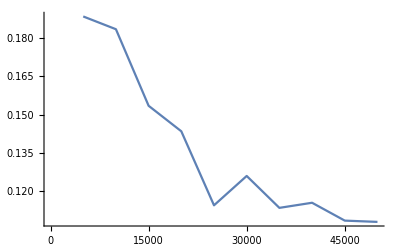
-Graphics-Error RateEpoch

```mathematica
Labeled[ListLinePlot[netdata["ValidationErrorRateList"]],{"Error Rate","Epoch"},{Left,Bottom},RotateLabel->True]
```

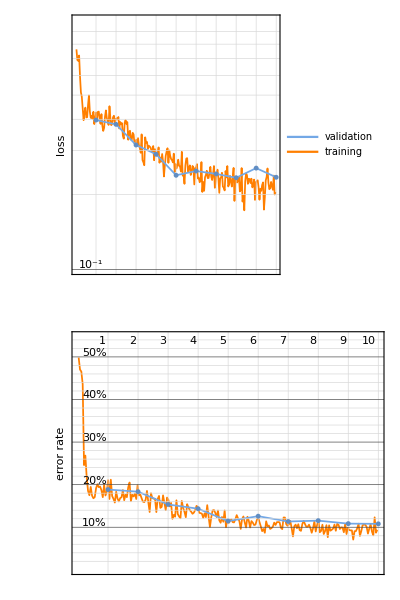
{-Graphics-,0.108}

```mathematica
netdata[{"EvolutionPlots","FinalValidationErrorRate"}]
```

```mathematica
netdata["FinalValidationErrorRate"]
```

0.108

```mathematica
net = netdata["TrainedNet"]
```

NetChain[<>]

```mathematica
NetInformation[net,"FullSummaryGraphic"]
```

-Graphics-

```mathematica
measurements=ClassifierMeasurements[net,testset1]
```

ClassifierMeasurementsObject[…]

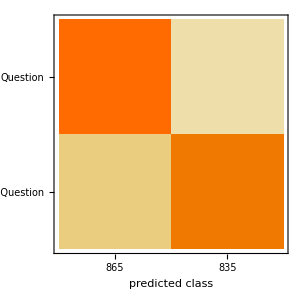

```mathematica
measurements["ConfusionMatrixPlot"]
```

Identified as questions:

```mathematica
ListAnimate[Select[measurements["MisclassifiedExamples"],Values[#]=="Not a Question"&],0.5,SaveDefinitions->True]
```

Identified as sentences:

```mathematica
ListAnimate[Select[measurements["MisclassifiedExamples"],Values[#]=="Question"&],0.5]
```

If not a question is a question

FormFunction - Microsite

```mathematica
FormPage[{{"sentence","Type a Sentence"} ->"String"}, net[#sentence]&,AppearanceRules-> {"Title" -> "Question AI"}]
```

```mathematica
CloudDeploy[

FormPage[{{"sentence","Type a Sentence"} ->"String"}, 

net[#sentence]&,

AppearanceRules-> {"Title" -> "Question AI"}],

"Questionator",
Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/zhamilya.bilyalova/Questionator]

Glove embedding layers

Script for running on Amazon Cloud:

Difference from my the first neural net: no NetEncoder, changing an embedding layer[97,97] to “GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data”.

```mathematica
dec=NetDecoder[{"Class",{"Question","Not a Question"}}];
emb =NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"];
finalNet=NetChain[{emb,DropoutLayer[0.15],GatedRecurrentLayer[512],GatedRecurrentLayer[512],DropoutLayer[0.15],GatedRecurrentLayer[512],SequenceLastLayer[],LinearLayer[32],Ramp,LinearLayer[2],SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{"Question","Not a Question"}}]];
trainednet=NetTrain[finalNet,training,All,ValidationSet->validationset, TargetDevice -> "GPU", BatchSize ->4, LearningRateMultipliers->{"1" -> 0, _ -> 1}];
```

```mathematica
glove=NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"]
EmbeddingLayer[<>]
```

```mathematica
netdata2 = Import[StringJoin[NotebookDirectory[],"trainednet.wdx"]]
```

NetTrainResultsObject[<|1|>]
 |  |  |  |

```mathematica
netdata2["Properties"]
```

{BatchErrorRateList,BatchLossList,BatchSize,CheckpointingFiles,CompactErrorRateEvolutionPlot,CompactLossEvolutionPlot,ErrorRateEvolutionPlot,EvolutionPlots,FinalLearningRate,FinalRoundErrorRate,FinalRoundLoss,FinalValidationErrorRate,FinalValidationLoss,InitialLearningRate,LossEvolutionPlot,LowestValidationErrorRate,LowestValidationLoss,LowestValidationRound,MeanBatchesPerSecond,MeanInputsPerSecond,NetTrainInputForm,OptimizationMethod,RoundErrorRateList,RoundLossList,TotalBatches,TotalInputs,TotalRounds,TotalTrainingTime,TrainedNet,TrainingNet,ValidationErrorRateList,ValidationErrorRateSeries,ValidationLossList,ValidationLossSeries,VersionNumber,WeightsLearningRateMultipliers}

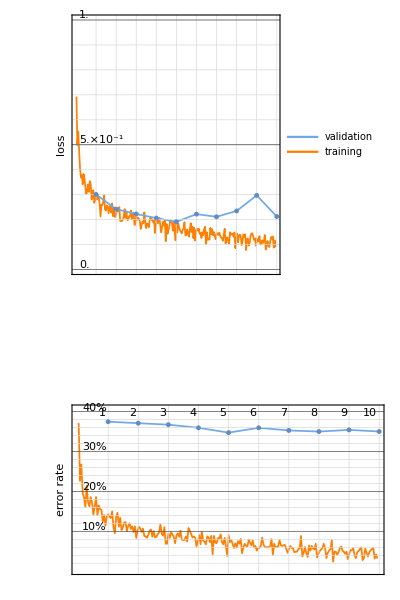
{-Graphics-,0.349933}

```mathematica
netdata2[{"EvolutionPlots","FinalValidationErrorRate"}]
```

```mathematica
net2 = netdata2["TrainedNet"]
```

NetChain[<>]

```mathematica
NetInformation[net2,"FullSummaryGraphic"]
```

-Graphics-

```mathematica
Classify[net,{"Station wagon.","What.","So your clients want something for the lobby of their new corporate headquarters.","Well what's the point of waiting.","It's sixth century B.C.  Do you like the period.","Dance.","Okay.","What are you going to do."}]
```

{Question,Question,Question,Question,Question,Question,Question,Question}

```mathematica
Classify[net,{"How is the career growth of a bank PO.","How do I concentrate better on my studies.","How do I prevent myself from eating too much sweets.","What are some good books for DBMS beginners.","What is the best way to learn math. How can I learn math more effectively.","How can I earn money through YouTube.","What is the role of ethics in corporate governance."}]
```

{Question,Question,Question,Question,Question,Question,Question}

```mathematica
Classify[net,{"I know you did it, but how?","Me","Okay","Are you going to the shop?","What that question ment"}]
```

{Question,Question,Question,Question,Question}

```mathematica
Classify[net,"I loved this lunch"]
```

Not a Question

ELMo net without punctuation

```mathematica
questionsWithoutQuestionsNoP = StringReplace[Normal[StringReplace[questions,{"?"->"."}]],PunctuationCharacter:>""]
normalLinesNoP=

StringReplace[Normal[Join[wikiS,RandomSample[Complement[sentences,questions][[80;;64213]],19653]]],PunctuationCharacter:>""]

Print["creating data set..."]

trainingqsNoP=Thread[#->"Question"]&/@questionsWithoutQuestionsNoP;

trainingnotqsNoP=Thread[#->"Not a Question"]&/@normalLinesNoP;

trainingJoinedNoP=Join[trainingqsNoP,trainingnotqsNoP];

trainingNoP=RandomSample[trainingJoinedNoP,20000];

validationsetNoP=RandomSample[Complement[trainingJoinedNoP,trainingNoP],2000];

testsetNoP=RandomSample[Complement[trainingJoinedNoP,validationsetNoP,trainingNoP],1700]
```

{How is the career growth of a bank PO,How do I concentrate better on my studies,How do I prevent myself from eating too much sweets,What are some good books for DBMS beginners,46299,Its sixth century BC  Do you like the period,Dance,Okay,What are you going to do}
 |  |  |  |

{Artifice Magazine was a nonprofit literary magazine based in Chicago Illinois,46305,Lemme out of this coffin}
 |  |  |  |

creating data set...

{Im a captain→Not a Question,REPEAT→Not a Question,Who is eligible for taking MCAT exams→Question,What are pseudo question and what are some examples→Question,Its okay honey→Not a Question,With all the shit she kept doing→Not a Question,What it is meant by Informatica active and passive transformation→Question,Would you say you understand Josephine→Question,I tell you stuff that I dont tell anyone else→Not a Question,It is only too possible→Not a Question,How can I teach myself Mandarin for free→Question,What are some examples of epithelial tissues→Question,Did you even to try to negotiate→Question,I can come down next week→Not a Question,Im sorry about Saturday Dad→Not a Question,ndwelling an 1893 poem by Thomas Edward Brown→Not a Question,Some asshole wrote a poem about that once→Not a Question,Will the new Rs 2000 notes carry a nano GPS chip Will it really Help→Question,Hes with a bunch of guys who want to sneak into the city tonight→Not a Question,You shouted at me in the auditorium when I read my essay→Not a Question,Why do you always disrespect me like that→Question,The most highlyregarded period of production is about 16401740→Not a Question,Havent you forgotten something→Question,Shut your mouth→Not a Question,You remembered→Not a Question,Why do Taiwanese people dislike China→Question,Why do some answers get collapsed on Quora→Question,No no Im not angry Im not Im just thrown Im→Not a Question,Maybe like work in a petting zoo or something→Not a Question,The terms Order of Saint Benedict and Benedictine Order are however also used to refer to all Benedictine communities collectively sometimes giving the incorrect impression that there exists a generalate or motherhouse with jurisdiction over them→Not a Question,What baby→Question,Carbon dioxide→Question,How do converting waste lubricant oil to diesel fuel→Question,Dont give me this we were partners→Not a Question,How can I learn how to be happy→Question,Indian School of Business YLP I have a year to go before I apply for YLP can somebody give me tips to boost my resume→Question,Over and over→Not a Question,Is he not tired→Question,Shall we→Question,Rose you work too hard→Not a Question,Show her in→Not a Question,Do you think that Donald Trump would be the worst president the United States would ever have→Question,They are commonly known for their extensive tunneling activities→Not a Question,Why are diamonds valuable→Question,Whatre you laughing about→Question,Who didnt→Question,In linguistics periphrasis  is the usage of multiple separate words to carry the meaning of prefixes suffixes or verbs among other things where either would be possible→Not a Question,Forget her youre mine→Not a Question,Excuse me Skipper What about time→Question,Know what→Question,Vertical devices are known as tanning booths or standup sunbeds→Not a Question,The activities on a pig farm depend on the husbandry style of the farmer and range from very little intervention as when pigs are allowed to roam villages or towns and dispose of garbage to intensive systems where the pigs are contained in a building for the majority of their lives→Not a Question,If a bra is worn with a halter top it is generally either strapless or of halterneck construction itself so as to avoid exposing the back straps of a typical bra→Not a Question,The terms pinnation and pennation are cognate and although they are sometimes used distinctly there is no consistent difference in the meaning or usage of the two words→Not a Question,Nice mouth you got there Mom but I  Im not goin through this again→Not a Question,Tonight→Question,What is the best way to monetize user generated video content→Question,How do I develop my presence of mind→Question,Am I supposed to worry about whats in the refrigerator too→Question,The start and end points of time for a night vary based on factors such as season latitude longitude and time zone→Not a Question,Finished lumber is supplied in standard sizes mostly for the construction industry  primarily softwood from coniferous species including pine fir and spruce collectively sprucepinefir cedar and hemlock but also some hardwood for highgrade flooring→Not a Question,Do CBSE students suffer in class 12 they get 90 in class 10 and 50 in boards→Question,Dirt is unclean matter especially when in contact with a persons clothes skin or possessions when they are said to become dirty→Not a Question,Will an iPhone 7 plus bought through Tmobile work in India→Question,maybe she had an accident→Not a Question,What are the common mistakes that new sellers on eBay make→Question,The bone is formed from a fusion of left and right processes and the point where these sides join the mandibular symphysis is still visible as a faint ridge in the midline→Not a Question,If I delete my whisper account can the other person still see my messages→Question,Shell forget about us eventually→Not a Question,The third stage of labor can be managed actively with several standard procedures or it can be managed expectantly also known as physiological management or passive management the latter allowing the placenta to be expelled without medical assistance→Not a Question,A girls gotta know how to defend herself dont she→Question,Opportunity may refer to
Opportunity rover a robotic rover active on the planet Mars since 2004
The Opportunity a 17thcentury play
Opportunity→Not a Question,Theorists who adopt this interpretation think of probability as a physical propensity or disposition or tendency of a given type of physical situation to yield an outcome of a certain kind or to yield a long run relative frequency of such an outcome→Not a Question,Did I have anything to say about it→Question,Do you understand that→Question,Why is sex education considered a taboo topic in India→Question,What are some major social faux pas to avoid when visiting Bangladesh→Question,Larry from the States→Not a Question,Wheres Clark→Question,Why is it that we havent been able to tap into the full potential of our brains→Question,I had to dive in and save him→Not a Question,Groovy→Not a Question,A suit was gone→Not a Question,What did you feel Brian when you first got there→Question,Doesnt make much sense does it→Question,What are new research topics in geotechnical engineering for master degree→Question,A metaphor is a figure of speech that directly refers to one thing by mentioning another for rhetorical effect→Not a Question,Originally meaning strange or peculiar queer came to be used pejoratively against those with samesex desires or relationships in the late 19th century→Not a Question,Do I make you nervous→Question,Emotion is also linked to behavioral tendency→Not a Question,He promoted reconciliation between the countrys indigenous tribal groups and its European minority although his relations with the Kenyan Indians were strained→Not a Question,Look Brian a photographer→Not a Question,Tell Mother beware→Not a Question,This ship its crazy trying to go fastern light thats like the Tower of Babel→Not a Question,Jean may refer to→Not a Question,Youre a free thinker→Not a Question,Overthrow structure the crowning section of ornamental wrought iron work which forms a decorative crest above a wrought iron gate→Not a Question,25 less than 300 is what  more than 200→Question,How can I hack WiFi using a command prompt→Question,Thats not it→Not a Question,Whats the difference between Italian Fascism and Nazism→Question,How do you download Pokémon GO→Question,Woodhull may refer to→Not a Question,How do I apply for a summer internship→Question,Do girls really like tall guys→Question,One of them is used as the pedestal of the Bronze Horseman in Saint Petersburg Russia→Not a Question,Shadowbox is a DVD and accompanying EP by The Crxshadows→Not a Question,Can banks run a 247 operation→Question,Is it so wrong to go up to a guy and tell him that he is beautiful→Question,I cant→Not a Question,now what→Question,Will I grow taller at 15→Question,For example in India licensed moneylenders are governed by Money Lenders Acts of respective states→Not a Question,A plant is often termed a weed when it has one or more of the following characteristics→Not a Question,What mythical creatures are in the Bible→Question,What is it like flying first class→Question,Whats your favourite anime→Question,What are the safety precautions on handling shotguns proposed by the NRA in North Carolina→Question,Who will win in Liverpool VS AC Milan International Champions Cup→Question,Sometimes prequels play on the audiences knowledge of what will happen next using deliberate references to create dramatic irony→Not a Question,Why dont you just do it out of the kindness of your heart→Question,But for you→Question,Sometimes which→Question,Tell me in sadness who is that you love→Not a Question,It is objectoriented classbased and reflective→Not a Question,Most lemonade varieties can be separated into two distinct types cloudy or clear each is known simply as lemonade or a cognate in countries where dominant→Not a Question,Listen what Im about to tell you Im telling you in confidence okay→Question,Its not finished→Not a Question,How are design decisions made at Google→Question,Im back here arent I→Question,What is another word for I→Question,How can I dual boot Windows 7 and Linux→Question,A disassembler is a computer program that translates machine language into assembly languagethe inverse operation to that of an assembler→Not a Question,Do two photons emitted from two atoms 1 meter apart have a higher probability of being found further apart after one second Is this an arrow of time→Question,What TV series were cancelled too soon→Question,Why on earth do you say that→Question,You think you can stitch me up on you own→Question,I forgot my ATM PIN What do I do→Question,Are you really going to drink that stuff→Question,thats when you start praying all the time→Not a Question,Purple drank a recreational drug→Not a Question,Are you afraid→Question,What is magnetic moment of an electron→Question,Panties were originally designed to cover the entire lower half of the female torso since the 1970s panties have had either no legs or in some cases very short ones and have become increasingly brief over time→Not a Question,That light is not daylight I know it I→Not a Question,Polemics are mostly seen in arguments about controversial topics→Not a Question,The last time I heard from her she was living in San Francisco→Not a Question,Kid over there caught the case→Not a Question,How do I get rid of excessive weight→Question,But come on Harry whats the real reason→Question,Maiman at Hughes Research Laboratories based on theoretical work by Charles Hard Townes and Arthur Leonard Schawlow→Not a Question,How long would it actually take to travel to Mars→Question,At least no ones gonna see how bad you are→Not a Question,Dont let us make you nervous or nothinwe know you gotta job to do→Not a Question,SPOILERS What happened at the end of Wolf of Wall Street→Question,When is the best time to visit France→Question,Roofing work can be physically demanding because it involves heavy lifting as well as climbing bending and kneeling frequently in very hot weather→Not a Question,What was it→Question,What positions I am eligible to apply at Oracle→Question,A millwright is a high precision craftsman or tradesman who installs dismantles repairs reassembles and moves machinery in factories power plants and construction sites→Not a Question,Then why did you quit→Question,Historically a liquiddriven escapement was used for a washstand design in ancient Greece and the Hellenistic world particularly Ptolemaic Egypt while the medieval Chinese beginning in the Tang dynasty and culminating during the Song dynasty applied liquiddriven escapements to clockworks→Not a Question,Now how are you going to do that→Question,Just some rich Anglo out on the lake→Not a Question,Spreading from Italian to the other European languages the term was long used largely interchangeably with arabesque and moresque for types of decorative patterns using curving foliage elements→Not a Question,Our revels now are ended You disappoint me Emma→Not a Question,Theyre no friends of mine→Not a Question,How do I know if Im good→Question,What do you want me for anyway→Question,A consultant is usually an expert or an experienced professional in a specific field and has a wide knowledge of the subject matter→Not a Question,Is it safe to smoke weed once a week→Question,He also agreed to waive his performance fee for full ownership of the Sesame Street Muppets and to split any revenue they generated with the Childrens Television Workshop renamed to the Sesame Workshop in 2000 the series nonprofit producer→Not a Question,Dont tell me youre waiting for lightning to strike→Not a Question,Why are you driving→Question,Whose fault is the illegal construction developer or administration→Question,Mister OHiggins I wonder if I know your good father→Question,Thank you for calling the white House→Not a Question,Mrs Christian→Not a Question,Because of these persistent natural forces sea walls need to be maintained and eventually replaced to maintain their effectiveness→Not a Question,What government will do from old currency→Question,What is it like to be a lesbian in India→Question,You get it quick→Not a Question,Welsh may refer to→Not a Question,This militant irony or sarcasm often professes to approve of or at least accept as natural the very things the satirist wishes to attack→Not a Question,The inference rules are commonly specified by means of an ontology language and often a description logic language→Not a Question,Youd make a pisspoor lawyer→Not a Question,My ITRV has place as pune instead of bangalore can I strike it off and post it→Question,What was I wearing→Question,In firearms rifling is the helical groove pattern that is machined into the internal bore surface of a guns barrel for the purpose of exerting torque and thus imparting a spin to a projectile around its longitudinal axis during shooting→Not a Question,What is the best working model that easily can make by 8 class student→Question,Germany classifies Scientology groups as an anticonstitutional sect→Not a Question,retending Eric Clapton song a 1989 rock song written and composed by Jerry Lynn Williams
→Not a Question,How do you make a site like Facebook→Question,How did you end up here→Question,You sure dont fit in down on the Boulevard lookin like you do→Not a Question,I want to improve my English→Question,Other treatment options may target airway inflammation or may promote mucus expectoration→Not a Question,What subscription payment option should i use for my mobile app for non US markets→Question,WHY→Question,It is found in temperate and tropical waters across the globe in the epipelagic and mesopelagic zones→Not a Question,If that object withstands ablation from its passage through the atmosphere as a meteor and impacts with the ground it is then called a meteorite→Not a Question,Sepsis is more common among males than females→Not a Question,Next time you try that Mr Mitchell  dont→Not a Question,Is it possible for a girl to like you but be a really slow texter→Question,Written Chinese the writing system used for Chinese

Chinese cuisine styles of food originating from China
American Chinese cuisine→Not a Question,What are some ways to hack a Facebook account→Question,How do I see if someone visited my Facebook profile→Question,Whats he going to say→Question,How much kale is in a bunch→Question,What UK online shopping stores dont require a CVV code→Question,Vales or Vale is a surname→Not a Question,Where can I get branded surplus garments in Bangalore→Question,So does he→Not a Question,Lets just kick it here alright→Question,If he talks or writes a note BOOTH EARL BOOTH EARL BOOTH EARL EARL BOOTH EARL BOOTH EARL BOOTH BOOTH EARL BOOTH EARL BOOTH EARL BOOTH EARL BOOTH BOOTH m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 u7327 u7331 u7327 u7331 u7327 u7331 u7331 u7327 u7331 u7327 u7331 u7331 u7327 u7331 u7327 u7331 u7327 u7331 u7331 u7327 u7327 u7331 u7327 u7331 u7327 u7331 u7331 u7327 u7327 u7334 u7327 u7334 u7327 u7334 u7327 u7334 u7327 u7334 u7332 u7327 u7332 u7327 u7332 u7327 u7327 u7332 u7327 u7332 u7327 u7332 u7327 u7332 u7327 u7332 u7327 u7332 u7327 u7332 u7327 u7327 u7332 u7327 u7327 u7332 u7327 u7332 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7330 u7327 u7330 u7327 u7330 u7327 u7327 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7330 u7327 u7327 u7333 u7327 u7333 u7327 u7327 u7333 u7327 u7333 u7327 u7333 u7327 u7333 u7333 u7327 u7333 u7333 u7327 u7333 u7327 u7333 u7327 u7327 u7327 u7333 u7327 u7327 u7333 u7327 u7333 u7327 u7333 u7327 u7333 u7327 u7330 u7328 u7328 u7330 u7330 u7328 u7328 u7330 u7330 u7328 u7330 u7328 u7330 u7328 u7330 u7328 u7330 u7328 u7330 u7330 u7328 u7330 u7330 u7328 u7330 u7328 u7330 u7328 u7330 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7329 u7328 u7331 u7334 u7331 u7334 u7331 u7331 u7334 u7331 u7334 u7334 L475646 L475645 L475644 L475643 L475641 L475640 L475639 L475638 L475637 L475636 L475635 L475634 L475633 L475632 L475631 L478251 L478250 L478249 L478248 L478247 L478246 L478245 L478244 L478243 L478242 L478723 L478722 L478701 L478700 L478699 L478698 L478686 L478685 L478684 L478683 L478682 L478681 L478680 L478280 L478279 L478278 L478277 L478276 L478275 L478274 L478540 L478539 L478533 L478532 L478531 L478530 L478529 L478528 L478527 L478526 L478525 L478515 L478514 L478513 L478512 L478511 L478510 L478509 L478508 L478491 L478490 L478489 L478484 L478483 L478482 L478481 L478478 L478477 L478476 L478475 L478474 L478469 L478468 L478467 L478466 L478297 L478296 L478295 L478294 L478293 L478292 L478291 L478290 L478289 L478288 L478287 L478286 L478285 L478284 L478283 L478783 L478782 L478778 L478777 L478321 L478320 L478209 L478208 L478207 L478206 L478205 L478201 L478200 L478199 L478198 L478184 L478183 L478182 L478181 L478180 L478179 L478178 L478177 L478176 L478175 L478662 L478661 L478660 L478659 L478658 L478657 L478301 L478300 L478820 L478819 L478818 L478817 L478816 L478815 L478814 L478813 L478812 L478811 L478810 L478809 L478808 L478807 L478806 L478804 L478803 L478801 L478800 L478799 L478798 L478797 L478796 L478795 L478791 L478790 L478781 L478780 L478751 L478750 L478749 L478747 L478746 L478745 L478744 L478743 L478742 L478741 L478736 L478735 L478677 L478676 L478675 L478674 L478673 L478672 L478671 L478670 L478669 L478668 L478643 L478642 L478636 L478635 L478634 L478629 L478628 L478623 L478622 L478621 L478620 L478619 L478618 L478617 L478616 L478614 L478613 L478612 L478611 L478610 L478609 L478607 L478606 L478605 L478604 L478603 L478602 L478601 L478600 L478599 L478598 L478595 L478594 L478593 L478592 L478591 L478590 L478589 L478588 L478587 L478586 L478585 L478584 L478583 L478582 L478581 L478580 L478579 L478578 L478577 L478576 L478575 L478574 L478573 L478572 L478571 L478570 L478569 L478568 L478567 L478566 L478565 L478564 L478563 L478562 L478561 L478560 L478559 L478558 L478557 L478556 L478555 L478554 L478553 L478552 L478551 L478550 L478503 L478502 L478501 L478500 L478499 L478498 L478497 L478471 L478470 L478465 L478464 L478462 L478461 L478460 L478459 L478452 L478451 L478450 L478444 L478443 L478442 L478441 L478440 L478439 L478438 L478435 L478434 L478433 L478432 L478431 L478430 L478429 L478428 L478427 L478426 L478425 L478424 L478423 L478422 L478421 L478420 L478419 L478418 L478417 L478416 L478412 L478411 L478410 L478409 L478408 L478407 L478406 L478405 L478404 L478403 L478402 L478401 L478400 L478399 L478398 L478397 L478396 L478395 L478394 L478393 L478392 L478391 L478390 L478389 L478388 L478387 L478386 L478385 L478384 L478383 L478382 L478381 L478380 L478379 L478378 L478377 L478376 L478375 L478374 L478373 L478372 L478371 L478370 L478369 L478368 L478367 L478366 L478365 L478364 L478363 L478362 L478360 L478359 L478358 L478357 L478356 L478355 L478354 L478353 L478352 L478351 L478350 L478327 L478326 L478325 L478324 L478323 L478314 L478313 L478312 L478311 L478310 L478309 L478308 L478307 L478233 L478232 L478231 L478230 L478229 L478228 L478227 L478226 L478225 L478224 L478223 L478222 L478213 L478212 L478196 L478195 L478194 L478193 L478192 L478191 L478188 L478187 L478186 L478185 L478174 L478173 L478172 L478170 L478169 L478168 L478167 L478143 L478142 L478140 L478139 L478138 L478137 L478135 L478134 L478124 L478123 L478122 L478120 L478119 L478118 L478117 L478116 L478115 L478114 L478113 L478112 L478111 L478110 L478109 L478105 L478104 L478103 L478102 L478101 L478100 L478099 L478098 L478097 L478096 L478095 L478094 L478088 L478087 L478086 L478085 L478084 L478083 L478082 L478081 L478080 L478079 L478078 L478343 L478342 L478341 L478340 L478339 L478338 L478758 L478757 L478756 L478755 L478667 L478666 L478665 L478664 L478663 L478656 L478655 L478654 L478653 L478652 L478651 L478650 L478649 L478648 L478647 L478645 L478644 L478488 L478487 L478486 L478480 L478479 L478473 L478472 L478535 L478534 L478523 L478522 L478521 L478520 L478519 L478518 L478346 L478345 L478271 L478270 L478269 L478268 L478262 L478261 L478235 L478234 L478092 L478091 L478090 L478089 L478775 L478774 L478773 L478772 L478771 L478334 L478333 L478332 L478331 L478330 L478329 L478328 L478204 L478203 L478164 L478163 L478162 L478161 L478160 L478158 L478157 L478156 L478155 L478154 L478149 L478148 L478221 L478220 L478219 L478218 L478217 L478216 L478215 L478214 L477745 L477744 L477743 L477742 L477741 L477740 L477739 L477737 L477736 L477735 L477734 L477733 L477732 L477731 L477381 L477380 L477459 L477458 L477457 L477456 L477455 L477454 L477453 L477452 L477451 L477450 L477449 L477448 L478057 L478056 L478055 L478054 L477688 L477687 L477686 L477474 L477473 L478074 L478073 L478072 L478071 L478070 L478026 L478025 L478023 L478022 L478019 L478018 L478017 L477973 L477972 L477959 L477958 L477929 L477928 L477927 L477925 L477924 L477881 L477880 L477873 L477872 L477869 L477868 L477867 L477865 L477864 L477863 L477862 L477861 L477860 L477859 L477858 L477857 L477856 L477855 L477854 L477853 L477847 L477846 L477845 L477844 L477843 L477842 L477841 L477840 L477839 L477838 L477837 L477834 L477833 L477831 L477830 L477829 L477828 L477827 L477826 L477825 L477802 L477801 L477800 L477799 L477798 L477784 L477783 L477782 L477781 L477780 L477779 L477778 L477773 L477772 L477771 L477770 L477769 L477768 L477767 L477766 L477716 L477715 L477714 L477710 L477709 L477708 L477707 L477706 L477705 L477704 L477703 L477702 L477701 L477700 L477669 L477668 L477667 L477666 L477664 L477663 L477662 L477661 L477660 L477590 L477589 L477586 L477585 L477584 L477583 L477582 L477581 L477580 L477579 L477574 L477573 L477570 L477569 L477568 L477567 L477566 L477565 L477564 L477563 L477562 L477561 L477560 L477548 L477547 L477546 L477528 L477527 L477524 L477523 L477522 L477517 L477516 L478068 L478067 L478066 L478065 L478064 L478063 L478062 L478021 L478020 L478005 L478004 L478003 L478002 L477996 L477995 L477994 L477971 L477970 L477969 L477968 L477967 L477966 L477965 L477964 L477676 L477675 L477504 L477503 L477502 L477501 L477500 L477499 L477498 L477497 L477469 L477468 L477467 L477466 L477465 L477464 L477463 L477462 L477447 L477446 L477439 L477438 L477437 L477417 L477416 L477396 L477395 L477940 L477939 L477938 L477937 L477756 L477755 L477754 L477753 L477752 L477751 L477726 L477725 L477724 L477723 L477640 L477639 L477637 L477636 L477494 L477493 L477492 L477491 L477490 L477489 L477488 L477487 L477486 L477485 L477484 L477481 L477480 L477479 L477478 L477477 L477819 L477818 L477815 L477814 L477813 L477812 L477811 L477810 L477809 L477412 L477411 L477402 L477401 L477398 L477397 L477391 L477390 L477389 L477388 L477387 L477385 L477384 L477383 L477382 L477993 L477992 L477991 L477953 L477952 L477951 L477647 L477646 L477645 L477644 L477643 L477642 L477641 L477891 L477890 L477889 L477888 L477536 L477535 L477534 L477533 L477532 L477823 L477822 L477821 L477820 L477634 L477633 L477433 L477432 L477431 L477430 L477429 L477428 L477427 L477378 L477377 L477375 L477374 L477373 L477372 L477371 L480093 L480092 L479933 L479932 L479729 L479728 L479727 L479726 L479725 L479724 L479723 L479719 L479718 L479716 L479715 L480192 L480191 L480190 L480189 L480187 L480186 L480126 L480125 L480116 L480115 L479722 L479721 L479675 L479674 L479762 L479761 L479760 L479759 L479758 L479756 L479755 L479753 L479752 L479751 L479750 L479749 L479748 L479747 L479743 L479742 L479741 L479740 L480171 L480170 L480168 L480167 L480166 L480163 L480162 L479579 L479578 L480165 L480164 L480150 L480149 L480112 L480111 L480110 L480109 L480108 L480107 L480096 L480095 L480226 L480225 L480030 L480029 L480028 L480027 L480024 L480023 L479554 L479553 L479552 L479551 L479549 L479548 L479545 L479544 L479543 L479542 L479541 L479540 L479539 L479536 L479535 L479534 L480224 L480223 L480222 L480020 L480019 L480018 L480017 L480196 L480195 L480194 L480184 L480183 L480182 L480181 L480022 L480021 L479993 L479992 L479991 L479990 L479989 L479988 L479987 L479986 L479985 L479984 L479575 L479574 L479572 L479571 L479570 L479569 L479568 L479567 L479566 L479565 L479564 L479563 L479562 L479561 L479560 L479559 L479547 L479546 L479538 L479537 L480013 L480012 L480011 L480010 L480009 L480008 L480007 L480006 L480004 L480003 L480002 L480001 L480000 L479999 L479998 L479997 L479996 L479995 L479994 L480179 L480178 L479937 L479936 L479612 L479611 L479610 L479608 L479607 L479606 L479605 L479604 L479807 L479806 L479804 L479803 L479802 L479801 L479626 L479625 L479596 L479595 L479594 L479590 L479589 L479588 L479587 L479586 L479585 L479584 L479583 L480199 L480198 L480197 L479710 L479709 L479699 L479698 L479697 L479696 L479666 L479665 L479661 L479660 L479657 L479656 L479655 L479649 L479648 L480288 L480287 L480286 L480285 L480284 L480283 L480277 L480276 L480275 L480270 L480269 L480268 L480267 L480266 L480265 L480264 L480263 L480261 L480260 L480145 L480144 L480143 L480142 L480141 L480140 L480139 L480138 L480137 L480135 L480134 L480133 L480132 L480131 L480124 L480123 L480122 L480120 L480119 L480100 L480099 L480098 L480089 L480088 L480087 L480086 L480085 L480084 L480083 L480082 L480081 L480080 L480079 L480078 L480077 L480076 L480075 L480074 L480073 L480072 L480071 L480070 L480069 L480068 L480067 L480057 L480056 L480055 L480054 L480053 L480044 L480043 L479979 L479978 L479973 L479972 L479971 L479970 L479969 L479968 L479967 L479962 L479961 L479952 L479951 L479950 L479949 L479948 L479947 L479940 L479939 L479935 L479934 L479930 L479929 L479928 L479923 L479922 L479921 L479898 L479897 L479893 L479892 L479891 L479890 L479889 L479888 L479887 L479886 L479884 L479883 L479882 L479881 L479879 L479878 L479877 L479876 L479874 L479873 L479872 L479871 L479870 L479869 L479868 L479865 L479864 L479862 L479861 L479860 L479859 L479858 L479857 L479856 L479855 L479854 L479852 L479851 L479850 L479849 L479847 L479846 L479811 L479810 L479809 L479808 L479783 L479782 L479771 L479770 L479701 L479700 L479684 L479683 L479682 L479680 L479679 L479678 L479677 L479672 L479671 L479642 L479641 L479640 L479639 L479638 L479636 L479635 L479620 L479619 L479618 L479617 L479614 L479613 L479601 L479600 L479599 L480238 L480237 L480236 L480235 L480234 L480233 L480232 L480231 L480230 L480210 L480209 L480161 L480160 L480159 L480158 L480153 L480152 L480106 L480105 L480104 L480103 L480102 L480038 L480037 L480036 L480035 L480034 L479844 L479843 L479842 L479841 L479840 L479839 L479838 L479837 L479836 L479835 L479834 L479833 L479832 L479831 L479830 L479828 L479827 L479825 L479824 L479823 L479795 L479794 L479793 L479792 L479791 L479790 L479789 L479788 L479787 L479786 L479603 L479602 L479598 L479597 L479582 L479581 L479580 L479523 L479522 L480255 L480254 L480253 L480252 L480251 L480250 L480207 L480206 L479958 L479957 L479956 L479955 L479670 L479669 L479516 L479515 L479514 L479513 L479512 L479511 L479510 L479509 L479508 L480305 L480304 L480303 L480302 L480299 L480298 L480297 L480296 L480295 L480294 L480293 L480853 L480852 L480851 L480850 L480849 L480848 L480847 L480846 L480845 L480844 L480843 L480842 L481180 L481179 L481178 L481177 L481176 L481175 L481174 L481173 L481172 L481171 L481170 L481169 L481168 L481167 L481166 L481148 L481147 L481088 L481087 L481086 L481082 L481081 L481080 L481079 L481075 L481074 L481073 L481072 L481071 L481070 L481069 L480937 L480936 L480935 L480934 L480933 L480913 L480912 L480911 L480903 L480902 L480886 L480885 L480642 L480641 L480640 L480639 L480638 L480637 L480636 L480635 L480634 L480633 L480632 L480631 L480426 L480425 L480424 L480423 L480422 L480421 L480420 L480419 L480418 L480417 L480383 L480382 L480364 L480363 L480360 L480359 L480347 L480346 L480345 L480344 L480343 L480342 L480341 L480340 L480339 L480338 L481052 L481051 L481050 L481049 L481048 L481047 L481015 L481014 L481013 L481012 L481010 L481009 L481008 L481007 L481006 L481005 L481004 L481003 L481002 L481001 L481000 L480996 L480995 L480994 L480993 L480992 L480991 L480984 L480983 L480982 L480981 L480980 L480979 L480978 L480977 L480976 L480975 L480974 L480973 L480921 L480920 L480919 L480884 L480883 L480882 L480881 L480764 L480763 L480762 L480761 L480760 L480759 L480758 L480757 L480756 L480755 L480754 L480753 L480752 L480751 L480750 L480749 L480748 L480747 L480746 L480745 L480744 L480743 L480742 L480741 L480740 L480739 L480738 L480737 L480736 L480735 L480734 L480733 L480588 L480587 L480586 L480585 L480584 L480583 L480582 L480581 L480580 L480579 L480571 L480570 L480565 L480564 L480563 L480798 L480797 L480796 L480795 L480794 L480793 L480792 L480791 L480790 L480789 L480788 L480787 L480320 L480319 L480318 L480317 L480316 L480315 L480314 L480313 L481212 L481211 L481210 L481209 L481206 L481205 L480898 L480897 L480888 L480887 L480477 L480476 L480453 L480452 L480700 L480699 L480698 L480697 L480696 L480695 L480694 L480693 L480692 L480691 L480690 L480689 L480416 L480415 L480414 L480413 L480412 L480411 L480410 L480409 L480408 L480407 L480406 L480405 L480404 L480403 L480402 L480401 L480400 L480399 L480398 L480397 L480396 L480395 L480394 L480393 L480392 L480391 L480390 L480389 L480388 L480358 L480357 L480349 L480348 L481204 L481203 L481202 L481046 L481045 L481044 L480989 L480988 L480524 L480523 L480522 L480487 L480486 L480609 L480608 L480599 L480598 L480597 L480596 L480595 L480592 L480591 L480521 L480520 L480519 L480518 L480517 L480516 L480515 L480514 L480499 L480498 L480485 L480484 L480483 L480482 L480481 L480480 L480479 L480478 L480475 L480474 L480471 L480470 L480469 L480468 L480467 L480466 L480465 L480490 L480489 L480460 L480459 L480458 L480457 L480456 L480455 L480454 L480451 L480450 L480449 L480448 L480445 L480444 L480443 L480442 L480440 L480439 L480438 L480437 L480436 L480435 L480434 L480433 L481040 L481039 L481038 L481037 L481036 L481035 L481032 L481031 L480717 L480716 L480715 L480714 L480713 L480712 L480711 L480710 L480709 L480708 L480707 L480706 L480705 L480704 L480703 L480702 L480701 L480601 L480600 L481067 L481066 L481065 L481064 L481063 L481060 L481059 L481058 L481057 L481056 L481055 L481054 L481053 L480918 L480917 L480916 L480915 L480914 L480728 L480727 L481189 L481188 L481187 L481186 L481165 L481164 L481163 L481162 L481161 L481160 L481159 L481158 L481157 L481156 L481111 L481110 L481109 L481108 L481107 L481106 L481105 L481104 L481103 L481102 L481101 L481100 L481099 L481098 L481096 L481095 L481094 L481093 L481092 L481091 L481090 L480963 L480962 L480959 L480958 L480957 L480956 L480955 L480953 L480952 L480951 L480931 L480930 L480929 L480928 L480927 L480926 L480925 L480924 L480910 L480909 L480908 L480907 L480906 L480905 L480904 L480880 L480879 L480878 L480877 L480876 L480875 L480874 L480858 L480857 L480856 L480855 L480827 L480826 L480825 L480823 L480822 L480821 L480820 L480819 L480818 L480817 L480816 L480815 L480814 L480813 L480812 L480811 L480810 L480809 L480805 L480804 L480779 L480778 L480777 L480776 L480775 L480774 L480773 L480772 L480771 L480770 L480769 L480768 L480767 L480766 L480726 L480725 L480724 L480723 L480722 L480676 L480675 L480674 L480673 L480672 L480671 L480670 L480669 L480668 L480667 L480666 L480665 L480664 L480663 L480662 L480661 L480660 L480659 L480658 L480657 L480656 L480655 L480654 L480653 L480652 L480651 L480650 L480649 L480626 L480625 L480624 L480621 L480620 L480619 L480618 L480617 L480616 L480615 L480614 L480613 L480612 L480611 L480606 L480605 L480604 L480603 L480602 L480554 L480553 L480552 L480551 L480550 L480549 L480548 L480538 L480537 L480536 L480534 L480533 L480532 L480493 L480492 L480463 L480462 L480461 L480943 L480942 L480941 L480873 L480872 L480871 L480870 L480869 L480868 L480867 L480860 L480859 L480547 L480546 L480545 L480543 L480542 L480541 L480540 L481043 L481042 L481041 L481029 L481028 L481027 L481023 L481022 L481021 L481020 L481017 L481016 L480986 L480985 L480324 L480323 L480322 L480301 L480300 L480950 L480949 L480948 L480947 L480946 L480945 L480944 L480896 L480895 L480894 L480864 L480863 L480862 L480839 L480838 L480837 L480836 L480835 L480834 L480833 L480832 L480831 L480830 L480829 L480828 L481462 L481461 L481460 L481459 L481448 L481447 L481446 L481445 L481444 L481443 L481362 L481361 L481360 L481871 L481870 L481698 L481697 L481696 L481695 L481694 L481657 L481656 L481655 L481431 L481430 L481429 L481749 L481748 L481747 L481746 L481745 L481744 L481743 L481742 L481741 L481740 L481739 L481591 L481590 L481437 L481436 L481435 L481297 L481296 L481365 L481364 L481363 L481259 L481258 L481257 L481256 L481251 L481250 L481249 L481248 L481247 L481246 L481319 L481318 L481317 L481316 L481261 L481260 L481236 L481235 L481234 L481233 L481843 L481842 L481772 L481771 L481716 L481715 L481351 L481350 L481343 L481342 L481861 L481860 L481859 L481839 L481838 L481837 L481836 L481835 L481834 L481833 L481832 L481831 L481830 L481829 L481828 L481827 L481825 L481824 L481823 L481822 L481821 L481820 L481819 L481818 L481817 L481816 L481815 L481814 L481813 L481812 L481811 L481810 L481808 L481807 L481806 L481805 L481804 L481803 L481802 L481801 L481776 L481775 L481774 L481773 L481770 L481769 L481768 L481767 L481764 L481763 L481762 L481761 L481685 L481684 L481683 L481682 L481681 L481680 L481679 L481678 L481677 L481676 L481649 L481648 L481647 L481646 L481645 L481644 L481643 L481642 L481641 L481640 L481639 L481580 L481579 L481578 L481577 L481576 L481570 L481569 L481568 L481567 L481566 L481565 L481564 L481563 L481562 L481561 L481560 L481508 L481507 L481466 L481465 L481327 L481326 L481325 L481324 L481323 L481322 L481321 L481292 L481291 L481290 L481289 L481288 L481287 L481286 L481285 L481284 L481283 L481282 L481281 L481280 L481279 L481278 L481277 L481275 L481274 L481273 L481272 L481271 L481270 L481269 L481267 L481266 L481265 L481264 L481553 L481552 L481551 L481550 L481400 L481399 L481398 L481537 L481536 L481535 L481534 L481523 L481522 L481305 L481304 L481303 L481302 L481301 L481457 L481456 L481455 L481454 L481453 L481452 L481451 L481450 L481449 L481758 L481757 L481756 L481755 L481754 L481753 L481752 L481751 L481675 L481674 L481673 L481672 L481470 L481469 L481312 L481311 L481310 L481309 L481485 L481484 L481483 L481482 L481481 L481480 L481479 L481478 jam →Not a Question,Do consumer product tech companies value UX research→Question,I guess hes still on the road→Not a Question,Best seat in the house  Hey Mick this is too much→Not a Question,What do Flipkarts delivery boys look for when I exchange my old lcd for a new one→Question,Am I going mad or did the word think escape your lips→Question,Then we will begin with replacing the Tibetan flag with the flag of the Motherland→Not a Question,They dont care anything for John theyre just trying to impress their friends→Not a Question,He also gave a number of novel scientific accounts of natural phenomena→Not a Question,Mung bean sprout is made from the greenishcapped mung beans
Soybean sprout is made from yellow largergrained soybean
It typically takes one week for them to become fully grown→Not a Question,Do you think hell call this week→Question,Youre playing a piano Miss Starling→Question,Evaporation is an essential part of the water cycle→Not a Question,So its an honor→Question,How do I find love→Question,I dont think hes going to be doing any bargaining with us the stupid sonofabitch→Not a Question,What are the chances to crack the civil services exam for an average student→Question,Afforestation is the establishment of a forest or stand of trees forestation in an area where there was no previous tree cover→Not a Question,This cut has its greatest popularity in Britain→Not a Question,Oh Frederick Am I a good man or am I a bad man→Question,Hazelnuts are rich in protein monounsaturated fat vitamin E manganese and numerous other essential nutrients nutrition table below→Not a Question,I think you found it quite pleasurable→Not a Question,I started riding at night to fill up my mind so that when I did sleep Id dream only of the ride and the adventure→Not a Question,The term derives from the Latin word pinna meaning feather wing or fin→Not a Question,Melancholy was one of the four temperaments matching the four humours→Not a Question,Its been eight months→Not a Question,All my life I been puttin out your fires with you givin out your snatch to every waggin dick in this town→Not a Question,Although incorporating Italian and French stylistic elements into his compositions Purcells legacy was a uniquely English form of Baroque music→Not a Question,As it passes through the point where the tangent line and the curve meet called the point of tangency the tangent line is going in the same direction as the curve and is thus the best straightline approximation to the curve at that point→Not a Question,In children deficiency causes growth retardation delayed sexual maturation infection susceptibility and diarrhea→Not a Question,Halterneck is a style of womens clothing strap that runs from the front of the garment around the back of the neck and leaves most of the back uncovered→Not a Question,How do I get into IIM A→Question,We are organized Monsieur underground like everywhere else→Not a Question,Are Sennheiser HD 201 headphones worth the £1799 I paid for them→Question,Obviation may refer to→Not a Question,Tuberculin is made out of an extract of Mycobacterium tuberculosis→Not a Question,What of our marriage→Question,A simple example is the tossing of a fair unbiased coin→Not a Question,The term originally denoted a woman whose occupation was to spin→Not a Question,The medications acamprosate disulfiram or naltrexone may also be used to help prevent further drinking→Not a Question,0th or zeroth is an ordinal for the number zero sometimes used under zerobased numbering and may refer to
0th grade another name for kindergarten
0th dimension
0th element of an array data structure in computer science
0th United States Congress also called the Congress of the Confederation
January 0 or January 0th an alternate name for December 31
Zeroth law of thermodynamics
Zerothorder logic
Zeroth law of robotics an addition to Isaac Asimovs Three Laws of Robotics
Zeroth order approximation
Zeroth the fastest demo or highest score on a level or episode in N video game→Not a Question,What is the proper way to format a header in MLA style→Question,he term Talmud normally refers to the collection of writings named specifically the Babylonian Talmud Talmud Bavli although there is also an earlier collection known as the Jerusalem Talmud Talmud Yerushalmi→Not a Question,As of January 2018 there are fewer than 9000 animals estimated to be left in the George River herd as reported by the Canadian Broadcasting Corporation→Not a Question,You are life itself→Not a Question,Microprocessors operate on numbers and symbols represented in the binary numeral system→Not a Question,How do I become professional photographer→Question,Oh is it→Question,Why do truck drivers use the phrase 104 when talking on their CB→Question,Five thousand now five thousand on delivery→Not a Question,Dont tell him→Not a Question,What are the best Japanese restaurants in London→Question,how ya doin Farmer→Question,And theyre tuned into mine and no one elses→Not a Question,No no I love that→Not a Question,EUREKA→Not a Question,Essentially the factor of safety is how much stronger the system is than it needs to be for an intended load→Not a Question,Youre losing your blood→Question,Look how small that fuse is→Not a Question,Weve got a freaked out square and world annihilation is his bag→Not a Question,On his release Kenyatta was appointed President of KANU and led the party to victory in the 1963 general election→Not a Question,You ever come to your fathers grave anymore→Question,What time did you make it for→Question,Then you spend years trying to corrupt and mislead this child fill its head with nonsense and still it turns out perfectly fine→Not a Question,I do believe the Monsignor finally got a point→Not a Question,It doesnt feel right to me→Not a Question,What are the practical applications of fork vfork exec and clone→Question,Ill bring it back→Not a Question,Does covering your head while sleeping cause brain damage→Question,Can we forecast earthquakes→Question,Well hes the one shooting up all his guys right→Question,One second longer I shoot your father in the face→Not a Question,Just in case you know this actually  Well guess if it was trickeration hed just do me huh→Question,my car→Question,Monarchs such as James IV were known for sponsoring exponents of the Northern Renaissance such as the poet Robert Henryson among others→Not a Question,How much does it cost to make an ASIC based on an existing FPGA design→Question,My daughter is a junior in high school and will be going to Sweden for her senior year  We need to buy her a new laptop or an ipad  I dont know which to buy because she will be going to college in 2 years and will need something then  What should I buy now→Question,But where will you go→Question,Are you quite finished with us→Question,Yknow  Make love→Question,Do you plan everything→Question,Why countries makes groups like bricks EUsaarcetc→Question,What would the world be like if we lived in a resource based economy→Question,Wait for my instructions→Not a Question,Hey Im a child of divorce→Not a Question,How come countries like the USA and most of the European countries are so much cleaner compared to developing countries like India etc→Question,In 1908 Asquith succeeded him as Prime Minister with David Lloyd George as Chancellor→Not a Question,The trumpet parts that required this specialty were known by the term clarino and this in turn came to apply to the musicians themselves→Not a Question,Sandy please→Not a Question,Thirtyfive thousand sir→Not a Question,What is a 21st century educator→Question,Am I okay→Question,I dont want to have to use sex as a tool→Not a Question,Will you help us→Question,A sundress is typically worn without a layering top and is not typically worn over a blouse sweater or tshirt→Not a Question,Moron ancient city mentioned by the Greek geographer Strabo
Morn Buenos Aires a city in Greater Buenos Aires Argentina
Roman Catholic Diocese of Morn Argentina
Morn Partido a district in Buenos Aires Province
Morn Cuba a city in Cuba
Moron GrandAnse a commune of Haiti
Mrn a town in Mongolia
Mrn Khentii a district of Khentii Province in eastern Mongolia
Morong Bataan a municipality in the Philippines formerly known as Moron
Morn Venezuela a town in northern Venezuela
Moron later renamed Taft California a city
Moron mountain in the Jura Mountains
Morn Air Base in Morn de la Frontera Spain
Moron Lake a lake in Alaska
Lac de Moron a lake on the border between France and Switzerland
Other uses→Not a Question,Just havent been this close to Toontown for awhile→Not a Question,In the story Asimov suggested three principles to guide the behavior of robots and smart machines→Not a Question,How do I get government job→Question,New technology in it field→Question,Something strange is happening→Not a Question,Had to be done→Not a Question,Here is a listing of exProdigals

Alex Tobias  harmonica fiddle and vocals
Sean McCabe  guitar and vocals
Ray Kelly  guitar and vocals
Brendan Smith  drums
Chris Nicolo  drums
Colm OBrien  guitar and vocals
Ed Kollar  Bass
Eamon Ellams  drums
Eamon OTuama  guitar and vocals→Not a Question,Im gonna tell Frank→Not a Question,Look at all them other fighters→Not a Question,How should I title subject of a cold email for App Developers and Digital Agencies→Question,Stephens is a surname→Not a Question,Why are Luxotticaowned sunglass brands expensive like RayBan→Question,A freezedried canned product such as canned dried lentils could last as long as 30 years in an edible state→Not a Question,Are there any GUI based tools for dealing with the terminal if you dont want to learn the commands→Question,I am not afraid of you→Not a Question,Isnt it obvious→Question,Why is Taylor Swift famous→Question,How will I be able to buy a house→Question,STOP→Not a Question,Does this picture mean anything to you→Question,After how long we can start earning from our blog in India Whats the basic rules→Question,What is the best gift you can give to your child on hisher first birthday→Question,But doesnt the Son of Sam Law prevent criminals from profiting from their crimes→Question,But Im not burying that swollen bag of flesh→Not a Question,Is it possible that Donald Trump has a mental problem→Question,A miracle is an event not explicable by natural or scientific laws→Not a Question,One to the right→Not a Question,A countrys regulatory structure determines what qualifies as a security→Not a Question,Who is a better captain Dhoni or Kohli→Question,Wholesome→Not a Question,Early symptoms include weakness feeling tired and sore arms and legs→Not a Question,How would I know if I have mental disorder→Question,I had it pulled→Not a Question,You okay Rose→Question,How do I view someones private Instagram pictures→Question,How do you feel Jack→Question,A dermatologist treats diseases in the widest sense and some cosmetic problems of the skin scalp hair and nails→Not a Question,How do kill myself→Question,What is less dehydrating spirits or wine→Question,My first runin with Riddick→Not a Question,How should I prepare for an interview with AlixPartners→Question,What is the future of research in robotics→Question,Ill think about it okay→Question,Dont you have any leads at all→Question,what do people think of Chinese people→Question,Which concepts should learn very hard to get admitted in JEE Mains or Aieee→Question,Can I get a job in an IT company after having 59 percent aggregate in ECE→Question,Why do you want to know→Question,Certainly→Not a Question,How should I apply for scholarships→Question,But why would they →Question,How do I tie a hemp bracelet→Question,Gregory may refer to→Not a Question,Hey Ive seen you before→Not a Question,Will we be in this war→Question,Why is Mumbai better than Delhi→Question,In Europe during the 1920s and 1930s opposition to communism was promoted by conservatives social democrats liberals and fascists→Not a Question,Its all about the money isnt it→Question,Outside Oceania a substantial Fijian diaspora is found in other anglophone countries namely Canada United States and the United Kingdom→Not a Question,Its nothing forty years ago we in the Fatherland were working on this→Not a Question,Do you see Ben→Question,Roaming is a wireless telecommunication term typically used with mobile devices like mobile phones→Not a Question,Watch out→Not a Question,What language do deaf people think in→Question,The company sells Birkenstock a German brand of sandals and other shoes notable for their contoured cork and rubber footbeds which conform somewhat to the shape of their wearers feet→Not a Question,How do I kill myself least painfully→Question,How do I deactivate a fake account of someone on Facebook→Question,Stocks financial How do companies like Page Industries MRF or Eicher motors attain such high value per share on the stock markets→Question,But Countess→Not a Question,You watch your fucking mouth→Not a Question,Then why are you coming back to me→Question,Her choice→Not a Question,Even if its terrible→Not a Question,What are some animals that live in deserts→Question,Youre a real case you know that Jack→Question,Just the last three weeks→Not a Question,The male fetus produces larger amounts of androgens and smaller amounts of estrogens than a female fetus→Not a Question,You want some coffee→Question,How can I become fluent in chinese→Question,Extricate is the 12th album by postpunk band The Fall→Not a Question,Fontanelles allow for rapid stretching and deformation of the neurocranium as the brain expands faster than the surrounding bone can grow→Not a Question,Alex Pieschel writing for Arcade Review said→Not a Question,Interplanetary may refer to→Not a Question,A 237ml 8fl oz bottle of Ensure Original contains 220 calories six grams of fat 15 grams of sugar and nine grams of protein→Not a Question,After joining to a new company I lost all my hopes in work Third time is happening to me→Question,It is from Latin concilium council→Not a Question,How do you mix tequila and orange juice→Question,Yes it is Jake→Not a Question,That is a trifle strong→Not a Question,What happens after clearing state PCS→Question,disseminare scattering seeds in the field of communication means to broadcast a message to the public without direct feedback from the audience→Not a Question,The term is also used in a broader sense to describe egregious instances of theft and embezzlement such as the plundering of private or public assets by governments→Not a Question,Where are you goin→Question,What are the best topics to chat with a girl for long duration→Question,Ad buyers use jingles in radio and television commercials they can also be used in nonadvertising contexts to establish or maintain a brand image→Not a Question,Like gasoline→Not a Question,In their most basic form they consist of a set of objects plus relations on how to transform those objects→Not a Question,At the end of college football games why do State Policemen always accompany the opposing coaches to their postgame handshake→Question,In the 20th century it became one of the most worrying childhood diseases in these areas→Not a Question,Were the ancient Greeks less civilized than modern Greeks→Question,Im more comfortable around my people→Not a Question,But a guy like you→Question,Well are ye satisfied Mr Mitchell→Question,What is the history of Canada→Question,Imminence is the quality of being imminent ie about to occur→Not a Question,Does god exist on earth→Question,Although that wont matter much when coupled with the murder charge  Pike please  Someone else can do the deed it doesnt have to be you→Not a Question,Mark→Not a Question,So you look down and see a tortoise→Not a Question,It was also awarded Silver Screen Award for Best Asian Feature Film at the 1997 Singapore International Film Festival→Not a Question,Which colour of Honda City 2016 is best→Question,Well couldnt you slow down so I can at least state my case Hawk→Question,How can I improve my English speaking ability→Question,My husband spends far more than he can ever earn→Not a Question,How she doing→Question,A merchant is a person who trades in commodities produced by other people→Not a Question,Well if you had to go over my head lieutenant thats the way to do it→Not a Question,Although usually translated as tone a checked tone is not a tone in the phonetic sense but rather a syllable that ends in a stop consonant or a glottal stop→Not a Question,The other one like you→Not a Question,As a venture capital investor if you had an opportunity to invest in Amazon but passed what was your rationale→Question,He loves the jawjackin loves making you afraid cuz thats all he has→Not a Question,What is the best way to improve our selfcontrol→Question,Theres no emotion involved in business→Not a Question,What is the best name to a support center→Question,Is rnd useful→Question,What happens if you take a high dose of dramamine→Question,Who was Athos seeking→Question,What do I do if Im not that→Question,Should I file an insurance claim→Question,Except this time the mission IS a man→Not a Question,Hulk may refer to→Not a Question,Hes been stealing my cats to experiment on them→Not a Question,Want t buy a gaming console which should I go with a PS4 or an XBOX→Question,What are the best mobile ad networks in Korea→Question,Jill right→Question,With the increasing trend towards IoT is it necessary to have a formal education or work experience in physical UX eg automotive speechinterface interaction to break into more physical UX or would it become a natural part of work as a UX designer→Question,A machine gun→Not a Question,What id we run into someone I know→Question,The Big Bang Theory Which is the funniest Sheldon Cooper scene→Question,Nothings going to happen to you→Not a Question,rapa is a root vegetable commonly grown in temperate climates worldwide for its white bulbous taproot→Not a Question,When the group is not in session the officers duties often include acting as its head its representative to the outside world and its spokesperson→Not a Question,Were you planning on kissing me when you finished quoting→Question,Despise or Despicable may also refer to→Not a Question,Are Apple products overpriced→Question,Good day Doctor→Not a Question,Clothing can be made of textiles animal skin or other thin sheets of materials put together→Not a Question,This series saw the introduction of a dinerstyle set sometimes referred to as The Motormouth Cafe which saw guests and audience members sitting at tables→Not a Question,He all right→Question,What an asshole→Not a Question,When is the best time to go to Goa→Question,Thats bone→Not a Question,What do you have for us now→Not a Question,Were in the desert→Not a Question,My doctor misdiagnosed a broken rib as costochondritis for 2 years Can I sue him for the 2 years of pain and possibly causing more damage→Question,How can you see if someone cares about you→Question,Do narcissists men treat all women the same→Question,Sometimes she can be quite careless→Not a Question,Shes downstairs in the infirmary→Not a Question,A general officer is an officer of high rank in the army and in some nations air forces or marines→Not a Question,Could you please cut me down→Question,I am going out on that boat and why are you picking on me is this some kind of You flew up here because your boss I didnt fly up here to roast marshmallows Its too dangerous for I am unotu staying on shore→Not a Question,Where do we start→Question,In medicine detoxification can be achieved by decontamination of poison ingestion and the use of antidotes as well as techniques such as dialysis and in a limited number of cases chelation therapy→Not a Question,The counterfeit means to imitate something→Not a Question,The sky is going to open up and then He will reveal himself to me→Not a Question,What is a suitable solar panel installation provider in Alpine California CA→Question,Aruba is one of the four countries that form the Kingdom of the Netherlands along with the Netherlands Curaao and Sint Maarten the citizens of these countries are all Dutch nationals→Not a Question,Is a 658 credit score ranked as fair or good→Question,You know Id be lost without a telephone→Not a Question,How is Western culture destroying Indian culture→Question,you love your son→Question,Tess may refer to→Not a Question,How can I serve you in this→Question,This is often from the rapid stretching of the skin associated with rapid growth or rapid weight changes→Not a Question,Are soaps bad for skin→Question,A herbivore is an animal anatomically and physiologically adapted to eating plant material for example foliage for the main component of its diet→Not a Question,How can we prove that ghost exists with scientific proofs→Question,Go to it handsome→Not a Question,With who→Question,Where can I buy cricket customize merchandise online in India→Question,But think about the sex→Not a Question,Saw who→Question,I dont know where→Not a Question,Oh is that what Im doing→Question,How to draw out peoples opinions→Not a Question,Is there an older James Gang→Question,Contraction is also distinguished from clipping where beginnings and endings are omitted→Not a Question,If the Bible is written by many authors who actually assembled the anthology→Question,Strides through the chaos avoiding the passing vehicles→Not a Question,How can I be a problem solver→Question,Frances its me Harry→Question,In the United States a sophomore  or  is a student in the second year of study at high school or college→Not a Question,Arent you supposed to be buried in New York someplace→Question,You want me drunk→Question,They must protect the wearer against all conditions of space as well as provide mobility and functionalitySome of these requirements also apply to pressure suits worn for other specialized tasks such as highaltitude reconnaissance flight→Not a Question,What are the ways you can stop a friend from pitching something that you dont need→Question,Now that is an interesting proposition→Not a Question,Why do children wear their shoes on the wrong feet→Question,All that because of your criminal savagery→Not a Question,Anticlimax or anticlimax that is the opposite of climax in its various meanings may refer to→Not a Question,Outcomes have improved in the developed world→Not a Question,Which are the best universities in Dubai→Question,Renting also known as hiring or letting is an agreement where a payment is made for the temporary use of a good service or property owned by another→Not a Question,It can be a permanent fixture→Not a Question,How do ducks eat tadpoles→Question,Femininity also called girlishness womanliness or womanhood is a set of attributes behaviors and roles generally associated with girls and women→Not a Question,Whenever I try to help anyone it all turns to shit→Not a Question,You should be→Not a Question,It is one of two species assigned to the genus Mandrillus along with the drill→Not a Question,Marjory Allen Lady Allen of Hurtwood 18971976→Not a Question,Is that a cellar door→Question,Amarant is an archaic variant→Not a Question,The recommended height for the tower is 15 feet above the water surface or 10 feet above the air bag→Not a Question,Whats the matter Matt→Question,What is Hillary Clintons policy towards IndiaUS relations→Question,No he just hung out there→Not a Question,What is the meaning of packers and movers→Question,What is the difference between Static Websites and Dynamic Websites→Question,I lost the key for those cuffs→Not a Question,I never thought hed use it→Not a Question,arot cards are used throughout much of Europe to play card games→Not a Question,Is there a part for me→Question,Planning to apply for MSBA to US colleges like UT Austin ASU UT DallasWhat are my chances of converting these colleges→Question,No→Not a Question,Who are most prominent Carnatic musicians in the SF South Bay Area→Question,You got a record contract→Question,What is Panera Breads menu→Question,Other areas which are commonly audited include secretarial  compliance audit internal controls quality management project management water management and energy conservation→Not a Question,The Elbe  Czech  Labe  lab German→Not a Question,Some buildings are built in a mixture of different styles including Art Nouveau Renaissance and ClassicistOdessa is a warmwater port→Not a Question,You think theyll be alright→Question,You want me to give up→Question,Prankster may also refer to
Prankster Charlton Comics a shortlived comic book super hero
Prankster comics a DC Comics supervillain
The Prankster film a 2010 teen comedy
Prankster Comet a comet from the video games Super Mario Galaxy and Super Mario Galaxy 2→Not a Question,Do you know where he got the dumper→Question,yknow→Question,Although not a type of familiar silicabased glass the substance like many thermoplastics is often technically classified as a type of glass in that it is a noncrystalline vitreous substance hence its occasional historical designation as acrylic glass→Not a Question,The earliest use of the term in the postindustrial age appears to be in 1946 in The Farmer a quarterly magazine published and edited from his farm by F Newman Turner a writer and pioneering organic farmer→Not a Question,Without calling me→Question,What can I do to get better grades next quarter→Question,Which book should I read first as a computer science student→Question,Grenadiers would also often lead the storming of fortification breaches in siege warfare although this role was more usually fulfilled by allarm units of volunteers called forlorn hopes and might also be fulfilled by sappers or pioneers→Not a Question,Snipers→Question,Ive been looking for that thing→Not a Question,Burns London a British guitar maker
Places→Not a Question,Wheres my bed→Question,Major Strasser my aide Lieutenant Casselle→Not a Question,When Tito broke with Stalin in 1948 why didnt Stalin attack Yugoslavia→Question,a passing fancy→Question,Literature film technology and social systems can all be argued as a form of remix→Not a Question,It was a great inspiration to me→Not a Question,Why does 1 page script equal 1 minute movie→Question,These children included several major characters of Homers Iliad such as the warriors Hector and Paris and the prophetess Cassandra→Not a Question,Ugly way to die→Not a Question,Has anyone told him weve got a dragon eating our boat→Question,How long did it take Paypal to reach 50 million users→Question,Every gesture→Question,Goodnight mittens→Not a Question,Mouser may refer to→Not a Question,The name halogen means saltproducing→Not a Question,A banknote often known as a bill paper money or simply a note is a type of negotiable promissory note made by a bank payable to the bearer on demand→Not a Question,urban myth→Not a Question,Or can you stick it out for a bit→Question,For example a flight attendant on an airline would not be considered a passenger while on duty and the same with those working in the kitchen or restaurant onboard a ship as well as cleaning staff but an employee riding in a company car being driven by another person would be considered a passenger even if the car was being driven on company business→Not a Question,Who was Subhash Chandra Bose→Question,What is the best way of hacking a wifi→Question,What we got here a crusader→Question,It is punished most frequently in Canada→Not a Question,Thistle is the common name of a group of flowering plants characterised by leaves with sharp prickles on the margins mostly in the family Asteraceae→Not a Question,He must have taken quite a fall→Not a Question,Could you let me see that room→Question,Mr Rose knows→Question,Will Bernie Sanders become the Democratic nominee if Hillary has to resign due to her health problems→Question,How do you deal with back pain→Question,Can you assist→Question,The grapes typically produce a robust red wine although in the United States a semisweet ros blushstyle wine called White Zinfandel has six times as many sales as the red wine→Not a Question,From the 1920s onward the movement spread around the globe eventually affecting the visual arts literature film and music of many countries and languages as well as political thought and practice philosophy and social theory→Not a Question,Are you sure theyre home→Question,What Is the cause of earth rotation around Its axis→Question,You dont have squat→Not a Question,Some good places in los angeles→Question,Historically the designation auxiliary has also been given to foreign or allied troops in the service of a nation at war→Not a Question,Must have alot goin on for all that stuff you got back there eh→Question,More generally a multimodal distribution is a continuous probability distribution with two or more modes as illustrated in Figure 3→Not a Question,No the other one→Not a Question,How can you convert qcow2 file to iso→Question,Sprite typically refers to
Sprite folklore a type of legendary creature including elves fairies and pixies
Sprite drink a lemonlime beverage produced by The CocaCola Company
Sprite or SPRITE may also refer to→Not a Question,Could you grow cinnamon→Question,Nowadays Mtvs showing girls dancing around in thong bikinis with their asses hanging out→Not a Question,How do I know youre telling the truth→Question,Humanity may refer to
all humans
Humanity virtue→Not a Question,Geodes Greek   geds earthlike are geological secondary structures which occur in certain sedimentary and volcanic rocks→Not a Question,The following is a defined list of terms which are used to describe leaf morphology in the description and taxonomy of plants→Not a Question,A month six months whatever it takes→Not a Question,What about our savings→Question,A pension is a fund into which a sum of money is added during an employees employment years and from which payments are drawn to support the persons retirement from work in the form of periodic payments→Not a Question,Do we post it on the Net→Question,When youre brought up like the rest of us in a place like where I was brought up theres not a whole lot of discussion about→Not a Question,What is the best way to invest 155 billion dollars→Question,Did he not already try to convince the King of Portugal of his absurd notions→Question,Cuz let me tell you you boys gotta run the ball more→Not a Question,How do I apply for jobs as an international student in the united states→Question,and street punk ska reggae 2 Tone ska ska punk dub anarchists and anarchopunks and hardcore punk→Not a Question,What is the Mileage of Honda amaze→Question,As an engineering student who loves science but is coming to hate engineering what possible cure do I have→Question,How is the DL method calculated→Question,Contemporary religious practice of Satanism began with the founding of the Church of Satan in 1966 although a few historical precedents exist→Not a Question,Buffalo Bill→Question,How is the word quibble used in a sentence→Question,What are the causes of Eye Twitching Any brisk remedies→Question,He lifted me up and crashed me down→Not a Question,orthcoming a song from the 1997 album Care in the Community by Monk  Canatella
→Not a Question,Why do flies fly in circles→Question,In the first decades of the 21st century Brooklyn has experienced a renaissance as an avant garde destination for hipsters with concomitant gentrification dramatic house price increases and a decrease in housing affordability→Not a Question,Is Nitish Kumar only honest politician left in India→Question,Hellno she aint quittin→Not a Question,Why are there barely any female Jedi or force users in the first two Star Wars trilogies→Question,How was Nazi Germany able to technologically surpass the Allies in so many ways→Question,You dont understand sir we cant get the bomb to drop→Not a Question,Im just thinking out loud here but→Not a Question,Eddie was travelling a lot so he was gone but I felt like I always had a piece of him with me→Not a Question,What is the code procedure to create a advertisements using plsql→Question,But for you and your comrades there is no privilege that will be denied→Not a Question,Any time→Not a Question,Before being released as a single the song was used as a demo in the demo version Rico Love sang the hook and second verse both of which he wrote→Not a Question,Imminent peril or imminent danger is an American legal concept where Imminent peril is certain danger immediate and impending menacingly close at hand and threatening→Not a Question,They later became used commonly within the petroleum industry oil and gas→Not a Question,The reach of this civic understanding may be best illustrated in the work of early feminist and republican thinkers such as Mary Wollstonecraft who described as effeminate the behavior of women who refused to embrace a more active presence in public life→Not a Question,Recently Ive been challaned by a police constable He gave me a date to appear in court but I missed it So what can I do now→Question,What is the most painless way to commit suicide→Question,How do I get a happy ending from a masseuse→Question,How do you use soldering flux→Question,Used most specifically dwarfing includes pathogenic changes in the structure of an organism for example the bulldog a genetically achondroplastic dog breed in contrast to nonpathogenic proportional reduction in stature such as the whippet a small greyhound dog breed→Not a Question,Film is considered to be an important art form a source of popular entertainment and a powerful medium for educatingor indoctrinatingcitizens→Not a Question,How can I overcome chronic laziness→Question,But it didnt→Not a Question,The hell you will Harry York→Not a Question,But you boys from Tuscarora have a habit of disappearing dont you→Question,Dodgeball user interactions were based on SMS technology rather than an application→Not a Question,Why in India people wear coats and blazers→Question,What are some gift ideas for my nerdy boyfriend→Question,The word wrasse comes from the Cornish word wragh a lenited form of gwragh meaning an old woman or hag via Cornish dialect wrath→Not a Question,Where the fuck is red platoon→Not a Question,Is it considered rude to ignore someone→Question,Which team is the favourite to win IPL 9 2016→Question,An irruption is any sudden change in the population density of an organism→Not a Question,Which is the best fb group autoposter→Question,What are the best universities in the US for a masters in industrial→Question,What is your favorite Zen Koan→Question,In practice an interpreter can be implemented for compiled languages and compilers can be implemented for interpreted languages→Not a Question,The reverence for the swastika symbol in some cultures in contrast to the stigma in others has led to misinterpretations misunderstandings and mutual accusations→Not a Question,These are usually operated by one or more of the artillery arms→Not a Question,What is some historical evidence that Jesus existed→Question,Why is railway budget presented separately from general budget→Question,How do I write a letter to the bank for an address change→Question,Theyre probably looking for other ways to get in→Not a Question,Me and my real estate→Question,Until you are returned to Spain where you will be judged→Not a Question,Maybe one of the original crew→Question,Youre going to have to stop this disturbance or I shall arrest you→Not a Question,Should I use who or whom in this sentence and why→Question,In countries following the practice of North America those specializing in the field are termed  anesthesiologists but in the United Kingdom and current or former member countries of the Commonwealth of Nations such providers use the title  anesthetist instead→Not a Question,Whats the decision that changed your whole life→Question,What are the health benefits of drinking honey lemon water→Question,You know mine→Not a Question,What are the features related to railway ticketing available through the IRCTC App→Question,And thats the only one I have→Not a Question,Which is the best car to buy under 6 lakhs currently→Question,What are the main functions of the skeletal system→Question,Why did Yahoo fail relative to Google→Question,What should my blog be about→Question,How many men does negan have→Question,Mans gonna retire in two years and he offer to quit→Not a Question,Four subspecies of the blue jay have been recognized→Not a Question,You give concerts dont you→Question,The term vicereine is sometimes used to indicate a female viceroy suo jure although viceroy can serve as a genderneutral term→Not a Question,Napoleon was a Frenchman a man an animal→Not a Question,Sure anything you want→Not a Question,Knurling is a manufacturing process typically conducted on a lathe whereby a pattern of straight angled or crossed lines is rolled into the material→Not a Question,This is something else→Not a Question,Whatever possessed you to keep this all this time→Question,In Europe the concept of banknotes was first introduced during the 13th century by travelers such as Marco Polo with European banknotes appearing in 1661 in Sweden→Not a Question,Can a female Muslim teacher touch young male students→Question,HOLD it in→Not a Question,Why should I mourn for a rabbit like it was a human→Question,I know were all in strung out shape but stay frosty and alert→Not a Question,Hell Ill have him tell you→Not a Question,Oh Your Excellency isnt there something I can do→Question,I suggest a deal→Not a Question,No this is about getting something right and claryfying one of your answers to an earlier question  An old stomping ground is this the attack portion of the interview I figured this was coming sooner or later  Is the girl coming in for the kill→Question,How can I learn machine learning better→Question,Youre not losing your hold on him are you→Question,A whaleboat or whaler is a type of open boat that is relatively narrow and pointed at both ends enabling it to move either forwards or backwards equally well→Not a Question,Sometimes the endpapers are used for maps or other relevant information→Not a Question,Whats your opinion on Indian Prime Minister Modis new policy about illegalization of 500 and 1000 currency notes→Question,Smith and Cooper are dead→Not a Question,Cigarette→Question,You gotta go somewhere→Question,It is nicknamed El Jardn de la Repblica The Garden of the Republic as it is a highly productive agricultural area→Not a Question,Metal
Metalloid metallike substance
Metallic bonding type of chemical bonding
Metallicity in astronomy the proportion of elements other than helium and hydrogen in an object
Metallic color a color that gives the appearance of metal
Metallic dragon a classification of dragon found in the role playing game Dungeons  Dragons
Metallic paint paint that provides the appearance of metal
Metal music a genre of music made with metal guitar strings→Not a Question,As of 2013 there were an estimated 74 million ethnic Korean expatriates worldwide→Not a Question,That means theyre gonna give me the key to the pool so I can lock up when Im done→Not a Question,The main idea of compulsive behavior is that the likely excessive activity is not connected to the purpose to which it appears directed→Not a Question,The doll→Question,I wonder if hes some kind of mutant→Not a Question,Why do food courts exist→Question,Were you adopted Bob→Question,What is it like to be a pickpocket→Question,The exception to this is the filiform papillae that do not contain taste buds→Not a Question,The Watt steam engine was invented in Birmingham→Not a Question,Why did the United States lose the Vietnam War→Question,Should I use the last bullets on us→Question,You are not doing the job the job I ask you to do a job I give you→Not a Question,What is the value of x in the equation x2x3 →Question,More than 800 marathons are held throughout the world each year with the vast majority of competitors being recreational athletes as larger marathons can have tens of thousands of participants→Not a Question,How do we get influenced→Question,What is the easiest way to learn how to draw→Question,It was my dream→Not a Question,ermanent cropland land producing crops which do not require annual replanting
permanent pastures natural or artificial grasslands and shrublands able to be used for grazing livestock
This sense of agricultural land thus includes a great deal of land not devoted to agricultural use→Not a Question,Were on→Not a Question,What music streaming services like Spotify are out there→Question,So you do know her→Not a Question,Guys Im so depressed what should I do→Question,How long did it take you to learn English→Question,Youre not playing by the rules Ben→Not a Question,Who was the most positive influence in your life as a child→Question,Hatteras may refer to→Not a Question,How much does a software engineer earn in Brazil What is the cost of living there→Question,Which series Rick Riordans Percy Jackson or Rowlings Harry Potter is better and why→Question,to keep going→Not a Question,Chile is a member of the Organization for Economic Cooperation and Development OECD joining in 2010→Not a Question,What are the 911 conspiracies→Question,Then let us toast to your fame→Not a Question,Do you wanna go out→Question,What are some things new employees should know going into their first day at ATT→Question,How can Someone read my text messages→Question,Your junior lifesaving buddy→Question,Payment terms are usually stated on the invoice→Not a Question,There are different systems for collecting votes→Not a Question,Fordyce spots are ectopic misplaced sebaceous glands found usually on the lips gums and inner cheeks and genitals→Not a Question,What is difference between package and repository→Question,The pots callin the kettle maniacal→Not a Question,Tick tock ticktock how long till your witnesses fly the coop→Question,Are you scared→Question,Herbaceous peonies are also sold as cut flowers on a large scale although generally only available in late spring and early summer→Not a Question,Rose Rose has runned away→Not a Question,What are some of the consequences caused by water pollution→Question,What are the best books for GATE preparation→Question,Am I blocked on Instagram→Question,A woman with the equivalent relationship of an uncle is an aunt→Not a Question,Disbursements paid by an undertaker on behalf of a bereaved family generally include cemetery or crematorium costs costs for religious worship and any newspaper announcements→Not a Question,Not that often→Not a Question,The current building contains the office of the President and the meeting place of the Council of Ministers→Not a Question,Dunking is a form of corporal punishment used in the medieval and Early Modern 17th18th century period however it was more prominent in the middle of the 17th century→Not a Question,I was putting the→Not a Question,Could Bran be the Night King→Question,Howd you get this→Question,What are some of the best ways to turn 50000 into 1000000 in 12 months or less→Question,Do you get to meet Ed→Question,A Councillor is a member of a local government council→Not a Question,Is Uber a technology or transport company→Question,Such actions are used as leverage to force the victim to act in a way contrary to their own interests→Not a Question,After fermentation the beans are dried cleaned and roasted→Not a Question,What is the best phone under 10k in India→Question,Lydia→Question,Who promised→Question,Absentmindedness is not a diagnosed condition but rather a state people experience in their daily lives from a variety of different causes including boredom sleepiness or focus on internal thoughts instead of external surroundings→Not a Question,Located on the Caledon River Maseru lies directly on the LesothoSouth Africa border→Not a Question,The North American range of caribou extends from Alaska through the Yukon the Northwest Territories and Nunavut into the boreal forest and south through the Canadian Rockies and the Columbia and Selkirk Mountains→Not a Question,Ill give you a lift if you like→Not a Question,And yourself→Question,The name of the tree Latin fagus whence the species name cognate with English beech is of IndoEuropean origin and played an important role in early debates on the geographical origins of the IndoEuropean people→Not a Question,Which is the largest black hole found to date→Question,Anything else you want→Question,Is there any known cure for eczema→Question,How long would it take for a lethal caffeine overdose to kill→Question,What do you think about grammerlycom→Question,Have you ever felt discriminated against at Wyant Wheeler→Question,Does sex ed at schools teach students about the dangers of online pornography→Question,A fontanelle or fontanel colloquially soft spot is an anatomical feature of the infant human skull comprising any of the soft membranous gaps sutures between the cranial bones that make up the calvaria of a fetus or an infant→Not a Question,Star forts did not fare well against the effects of high explosive and the intricate arrangements of bastions flanking batteries and the carefully constructed lines of fire for the defending cannon could be rapidly disrupted by explosive shells→Not a Question,Hardly fit for the classroom→Not a Question,Polaris where are you→Question,They have long had territory that crosses the current border between the two countries and they are federally recognized as Native American tribes in the United States and have numerous recognized First Nations bands in Canada→Not a Question,This badge is not an old newspaper you can cast down on the desk→Not a Question,Strong acids and some concentrated weak acids are corrosive but there are exceptions such as carboranes and boric acid→Not a Question,The Visigoths emerged from earlier Gothic groups possibly the Thervingi who had invaded the Roman Empire beginning in 376 and had defeated the Romans at the Battle of Adrianople in 378→Not a Question,What is that good logical reason behind scrapping the 1000 Rs note and introducing the 2000 Rs note→Question,What do you mean by positive and negative energy in universe→Question,So who stands to gain if Jordan flames out in a big way→Question,You jackass→Not a Question,The Wild Bactrian camel is a separate species and is now critically endangered→Not a Question,What are some examples of alliterations→Question,How can I stop maladaptive daydreaming→Question,For most of the bands last decade Mike Musburger filled this role but other Fastbacks drummers before him or when he took occasional breaks included Bloch himself Richard Stuverud perhaps best known from War Babies Fifth Angel and his collaborations with Pearl Jams Jeff Ament including Three Fish Tres Mts and RNDM Nate Johnson and Rusty Willoughby both of whom also played in both Flop and Pure Joy John Moen of the Dharma Bums later of Steven Malkmuss Jicks and The Decemberists Jason Finn of the Presidents of the United States of America Dan Peters of Mudhoney and Tad Hutchison of the Young Fresh Fellows→Not a Question,Fungicide residues have been found on food for human consumption mostly from postharvest treatments→Not a Question,What is the best story you know about CocaCola→Question,Well you know what→Question,I am scared→Not a Question,Depending on the nature of the consulting services and the wishes of the client the advice from the consultant may be made public by placing the report or presentation online or the advice may be kept confidential and only given to the senior executives of the organization paying for the consulting services→Not a Question,How I get my redeem code→Question,How do I use been→Question,What sir→Question,Ive got a job→Not a Question,Nobody saw you bring her in→Question,What was it like→Question,Well Jesus that wasnt so bad was it→Question,Was he cheated→Question,Lets find you a drink→Not a Question,An affair is a sexual relationship romantic friendship or passionate attachment between two people without the attached persons significant other knowing→Not a Question,How frequent a married couple have sex→Question,Muenchian grouping
Principles of grouping
Railways Act 1921 also known as Grouping Act a reorganisation of the British railway system
Grouping firearms the pattern of multiple shots from a sidearm→Not a Question,Its aim was to resolve the previously contradictory conditions of dream and reality into an absolute reality a superreality→Not a Question,Put the gun down Claire→Not a Question,My friend just confided in me that she abused animals when she was younger I dont know what to do Whats wrong with her Should I avoid her→Question,I hear youre a good thief→Not a Question,The estimated current rate of nongenital warts among the general population is 113→Not a Question,Witty CALL To ME  18002514919     Eset Antivirus Tech Support Phone Number→Question,In 2015 an estimated 17000 people worldwide died from behavior related to or caused by schizophrenia→Not a Question,Risk factors include smoking being overweight little exercise high cholesterol high blood pressure and poorly controlled diabetes among others→Not a Question,Most recently blockades have sometimes included cutting off electronic communications by jamming radio signals and severing undersea cables→Not a Question,What is the difference between a BPO and a technical support job→Question,In art the term painting describes both the act and the result of the action→Not a Question,Are there too many entrepreneurs in the world→Question,Boiler can you set me up with some temp figures→Question,And what was that crap with the standpipe→Question,You dont know what youre saying→Not a Question,Anybody else→Question,Youre just jealous→Not a Question,State trooper→Question,Youre not the one who knows how Jiffy Pop feels→Not a Question,What is that one incident that changed your life completely→Question,Im a very observant man→Not a Question,Today all nonOrthodox and a few Modern Orthodox yeshivas are open to females→Not a Question,The hell he didnt→Not a Question,Were going to be making so much money none of this is going to matter  Every day that goes by Im losing money→Not a Question,What things change with a gender reassignment surgery→Question,The muskellunge Esox masquinongy also known as muskelunge muscallonge milliganong or maskinonge and often abbreviated muskie or musky is a species of large relatively uncommon freshwater fish native to North America→Not a Question,Play it Sam→Not a Question,What do I need to move from New York to Ocean City Maryland→Question,It also has many uses in technology and industry→Not a Question,Its all about that night isnt it→Question,I am starting him on The Machine tonight→Not a Question,Its capital is Hartford and its most populous city is Bridgeport→Not a Question,How can I unfollow everyone Im following on Instagram→Question,Sheesh→Not a Question,Lymph is very similar to blood plasma it contains lymphocytes→Not a Question,Theoretically if I could throw a baseball at the speed of light how far would it go Speed of sound→Question,How will demonetization of ‎₹1000 and ‎₹500 notes will help curb the rampant black currency in India→Question,So how do you get the woman to come to me→Question,In the Frenchspeaking world Michel Onfray is considered NeoEpicurean→Not a Question,Youre glad somebody tried to kill me→Question,You going to tell him→Question,Madam→Question,The very fact that this choice exists→Not a Question,he exact placement of the genus Triceratops within the ceratopsid group has been debated by paleontologists→Not a Question,How long was that→Question,Gainsborough or Gainsboro may refer to→Not a Question,I was talking about Miles→Not a Question,Hes on the telephone→Not a Question,The Slants an Asian dance rock group from Portland Oregon
A racial slur for people of Asian descent in reference to the shape of their eyes see List of ethnic slurs→Not a Question,What does this joke mean→Question,What did Dhonis daughter complain about Kohli→Question,Okay everybody up on the trucks→Not a Question,Attago→Not a Question,How should we talk to other people→Question,Why was Hillary Clinton replaced as Secretary of State Why did she resign→Question,Why dont you just shoot him→Question,Do you think the Dugans would let you kill fifteen hundred ayear out of the family→Question,Those cockroaches→Question,What is the difference between East and West Coast oysters→Question,How do I screen cast in Android without using Chromecast→Question,No Mlady→Not a Question,Australasian catbirds are the genera Ailuroedus and the monotypic Scenopooetes→Not a Question,If youll grant me the privilege Id like to submit this work to the Royal Academy when I get back→Not a Question,Edible salt is sold in forms such as sea salt and table salt which usually contains an anticaking agent and may be iodised to prevent iodine deficiency→Not a Question,Little else is known about the Visigoths history during the 7th century since records are relatively sparse→Not a Question,Youre an intelligent woman finished at NYU→Not a Question,Garage may refer to→Not a Question,Letting him use your toilet→Question,The yarn from a number of spinning bobbins called cops is wound on to larger packages called cones for subsequent processing into fabric→Not a Question,The Chief Justice→Question,On 9 October 2009 the Diviner team announced the detection of a hot spot on the Moon at the location of the LCROSS spacecraft impact site→Not a Question,You mean like if you a man or not→Question,The first intentional freefall jump with a ripcordoperated deployment was not made until over a century later by Leslie Irvin in 1919→Not a Question,Briefs are a type of short snug underwear and swimwear as opposed to styles where material extends down the thighs→Not a Question,Does the Indian education system need a reformation→Question,The ODonnell dynasty Irish  Dnaill or  Domhnaill or  Donaill derived from the Irish name Domhnall which means ruler of the world Dnall in modern Irish were an ancient and powerful Irish family kings princes and lords of Tyrconnell Tr Chonaill in Irish now County Donegal in early times and the chief allies and sometimes rivals of the ONeills in Ulster→Not a Question,He commissioned an independent nuclear deterrent for the UK→Not a Question,There see→Question,The cards are traced by some occult writers to ancient Egypt or the Kabbalah but there is no documented evidence of such origins or of the usage of tarot for divination before the 18th century→Not a Question,Youre the one who set this in motion Frankenstein→Not a Question,erious a song by Scars on Broadway from the album Scars on Broadway
→Not a Question,Have you any money→Question,If Dr Darling is right you should watch out→Not a Question,Surprise ending→Not a Question,Should I stop masturbating→Question,Is oyehappycom genuine→Question,What is harder to do a 147 break in snooker or a ninedart finish→Question,Watercolor paper is often made entirely or partially with cotton which gives a good texture and minimizes distortion when wet→Not a Question,Who are the most influential neuroscientists in the world→Question,How do I use Derma Care Complex for my skin→Question,How can I increase traffic on my developers blog→Question,Whats the problem→Question,It was written as a book for children and those who love children as quoted from its subtitle→Not a Question,Why do lawyers run the world and not engineers→Question,What integrity isrole of the public administration and eradicating corruption→Question,where did you see her→Question,Bid rigging is a special type of cartel→Not a Question,The beginning of decolonization in Africa and Asia took place in this decade and accelerated in the following decade→Not a Question,Much of the food is grilled as early diners were based around a gasfueled flattop→Not a Question,What are some really good Christian TV shows and movies→Question,Does reading more improve memory→Question,In its earliest sense the word artillery referred to any group of soldiers primarily armed with some form of manufactured weapon or armour→Not a Question,What is Azad Kashmir→Question,This guy told me he cheated on his girlfriend of 4 years broke up a few months ago and got back recently and cheated again What is wrong with him→Question,What point is that→Question,How do I make 1000 as extra incomemonth apart from the regular job→Question,Magnesium is a chemical element with symbol Mg and atomic number 12→Not a Question,Eula given name a feminine given name
Joe Eula 19252004 American fashion illustrator→Not a Question,The kisby ring or sometimes Kisbie ring is thought to be named after Thomas Kisbee 17921877 who was a British naval officer→Not a Question,Just takes the edge off like a beer but in a fraction of the time→Not a Question,have to→Not a Question,Is there a relationship between multiple personality disorder and borderline personality disorder→Question,Marination is the process of soaking foods in a seasoned often acidic liquid before cooking→Not a Question,What is a good hotel for 3 nights in Paris→Question,What happens when you overdose on amoxicillin→Question,The act of greening involves incorporating green products and processes into ones environment such as the home work place and general lifestyle→Not a Question,The kingdom was centred on the valley of the River Trent and its tributaries in the region now known as the English Midlands→Not a Question,Is the O blood group the universal donor or not→Question,Driftwood is wood that has been washed onto a shore or beach of a sea lake or river by the action of winds tides or waves→Not a Question,she had nothing left→Not a Question,The external design of the Parker TBall refill is a configuration now used by many other brands of refillable pens→Not a Question,What is the difference between usage of can and could→Question,What is the best strategy for Germany to beat France in the World Cup quarterfinal match→Question,Oh baby whats going on→Question,Education is the process of facilitating learning or the acquisition of knowledge skills values beliefs and habits→Not a Question,Ive Completed BE Civil engineering i am planning to write GATE in XE Engineering sciences Can i get an MTech in IITs or NITs or IISC→Question,Where the hell are you taking us anyway→Question,How do I prepare a study timetable being a class 12 science student→Question,Will the Yuan become a world currency any time soon Could this start a war→Question,What is Rhodes scholarship→Question,Wheres Kumar→Question,It is an agreement among firms or individuals to divide a market set prices limit production or limit opportunities→Not a Question,The Socialist Worker Student Society SWSS pronounced swizz is the student section of the Socialist Workers Party in Britain→Not a Question,Can I go to the ER for burning eyes eye pain and blurred vision→Question,Because he had you→Question,What skills should I acquire before joining a Bschool→Question,In Christian iconography the eagle is the symbol of John the Evangelist and as such a stylized eagle was commonly used as a house signtotem in German speaking areas→Not a Question,What is the definition of a nuclear family What are the advantages and disadvantages of a nuclear family→Question,You made me have an abortion→Not a Question,A wagon was formerly called a wain and one who builds or repairs wagons is a wainwright→Not a Question,Does Ted Cruz speak Spanish→Question,It was my idea of how to put the land to better use→Not a Question,Why do men have nipples→Question,My dear Ive already done it→Not a Question,Which are best government jobs for mechanical engineer→Question,Steinway has been granted 126 patents in piano making the first in 1857→Not a Question,And he doesnt care about me→Question,When I look at the sun from earth am I looking at what the sun looked like in the past→Question,Hindsight bias may cause memory distortion where the recollection and reconstruction of content can lead to false theoretical outcomes→Not a Question,How would you rig the lottery→Question,It borders Peru to the north Bolivia to the northeast Argentina to the east and the Drake Passage in the far south→Not a Question,Heavy graphical background doing designinterface for Skywire apps→Not a Question,Well I would have you know→Question,Longdistance cavalcades may acquire more riders who join from populated places along its route→Not a Question,Previously terrestrial heliuma nonrenewable resource because once released into the atmosphere it readily escapes into spacewas thought to be in increasingly short supply→Not a Question,sometimes you just gotta punch somebody out yknow→Question,Not only could you kill yourself but you could set fire to Earths atmosphere and destroy all human life as we know it→Not a Question,One of those chunks of Sixpack→Not a Question,Expletive may refer to
Syntactic expletive a word that performs a syntactic role but contributes nothing to meaning
Expletive pronoun a pronoun used as subject or other verb argument that is meaningless but syntactically required

Expletive attributive a word that contributes nothing to meaning but suggests the strength of feeling of the speaker
Profanity or swear word a word or expression that is strongly impolite or offensive→Not a Question,What  What do we do→Question,Come work for me→Not a Question,How can he pull that shit→Question,They have tanks→Not a Question,What are the top 5 ugliest onfield fights in cricket→Question,You dont believe in suicide→Not a Question,Awesome→Not a Question,And what is them worms really→Question,What are the duties of an educational officer in the Indian navy→Question,Im a wanted woman I know →Not a Question,Theres Warsaw theres this  You are one sick fucker→Not a Question,Hey man I cant do that here thats what they put me away for→Not a Question,Theyre all anarchists→Not a Question,What did it feel like to live in Indonesia as a foreigner during 60s coup and the communist purge→Question,Can a 15yearold get into the stock market→Question,I feel you all this stuff happenin at once but you cant let if affect your work→Not a Question,For example puberty now typically begins during preadolescence particularly in females→Not a Question,Or do you think you can find the airport by yourself→Question,Idealism thus rejects physicalist and dualist theories that fail to ascribe priority to the mind→Not a Question,The most popular mesh in general use is made of polyester→Not a Question,Why should I drink green tea→Question,No but Im broke→Not a Question,Why do stalkers stalk→Question,Margaret LeAnn Rimes Cibrian born August 28 1982 is an American singer songwriter actress and author→Not a Question,Why doesnt the UN send a peacekeeping force to Syria to stop the civil war and create safe havens for the refugees→Question,This improves the farm landscape by reducing the visual incursion of the motorway mitigating noise from the traffic and providing a safe barrier between farm animals and the road→Not a Question,Although examples of decolonization can be found as early as the writings of Thucydides there have been several particularly active periods of decolonization in modern times→Not a Question,Its successful economic reforms resulted in its joining the World Trade Organization in 2007→Not a Question,They are known from numerous fossils as well as stone tool assemblages→Not a Question,Is demonetisation good for India→Question,You guys awake→Question,How many films has Adam Sandler and Rob Schneider starred in together→Question,Were not pals were not married and we aint gonna take long moonlight walks together→Not a Question,And who do you suppose taught her→Question,The traditional Cornish pasty which since 2011 has Protected Geographical Indication PGI status in Europe is filled with beef sliced or diced potato swede also known as yellow turnip or rutabaga  referred to in Cornwall as turnip and onion seasoned with salt and pepper and is baked→Not a Question,What else can I do if I get disqualified from NEET 2017→Question,I havent seen anybody doing that→Not a Question,A blade or squeegee is moved across the screen to fill the open mesh apertures with ink and a reverse stroke then causes the screen to touch the substrate momentarily along a line of contact→Not a Question,Pardon me for bringing these ill news→Not a Question,At school theyd always say go first→Not a Question,Were the surgical strikes carried out or not→Question,Why do scrum masters get paid so much Is the job stressful→Question,They just grab the periscope and hang on for neutral waters→Not a Question,How do you enable UPnP on a Belkin router→Question,It occurs both naturally and artificially→Not a Question,How do I see someones like activity on instagram→Question,Know why its best to rotate em like that→Question,You didnt know she had a boyfriend→Question,In the 19th and 20th century it was generally Southeast and South Asia as well as Eastern and Central Europe that suffered the most deaths from famine→Not a Question,I can take you back to town now→Not a Question,This all has something to do with Superman doesnt it→Question,Brady 18151869 New York City lawyer and politician
Jim Brady baseball born 1936 American economist educator and baseball player and coach
Jim Brady boxer Scottish boxer of the 1930s and 1940s
Joan Brady writer the first woman  and the only American  to win the Whitbread Book of the Year Award for the Theory of War lives in Oxford England
Joan Brady American writer of Christian novels
John Green Brady 18471918 American politician Governor of the District of Alaska 18971906→Not a Question,From Hell→Not a Question,How can I learn popcorn tricks→Question,Sting operations through which police officers or agents engage in deception to try to catch persons who are committing crimes raise concerns about possible entrapment→Not a Question,Arent you curious to see how your class picture turned out→Question,Mr Nevins→Question,A student wants me to change her grade because her college admission will be revoked if I post the D shes earned What should I consider→Question,And sometimes I get shook up I hear people or  well Ill come out in the morning and think someones been prying at my mailbox or theres a little  trash outside my door and I wonder if someone left it there for  do you see→Question,Which supermarket allows EBT payments for food delivery→Question,Though additional meanings have developed the original definition in psychology includes all transactions that are possible between an individual and their environment→Not a Question,I dont deserve to have you as my gobetween→Not a Question,But you begged me improve your image→Not a Question,Another summer of working at Swensons→Not a Question,Im just very excited by the prospect of getting on with my life thats all→Not a Question,Im 40 Indian married born and living in Dubai working as a Oil Trading Analyst and Im now looking to migrate what are my best options→Question,The bottom of the forehead is marked by the supraorbital ridge the bone feature of the skull above the eyes→Not a Question,Because youre 79 kilos of gutless white meat and uthatsu why you cant come up with a better plan→Not a Question,Is there any reason which makes Pakistan claim Kashmir undisputedly→Question,We lived together for about six months→Not a Question,Which place is better to live with a family Australia or Canada Why→Question,How long can the average man last in bed→Question,Around 2015 it was resumedIbiza is a UNESCO World Heritage Site→Not a Question,I cant get over what those guys did to her→Not a Question,Considering I am new in the oil and gas industry 2 years of experience should I switch to another industry since oil  gas is not a promising career anymore→Question,What suggestions can be considered for improving the Indian education system→Question,What is philosophy of science→Question,How can you prevent a sunburn from peeling→Question,Could I see your documents please→Question,Potential generally refers to a currently unrealized ability→Not a Question,First used to refer to speakers of a common language and then to denote national affiliations by the 17th century the term race began to refer to physical phenotypical traits→Not a Question,Im fine sir→Not a Question,But dont worry Im clean as a whistle→Not a Question,But youre finding that difficult arent you→Question,I see someone who doesnt accept the world as it is→Not a Question,Some languages such as Latin do not have yesno word systems→Not a Question,Conchoid can refer to
Conchoid mathematics an equation of a curve discovered by the mathematician Nicomedes
Conchoidal fracture a breakage pattern characteristic to certain glasses and crystals→Not a Question,England does not protect me and does not war against France on our account→Not a Question,Yeah  Did ya fight last night→Question,I won→Question,Would it be too much trouble sir to ask you to look at them now→Question,What is the best documentation of HTML CSS and JavaScript available online  and why→Question,Chesterton stated that cruelty is perhaps the worst kind of sin→Not a Question,The cemetery is nearer the Castle than anywhere else  wasnt it part of the Castle originally→Question,What universities does Flexion Therapeutics recruit new grads from What majors are they looking for→Question,Quickly→Not a Question,What were they investigating→Question,The word first was used of paintings found on the walls of basements of Roman ruins that were called at that time Le Grotte The Grottoes due to their appearance→Not a Question,You mean besides Elvis→Question,What was it you said about playing the big con→Question,In clothing a suit is a set of garments made from the same cloth usually consisting of at least a jacket and trousers→Not a Question,Whatiya think→Question,Me But you will always be here→Question,It is still bright→Not a Question,Yekaterinburg was founded on 18 November 1723 named after Russian emperor Peter the Greats wife Yekaterina who later became Catherine I after Peters death serving as the mining capital of the Russian Empire as well as a strategic connection between Europe and Asia at the time→Not a Question,Youve had plenty of time to fix him up and hes leaving with me NOW→Not a Question,I live in Cyprusnow Can you send me the extended battery to Cyprus in 2017→Question,Or of dogs  Maguas heart is twisted→Question,Why is there a regulation on the freedom of speech in Quora as it is called a freedom speech forum→Question,Moron may refer to
Places→Not a Question,For your own sake→Not a Question,Why not buy them milk or something instead of Dr Pepper→Question,How good will be the work experience in RBEI Robert Bosch Engineering and Business Solutions Coimbatore plant for a mechanical engineering fresher for the job post associate engineer→Question,Now listen to me young man→Not a Question,Example Craig always waffles when hes speaking to Genevieve on the telephone→Not a Question,Girls dont want sex Buddy girls want love→Not a Question,Who the fuck was he Rocco→Question,You were born a week early but there were no complications→Not a Question,How close are we to curing male pattern baldness→Question,Ah what was that again I still cant hear you→Question,Ochrebreasted catbird Ailuroedus stonii→Not a Question,Why didnt you talk to me about it first→Question,Guys I have 7 million dollars worth of gold what shall I do with it I dont→Question,Look at my hand there it goes again→Not a Question,Which laptop should I buy under 60000→Question,Oh my darlin oh my darlin oh my darlin Clementine→Not a Question,According to author Barry Clark leftists claim that human development flourishes when individuals engage in cooperative mutually respectful relations that can thrive only when excessive differences in status power and wealth are eliminated→Not a Question,But everybody doesnt have to be her boyfriend→Not a Question,Generative may refer to
Generative actor a person who instigates social change
Generative art art that has been created using an autonomous system that is frequently but not necessarily implemented using a computer
Generative music music that is everdifferent and changing and that is created by a system
Mathematics and science
Generative anthropology a field of study based on the theory that history of human culture is a genetic or generative development stemming from the development of language
Generative model a model for randomly generating observable data in probability and statistics
Generative programming a type of computer programming in which some mechanism generates a computer program to allow human programmers write code at a higher abstraction level
Generative sciences an interdisciplinary and multidisciplinary science that explores the natural world and its complex behaviours as a generative process
Generative systems systems that use a few basic rules to yield patterns which can be extremely varied and unpredictable
Language
Generative grammar an approach to theoretical linguistics based on sets of rules that generate grammatically correct sentences
Generative lexicon a theory of semantics which focuses on the distributed nature of compositionality in natural language
Generative metrics theories of verse structure based on generative linguistic ideas
Generative principle the idea in foreign language teaching that humans have the capacity to generate an infinite number of phrases from a finite grammatical competence
Generative semantics an approach developed from transformational generative grammar that assumes that deep structures are the sole input to semantic interpretation→Not a Question,It got me outta Woodsboro→Not a Question,The names for these schools vary by country discussed in the Regional section below but generally include primary school for young children and secondary school for teenagers who have completed primary education→Not a Question,How can I delete photos from my iPhone but keep them in iCloud→Question,You may discuss my predicament Doctor→Not a Question,What will happen if we take marijuana for a long time→Question,Says you were constantly calling me a slob→Not a Question,do you listen to this crap→Question,In severe cases where dehydration develops intravenous fluid may be required→Not a Question,So whats your theory→Question,Didnt Evelyn Waugh say that the country under Atlee seemed to be under enemy occupation→Question,Im looking for a man→Not a Question,Like most forage fishes sprats are highly active small oily fish→Not a Question,The name is cognate to the AngloSaxon name thelwulf also Eadulf or Eadwulf→Not a Question,What do you believe in then→Question,However haze particles may act as condensation nuclei for the subsequent formation of mist droplets such forms of haze are known as wet haze→Not a Question,However the clarinet in A just a semitone lower is sometimes used in orchestral music especially older European music→Not a Question,Its a trip you know→Question,Special wedding garments are often worn and the ceremony is sometimes followed by a wedding reception→Not a Question,What one→Question,Seen the new Playboy→Question,Ive been hired as an independent contractor by the US Resource Center for Missing Persons as part of an internal audit→Not a Question,Youre supposed to be my friend→Not a Question,How do I learn professional photography→Question,Yeah I hit a three at the buzzer→Not a Question,Examples include pine straw stems animal hair hide grasses thread and fine wooden splints→Not a Question,Listen you still want to go girl hunting tonight→Question,What is the most important human skill in todays world→Question,Why does my cat scratch the area around his food during and after meals→Question,Most centurions commanded groups of centuries of around 80 legionaries but senior centurions commanded cohorts or took senior staff roles in their legion→Not a Question,Avignon French pronunciation avi Latin→Not a Question,I just listened→Not a Question,Onetwothree onetwothree twirl twothree→Not a Question,How do I convert CGPA of graduationcommerce into percentage according to Mumbai university while filling mba entrance exam forms→Question,Oases also provide habitat for animals and even humans if the area is big enough→Not a Question,you get to be part of justice being done→Not a Question,What is the best way to get on a board of directors→Question,Shepherd derives from Old English sceaphierde sceap sheep  hierde herder→Not a Question,The domestic goat Capra aegagrus hircus is a subspecies of goat domesticated from the wild goat of southwest Asia and Eastern Europe→Not a Question,Movement may refer to→Not a Question,Thats funny  I like it→Not a Question,Frank is coming→Question,Why did Angelina Jolie break up with Brad Pitt→Question,Hey wait a minute Everything seems to be in order→Not a Question,All atoms of the same element have the same→Question,This is a crucial factor in acidityalkalinity and much environmental and geochemical work→Not a Question,In Europe and to a lesser degree elsewhere the new development was treated with suspicion by many filmmakers and critics who worried that a focus on dialogue would subvert the unique aesthetic virtues of soundless cinema→Not a Question,If you get it→Question,You dont have a computer in your cabin→Question,I wasnt about to→Not a Question,You think youre not in prison now→Question,And I like him that way→Not a Question,What you got Taylor→Question,Slipons are typically low laceless shoes→Not a Question,What are some programming based community project ideas→Question,Pejorative
Slur phonology unclear or abnormal enunciation
Slur music a symbol in Western musical notation indicating that the notes it embraces are to be played legato smoothly→Not a Question,What can we do with PHP→Question,How can we make the world a better place for all and for the future generation to come→Question,Lets eat→Not a Question,Aint you motherfucker→Question,De nada→Not a Question,A samosa   sambusa or samboksa is a fried or baked dish with a savoury filling such as spiced potatoes onions peas or lentils→Not a Question,Satanism started to reach Central and Eastern Europe in the 1990s in time with the fall of the Soviet Union and most noticeably in Poland and Lithuania predominantly Roman Catholic countries→Not a Question,Because of my mistake six men didnt return from that raid→Not a Question,The word turpentine derives via French and Latin from the Greek word  terebinthine the name of a species of tree the terebinth tree→Not a Question,Dead Rose is dead→Question,Argon is a chemical element with symbol Ar and atomic number 18→Not a Question,What do Indians think of Britain and British people→Question,Im homesick→Not a Question,Im here Smith hows the Clark→Question,This is Utwo millionU Archie→Not a Question,NHL Who was the best GM in NHL history→Question,2 and recurring villain for cartoon segments of The Super Mario Bros→Not a Question,Simoniz USA Inc is an American manufacturer of automobile and janitorial  cleaning products→Not a Question,Quicksand is a colloid hydrogel consisting of fine granular material such as sand silt or clay and water→Not a Question,Have you had one→Question,What is epochs in machine learning→Question,Thats the plan→Not a Question,You busted→Question,Who is most educated Indian politician ever→Question,What is Windows Azure→Question,It is located in the Hhohho Region of which it is also the capital→Not a Question,Fry→Question,The Scots will fight for us→Question,I am a 22yearold college student How do I get rid of my frustrations and pent up anger Are there any constructive ways→Question,Can humans function on only 4 hours sleep per night→Question,What are some basic tips to learn French quickly→Question,That doesnt mean Im always able to recognize the difference→Not a Question,Which restaurants in San Francisco will serve foie gras since the ban has been overturned→Question,Are you always this funny or only on days when youre wanted for murder→Question,Would you consider yourself attractive Why→Question,How do you legally immigrate to America from Paraguay How can I ease up this process→Question,The global karaoke market has been estimated to be worth nearly 10 billion→Not a Question,In 1981 the 1st Foreign Regiment and Foreign Legion regiments partook to the Multinational Force in Lebanon→Not a Question,ifted Dallas Smith song→Not a Question,Should I worry about being 26 and single→Question,Why does everyone love Jack Leonardo DiCaprio from Titanic→Question,How to open a car franchise→Question,Internally hardware interrupts are implemented using electronic alerting signals that are sent to the processor from an external device which is either a part of the computer itself such as a disk controller or an external peripheral→Not a Question,Uh a lot of his talk is pretty goofy→Not a Question,What are some cool and unusual animals→Question,The song features a strong guitar track→Not a Question,Whats the strongest muscle in the human body→Question,Annie→Not a Question,Which app is the best for Smartphone security protection→Question,Did he come around often→Question,What is money→Question,And dont forget you have a breakfast meeting with Frederick Bennet and Charles Rust at 21→Not a Question,Usually some perception of loss of honor or dignity or other highvalue ideals is involved but the embarrassment level and the type depends on the situation→Not a Question,If you let him run around till Tuesday hes gonna run right to Ganz and warn him→Not a Question,Tallahassee Community College is a large state college that serves mainly as a feeder school to Florida State and Florida AM→Not a Question,You dont believe me→Question,Amber if I die from these fumes will you be sure to cover the hickies on my neck→Question,How do I get over mental blocks→Question,Just dropped in to tell you a bit of news→Not a Question, and I try and teach the students to ask What is it in aid of→Question,Now that Peter Thiel has Trump as President what is his next move→Question,Why do I have so many questions to ask→Question,Body or BODY may refer to→Not a Question,Are there any supplements out there that actually burn belly fat and lower body fat→Question,he term numerologist can be used for those who place faith in numerical patterns and draw pseudoscientific inferences from them even if those people do not practice traditional numerology→Not a Question,What is the best time for meditation during a day→Question,You get nothing Hank okay→Question,Appaloosas have been used in many movies an Appaloosa is the mascot for the Florida State Seminoles→Not a Question,evada is largely desert and semiarid much of it within the Great Basin→Not a Question,He was hurt but not seriously→Not a Question,Bullshit→Question,Yeah yeah thats right→Not a Question,Mafhkin oble groop→Not a Question,A kinsman is a male relative see kinship→Not a Question,Remember me→Question,Kauffman and Crane began developing Friends under the title Insomnia Cafe between November and December 1993→Not a Question,he Stinkers Bad Movie Awards have been featured in Entertainment Weekly USA Today The Los Angeles Times and on the BBC CNN as well as in several newspapers and magazines→Not a Question,What specs should we expect in smartphones under 7k by the end of 2015→Question,Lobbying is often spoken of with contempt when the implication is that people with inordinate socioeconomic power are corrupting the law twisting it away from fairness in order to serve their own interests→Not a Question,Lot or LOT may refer to→Not a Question,Proper use requires that the screwdrivers tip engage the head of a screw of the same size and type designation as the screwdriver tip→Not a Question,You dont do it you cocksucker→Not a Question,Kirks is a soft drink manufacturer founded in Queensland Australia in 1959 popular for their range of flavours including lemonade creaming soda and sarsaparilla→Not a Question,Weltit depends why→Question,It refers to the later stage of an infectious disease or illness when the patient recovers and returns to normal but may continue to be a source of infection to others even if feeling better→Not a Question,The methods of retracting and storing the roof vary between models→Not a Question,I dont know what you expected to find Matthews→Not a Question,Very big beads→Not a Question,And what do you expect→Question,I dont even know what the word means→Not a Question,Who will be the CM in Delhi→Question,Some tribes had adopted Christianity or Judaism and a few individuals the hanifs apparently observed monotheism→Not a Question,He said he knew it when he looked into their eyes→Not a Question,How do you get rid of stretch marks found on the neck→Question,What are those small things that you can do for others and make them happy→Question,Senatorial legislation to reform the Bacchanalia in 186 BC attempted to control their size organisation and priesthoods under threat of the death penalty→Not a Question,It goes Catch my jizz in your mouth and stop jinxing us asshole→Not a Question,Why do seals have black eyes→Question,The Portuguese version of this surname is Reis→Not a Question,Was there any of it on the ship→Question,What is antinationalism→Question,An afterword is a literary device that is often found at the end of a piece of literature→Not a Question,Activated drotrecogin alfa originally marketed for severe sepsis has not been found to be helpful and was withdrawn from sale in 2011Disease severity partly determines the outcome→Not a Question,Were uallu risking our lives→Not a Question,Lets find out→Not a Question,Kip may refer to→Not a Question,Modern storefronts with display windows developed at midcentury after architectural cast iron became widely available and glass manufacturers began producing large panes of glass at relatively low cost→Not a Question,What is the meaning of right hug smiley→Question,What is the scope of BDS in India and abroad→Question,Especially in light of their inherently ambiguous and selfreferential character many authors have explicitly used subtexts or subtexts about subtexts in humor→Not a Question,I cant just walk in and take my clothes off→Not a Question,I want to look like you→Not a Question,Physical differences are often associated with the different sexes of an organism these sexual dimorphisms can reflect the different reproductive pressures the sexes experience→Not a Question,Migrants→Question,Do you know what a friend you have got there→Question,An arsonist→Not a Question,Dice Cards and other Instruments of AmusementGules three dice in perspective argent marked  for six in front three on the sinister side two on the top sable is the coat of Mathias in England of a family of the same name in France and of Quintana in Spain→Not a Question,Peter where are you→Question,Bobs upset→Not a Question,Was he listening→Question,Then why go there→Question,How did Bad Boys for Life 2017 movie get greenlit Whats the backstory of how the movie got made→Question,Tin is a chemical element with the symbol Sn from Latin stannum and atomic number 50→Not a Question,BETTES CAROL DR→Not a Question,The religious sphere expanded to include new gods such as the GrecoEgyptian Serapis eastern deities such as Attis and Cybele and the Greek adoption of Buddhism→Not a Question,Hes dead→Not a Question,Okay come on down→Not a Question,How can I deactivate a Facebook account if I forgot the email address and the password→Question,What is the best Linux desktop environment→Question,What is PPF account→Question,The open end of the syringe may be fitted with a hypodermic needle a nozzle or a tubing to help direct the flow into and out of the barrel→Not a Question,Have I been saying something frightening→Question,Oh shit is that the time→Question,Very rarely they may form in summer though it would have to be an abnormally cold summer such as the summer of 1816 in the Northeastern United States→Not a Question,He promoted the establishment of strong science education via the National Defense Education Act→Not a Question,Dont that get kind of expensive Capn→Question,What is the difference between host and server in terms of computer networking→Question,What would happen to a bullet if we shot a gun in space→Question,She MUST have a knife or something→Not a Question,After failing to establish his career in Prague he left for Sweden where he set up as a teacher and choirmaster in Gothenburg and began to write largescale orchestral works→Not a Question,Pike never confessed→Not a Question,What data science and machine learning career opportunities are there at Airbnb→Question,Manners not quite perfect→Not a Question,Poor perfusion malperfusion that is ischemia causes health problems as seen in cardiovascular disease including coronary artery disease cerebrovascular disease peripheral artery disease and many other conditions→Not a Question,Does J Jayalalithaa deserve Bharat Ratna→Question,What is reliance jio→Question,Such groups believe attempts at integration with dominant groups compromise their identity and ability to pursue greater selfdetermination→Not a Question,Why didnt the Democrats pass the budget last fall when they had the majority in both the House and the Senate→Question,Why are Hillary Clintons fans unwilling to admit that she probably has Parkinsons Disease→Question,I I dont know→Not a Question,You know when the first con was ever played→Question,Can I ask someone to follow me on Quora→Question,Ever since they started in with the chicken everything went downhill→Not a Question,What is it like to star in an episode of Law and Order→Question,Mason the film is about a poor hardworking waitress who meets and falls in love with a wealthy college student→Not a Question,Bees have appeared in mythology and folklore through all phases of art and literature from ancient times to the present day though primarily focused in the Northern Hemisphere where beekeeping is far more common→Not a Question,This one search this one→Not a Question,You think→Question,Aggressor may refer to→Not a Question,how she treated you→Not a Question,And what are you doing→Question,Is that an offer→Question,How can I lose 15 kilos in 5 months→Question,Are you an actor→Question,Fairyland Faerie Scottish Elfhame cf Old Norse lfheimr in English and Scottish folklore is the fabulous land or abode of fairies or fays→Not a Question,Open the door will ya→Question,What is the best format for a revenue model software startup company→Question,Everybody loses them fractions→Question,A repaint is a toy that was created entirely from a mold was previously available however the colors of the plastic andor the paint operations have been changed→Not a Question,It seems really appropriate→Not a Question,The mouth esophagus stomach and intestines are part of the gastrointestinal tract→Not a Question,The territory was colonized by Spain during the 16th century achieving independence in 1820 as part of Gran Colombia from which it emerged as its own sovereign state in 1830→Not a Question,May I ask a personal question→Question,Glaciology from Latin glacies frost ice and Ancient Greek  logos subject matter literally study of ice is the scientific study of glaciers or more generally ice and natural phenomena that involve ice→Not a Question,Unlike ants which undergo a complete metamorphosis each individual termite goes through an incomplete metamorphosis that proceeds through egg nymph and adult stages→Not a Question,Which are the steps of building a professional website→Question,Beware the moon What are you talking about→Question,What is the best free screen recording software→Question,Where does the water from the Great Lakes come from and how does these lakes wildlife compare to Lake Como→Question,Get inside→Not a Question,Notable persons with the name Marge include→Not a Question,The Antarctic region include the ice shelves waters and island territories in the Southern Ocean situated south of the Antarctic Convergence a zone approximately 32 to 48 km 20 to 30 mi wide varying in latitude seasonally→Not a Question,Like popcorn→Question,How do I apologise to him→Question,Strange that I have not→Not a Question,These are generally at a very low concentration→Not a Question,What do you think China food→Question,What is the best gift one can give to their parents→Question,Why do people always text me streakson snapchat when we dont have a streak and theyre not asking for one→Question,In 711 or 712 a force of invading North African Moors defeated the Visigoths in the Battle of Guadalete→Not a Question,What is Spiritualism→Question,Can I know the name of the girl in the picture→Question,As you should→Not a Question,There are also whips which combine both a firm stick the stock or handle and a flexible line the lash or thong such as hunting whips→Not a Question,Are moths dangerous to humans Why→Question,his is the big scene→Not a Question,Let the men decide→Not a Question,How do I make marijuana smoking most pleasurable How do I get a constant good trip from weed→Question,What is the email address of Indias Prime Minister→Question,Why are you smiling so→Question,How can you determine the vertex form of a quadratic function→Question,Like you said maybe somebodys tracking one of your investigations→Not a Question,What are some tips on making it through the job interview process at Cardinal Financial→Question,Who can help me get an America green card→Question,Dine and dance tonight→Question,They play an active role in lending to people with less access to banking activities such as the unbanked or underbanked or in situations where borrowers do not have good credit history→Not a Question,Too dangerous→Not a Question,Brnsted and Lowry generalized the Arrhenius theory to include nonaqueous solvents→Not a Question,They share a common culture and speak the Dutch language→Not a Question,Do you think Kylo Ren is attracted to Rey→Question,Tomorrow night→Question,How do you know if a guy likes you→Question,The quickstep is a lighthearted dance of the standard ballroom dances→Not a Question,You know Im starting to think Id rather take my chances with Domingo than go through any more of this shit→Not a Question,How was Ola Cafe→Question,How about taking to Uncle Larry into the old firm→Question,He stole a tractor→Not a Question,How does it feel to love someone who is rude to you→Question,Cause their apartments might be bugged→Question,What is the most effective online dating site→Question,Arent you the one that thinks all psychotherapy is bullshit→Question,Did RBI confirm that GPS chips have been used in new 2000 rupees notes→Question,Ballentines Law Dictionary defines cession as a surrender a giving up a relinquishment of jurisdiction by a board in favor of another agency→Not a Question,Consultants provide their advice to their clients in a variety of forms→Not a Question,I seen a man die→Not a Question,Is there any effective natural way to enlarge size of penis→Question,About lovers fight→Question,Goosebumps has spawned a television series and merchandise as well as a feature film starring Jack Black as Stine→Not a Question,Where can I learn various business terms→Question,Was that Swanns idea→Question,Were going to hang you you know→Not a Question,The word was originally coined in the 18th century by the English Irish descent painter Robert Barker to describe his panoramic paintings of Edinburgh and London→Not a Question,What are some signs that someone has high iq but low eq→Question,These defenders are the left fielder the center fielder and the right fielder→Not a Question,A fugitive or runaway is a person who is fleeing from custody whether it be from jail a government arrest government or nongovernment questioning vigilante violence or outraged private individuals→Not a Question,Do you believe in God or a supernatural entity→Question,Switches in highpowered circuits must operate rapidly to prevent destructive arcing and may include special features to assist in rapidly interrupting a heavy current→Not a Question,Find out how and why these agents died→Not a Question,The term is an evolution of the concept of sortie in siege warfare→Not a Question,Which is best and why Amcat or eLitmus→Question,When did you go in for crusading in the cause of justice→Question,In Western Europe the first work to use polymathy in its title De Polymathia tractatio integri operis de studiis veterum was published in 1603 by Johann von Wower a Hamburg philosopher→Not a Question,A finite whole is greater than or equal to any of its parts
Also self evident is the statement that two plus two is equal to four→Not a Question,Good god→Not a Question,Which sites let you view live camera footage ie security→Question,How does the earth rotates→Question,Records are still a favorite format for some audiophiles and by DJs and turntablists particularly in hip hop and electronic dance music and has recently seen a somewhat revival in the 2010s→Not a Question,What is win32expirogen4b→Question,Courage also called bravery or valour is the choice and willingness to confront agony pain danger uncertainty or intimidation→Not a Question,Why whats up→Question,How can A star algorithm be used for Machine Learning→Question,For example the intervals of a minor sixth on C on B and an augmented fifth on C are all enharmonic intervals  Play →Not a Question,The impact of snowdrifts on transportation can be more significant than the snowfall itself such as in the USA during the Great Blizzard of 1978→Not a Question,The American→Question,The term comes from the feminine form of the French adjective ingnu meaning ingenuous or innocent virtuous and candid→Not a Question,How is ETC at IIEST Shibpur→Question,These gentlemen are from Salzburg→Not a Question,What was the significance of the battle of Somme and how did this battle compare and contrast to the Battle of Nanshan→Question,Are you ready to order here→Question,Abatement refers generally to a lessening diminution reduction or moderation specifically it may refer to
Abatement of debts and legacies a common law doctrine of wills
Abatement in pleading a legal defense to civil and criminal actions based purely on procedural and technical issues involving the death of parties
Abatement heraldry a modification of the shield or coat of arms that supposedly can be imposed by authority in England supposedly by the Court of Chivalry for misconduct
Asbestos abatement
Bird abatement driving or removing undesired birds from an area
Dust abatement the process of inhibiting the creation of excess soil dust a pollutant that contributes to excess levels of particulate matter
Graffiti abatement
Nuisance abatement→Not a Question,HOW MUCH TIME→Question,Whats the matter hon→Question,More recent theories noting the presence of blood vessels in the skull bones of ceratopsids find it more probable that these features were primarily used in identification courtship and dominance displays much like the antlers and horns of modern reindeer mountain goats or rhinoceros beetles→Not a Question,Encyclopdia Britannica 11th ed→Not a Question,Whats the relationship between biophysics and computational biologyneuroscience→Question,What is the best training evaluation model →Question,You see the way Evans mom was looking at you→Question,The communication modalities used by domestic cats have been affected by domestication→Not a Question,You dont have a boyfriend→Question,What is an easy way to learn Java→Question,Really Susan I dont think that was very proper and besides its common practice now→Not a Question,When did you start programming and why→Question,The only characteristic of a remix is that it appropriates and changes other materials to create something new→Not a Question,George come in→Not a Question,Is it normal to get cramps before period Why or why not→Question,Which credit card is better Sbi or Amex→Question,I just bought Audio Technica M40X headphones but I am not satisfied by their output Do they just need some burnin or do I have to listen to high quality audio files or do I need a headphone amplifier to overcome the low volume→Question,Youre at the centre of the world→Not a Question,Little bastards→Not a Question,So lets take this great form this very American tradition of entertainment into the 21st century into the new millennium→Not a Question,He continued as Labour leader but had lost his effectiveness by then→Not a Question,What was that Korfin→Question,What does gravity look like→Question,Within a few years he had become an international literary celebrity famous for his humour satire and keen observation of character and society→Not a Question,Fungicides can either be contact translaminar or systemic→Not a Question,Do you think we have room for two hundred years worth personnel records→Question,What is the best website for free chess puzzles and other helpful tools for learning→Question,What is your review of Air India→Question,How can I pass a drug screen for crystal meth→Question,How much you weigh right now Fry→Question,What are some Indian movies which every Indian must watch→Question,What is sustaining engineering→Question,Butterflies have the typical fourstage insect life cycle→Not a Question,What should I do to grow my hair in a week→Question,What annual interest can I earn on 100 million→Question,Ben Damon→Not a Question,Is it possible to run 13 miles in 30 minutes like Captain America did→Question,Ive noticed→Not a Question,What is the difference between the CGPA and Major GPA→Question,I am making a medical homecare app Can I get some good name suggestions→Question,How do I find the maximum area of a convex quadrilateral with equal diagonals and given perimeter→Question,Plants such as palms citrus mango pistachio lychee and avocado are grown within the subtropics→Not a Question,The fifty kilos Matthew→Not a Question,How do I activate Voicemail on Jio→Question,I m a BSNL user from west up region How can I get the latest tarrif plan of 144 as it is not showing on any online recharge website→Question,Why cant steel and aluminum be welded together→Question,Do employees at Infinity Pharmaceuticals have a good worklife balance Does this differ across positions and departments→Question,Consider before you laugh and say no→Not a Question,It is a gas giant with an average radius about nine times that of Earth→Not a Question,How do I get the taste out of my Pringles→Question,RIDDICK PLEASE Riddick→Question,Effervescence can also be observed when opening a bottle of champagne beer or carbonated beverages such as soft drinks→Not a Question,It is defined as the reciprocal of impedance→Not a Question,As myself Ill be a bit less subtle→Not a Question,OK Gary we call each other Kenny all right→Question,Why dont we eat turkey eggs→Question,Why do you follow him dArtagnan→Question,What will happen if you wash your hair with soap like Lux→Question,Would I be the only one→Question,All right lets get him out of here and tidy up→Not a Question,Waxy may refer to
a substance related to wax
colloquially for a waxworm particularly used by anglers→Not a Question,In percussion music a rudiment is one of a number of relatively small patterns which form the foundation for more extended and complex drum patterns→Not a Question,How do you know a man→Question,It is also used as a generic term for any member of a guards unit of any rank→Not a Question,Why do you think those boys and men like her→Question,How do you build and maintain a knowledge graph→Question,In quantum mechanics an excited state of a system such as an atom molecule or nucleus is any quantum state of the system that has a higher energy than the ground state that is more energy than the absolute minimum→Not a Question,I really dont have that much of an appetite→Not a Question,What is me syndrome→Question,Indonesia Japan Taiwan the Philippines New Zealand Maldives the British Isles the Bahamas Greece the Florida Keys Hawaii the Polynesian islands the Canary Islands and the Azores are all examples of wellknown archipelagos→Not a Question,But I dont need it and dont want it  not that kind of respect anyway→Not a Question,Shit Dog theres a lot→Not a Question,Are you better off being a vegan→Question,Where can I buy wholesale handbags→Question,Listen→Not a Question,Is it possible for your MBTI type to change over time→Question,What are the big mega dance clubs in Moscow→Question,Whats that got to do with you→Question,How do I screen shot on snapchat without sender knowing→Question,Yes what→Question,How long did you and Mr Treves prepare for this interview I→Question,Earlene is a given name the feminine equivalent of the name Earl→Not a Question,By the early eighteenth century they had become an information management device in which a notetaker stored quotations observations and definitions→Not a Question,How can I get a foreign Investor for my manufacturing start up→Question,Besides I dont want to be what you want to make me→Not a Question,How long does it take to wait for interview of US citizen naturalization after sending N400 form→Question,Should I enter a singing competition→Question,What is math3 fx2math if mathfx x32x24math→Question,When first hatched from the egg they have a more or less globular body a laterally compressed tail and internal or external gills→Not a Question,But surely we are safe in Tibet→Not a Question,Damn→Not a Question,How do I upgrade NY Lyf flame 1 to marshmallow without getting an update→Question,But thats not unusual either→Not a Question,Okay I believe you→Not a Question,Are there any testosterone boosters that work→Question,What are some foods that dogs shouldnt eat→Question,The mandrill is classified as vulnerable by IUCN→Not a Question,What is the best poem ever written→Question,When is Better call Saul season 3 coming out→Question,They may travel at relative speeds or proper motions of a few hundred meters per second when they first emerge→Not a Question,When is vandalism good→Question,Is that a threat→Question,You knew them→Not a Question,Which is the best Mystery movie and why→Question,Obsolescence is the state of being which occurs when an object service or practice is no longer wanted even though it may still be in good working order→Not a Question,There are two churches within Candlewick St Mary Abchurch on Abchurch Lane and St Clement Eastcheap on Clements Lane while a third St Michael Crooked Lane was demolished in 1831 to make way for the new London Bridge→Not a Question,Does Yengeese Major have property across salt sea→Question,Anyhow it never works out→Not a Question,MAN AN IA→Not a Question,Epicurus and his followers shunned politics→Not a Question,You trust me→Question,The first object in this relation is said to refer to the second object→Not a Question,Where is the Portal ID located on a Disney cast member ID card→Question,What American foods do Indians like the most→Question,Is it better to look older or younger than your actual age→Question,This package whatever it is do you give it to the CIA  Do you really think they deserve it→Question,Did you know when I was a child we had pretty near five hundred rabbits→Question,How can I tell if someone has blocked me on Facebook→Question,Its not your given name right→Question,Nontrinitarianism a generic name for a Christian point of view that rejects the Trinity doctrine
In other religious theologies
The English translation of the Arabic term  Muwaid plural  Muwaidn alternately meaning monotheist which may refer to→Not a Question,Is it safe to drink ones own urine→Question,Are you a nitwit→Question,Bacon the fat man and myself and its time to make a call to Harry→Not a Question,We are totally booked→Not a Question,Are you happy you dumb bitch→Question,What is deadline for MS in University of Waterloo and what are admission requirements→Question,Can you transfer money from one saving bank account to another bank I dont have a saving account in this another bank→Question,I suppose you people will crucify me for something I didnt do→Not a Question,It is an important but usually minor constituent of water→Not a Question,Psychedelic art and music typically try to recreate or reflect the experience of altered consciousness→Not a Question,Which one is the best landing page service at 2016→Question,According to Hindu rituals why are the married adults and some unmarried teenagers cremated burnt while the unmarried saints  babies buried after they die→Question,It has subsequently been extended to other forms of literature the performing arts painting photography and even architecture→Not a Question,Pinback I have a computer reading of nine five seven seven→Not a Question,Or that little guy with the glasses→Question,What is the salary  remuneration of faculties at CAT coaching institutes→Question,Barnes got it in for you dont he→Question,What all can we hack using kali Linux→Question,Only the Jesuits who put God above throne or papacy stand in his way→Not a Question,For example one mission involving six aircraft would tally six sorties→Not a Question,So are you→Not a Question,A manifesto is a published verbal declaration of the intentions motives or views of the issuer be it an individual group political party or government→Not a Question,Will it damage my Dell Inspiron 7559 in any away if I plug it in and play games on it→Question,Who is this actress→Question,Extracurricular or extra academic activity EAA are those that fall outside the realm of the normal curriculum of school or university education performed by students→Not a Question,Why does a converter box need an antenna→Question,Turn turnkickturn→Not a Question,What are some Interesting mobile apps→Question,Theres nothing to be done until then→Not a Question,A polyclinic is a clinic that provides both general and specialist examinations and treatments to outpatients and is usually independent of a hospital→Not a Question,A state of shame is assigned internally from being a victim of environment where the sense of self is stigmatized like being denigrated by caregivers overtly rejected by parents in favor of siblings needs etc and the same is assigned externally by others regardless of ones own experience or awareness→Not a Question,Tell em there may have been a breakin→Question,Like several of the other fields that are categorized within zoology entomology is a taxonbased category any form of scientific study in which there is a focus on insectrelated inquiries is by definition entomology→Not a Question,They radiate a substantial amount of heat long after the fire has been extinguished and if not taken care of properly can rekindle a fire that is thought to be completely extinguished and can pose a fire hazard→Not a Question,Let me tell you scary Amber→Not a Question,Proportionally fair  a compromisebased scheduling algorithm based upon maintaining a balance between two competing interests Trying to maximize total throughput while allowing all users at least a minimal level of service→Not a Question,A shtick Yiddish  the closely related German word Stck has the same meaning is a comic theme or gimmick derived from the Yiddish word shtik  meaning piece in standup comedy a near equivalent term is a bit→Not a Question,Whats the best way to learn Cantonese for Mandarin speakers→Question,Does water exist on mars→Question,Hey when in Rome  Givin you a book is like givin a baby a gun→Not a Question,How do I retrieve deleted Snapchat messages→Question,Meditation can be defined as a practice where an individual uses a technique such as focusing their mind on a particular object thought or activity to achieve a mentally clear and emotionally calm stateMeditation has been practiced since antiquity in numerous religious traditions and beliefs→Not a Question,It wasnt Tom→Not a Question,The common name lamprey is probably derived from Latin lampetra which may mean stone licker lambere to lick  petra stone though the etymology is uncertain→Not a Question,Nobodys perfect→Not a Question,It arises whenever at least two parties strive for a goal which cannot be shared where ones gain is the others loss an example of which is a zerosum game→Not a Question,I have a great app idea What should I do with it What are my choices→Question,What does it mean when my girlfriend asks for a break→Question,What are some abiotic factors that are commonly found in a forest→Question,Like→Question,How much money do bestselling authors collect from their bestselling books→Question,Quantification science→Not a Question,What do you mean  wuss→Question,How do I kiss a girl when neither of us has ever kissed before→Question,Notable examples are listed below→Not a Question,Do you have any opinion about Donald Hoffmans interface theory of perception→Question,Go left→Not a Question,What do herbs have to do with it→Question,Usually multiple oncogenes along with mutated apoptotic andor tumor suppressor genes will all act in concert to cause cancer→Not a Question,If Michael Jackson found his purpose in life music and had fame and fortune why was he so unhappy→Question,Would either of you like another cup of coffee→Question,Discriminatory traditions policies ideas practices and laws exist in many countries and institutions in every part of the world including in territories where discrimination is generally looked down upon→Not a Question,Reckless endangerment→Not a Question,Yes ma→Not a Question,In 1922 it was modified for aeronautical navigation by Portuguese navigator and naval officer Gago Coutinho→Not a Question,Were to see him directly where he will register you on the spot→Not a Question,Sorry break away completely from Ill have some of that→Not a Question,Nice to see you→Not a Question,What percentage of mobile app downloads convert to installs in India→Question,What hotel in Patnitop Hillstation would be safe for unmarried couples without the harassment of police hotel staff and moral police→Question,How do you transfer money from one Chase account to another→Question,Whats the point in having a speech if I have to adlib→Question,A copyist is a person who makes copies→Not a Question,Why is it that when you express alternative ideas that might lead to a better existence for all many immediately scream utopia without even considering the merits→Question,But theyre checking it out→Not a Question,Anatomy is inherently tied to  embryology comparative anatomy evolutionary biology and phylogeny as these are the processes by which anatomy is generated over immediate embryology and long evolution timescales→Not a Question,Why do I feel depressed with menopause→Question,A centimetre international spelling as used by the International Bureau of Weights and Measures symbol cm or centimeter American spelling is a unit of length in the metric system equal to one hundredth of a metre centi being the SI prefix for a factor of 1100→Not a Question,Oh we didnt get it all the way on→Not a Question,Detective Kendalluh Campbell→Question,A small elite group of Visigoths came to dominate the governance of that region at the expense of those who had previously ruled there particularly in the Byzantine province of Spania and the Kingdom of the Suebi→Not a Question,Newfoundland and Labradors capital and largest city St Johns is Canadas 20thlargest census metropolitan area and is home to almost 40 percent of the provinces population→Not a Question,I know exactly what you mean→Not a Question,The most common pharmacist positions are that of a community pharmacist also referred to as a retail pharmacist firstline pharmacist or dispensing chemist or a hospital pharmacist where they instruct and counsel on the proper use and adverse effects of medically prescribed drugs and medicines→Not a Question,The goal was not just to change that narrative but to change the impact that Fox News often had on legitimate journalists→Not a Question,Who is better Trump or Clinton→Question,No nono you see→Not a Question,Im a mechatronic engineering student Im looking for ideas for final year project→Question,The Jeffersonian Institution a fictional research institute in the US television program Bones based on the real Smithsonian Institution
In transportation→Not a Question,At the end of World War I Transylvania Banat Bukovina and Bessarabia united with the sovereign Kingdom of Romania 
During World War II Romania was an Axis power and consequently an ally of Nazi Germany against the Soviet Union fighting side by side with the Wehrmacht until 1944 when it joined the Allies and faced occupation by the Red Armys forces→Not a Question,I tell you what  Ill call the police  and THIEF WILLIAM THIEF WILLIAM THIEF WILLIAM THIEF WILLIAM THIEF WILLIAM BIG NURSE HARDING BIG NURSE HARDING BIG NURSE HARDING BIG NURSE BIG NURSE HARDING BIG NURSE HARDING BIG NURSE HARDING BIG NURSE HARDING BIG NURSE BIG NURSE HARDING BIG NURSE BIG NURSE BILLY BILLY BIG NURSE BILLY BIG NURSE BILLY BIG NURSE BILLY BIG NURSE BILLY BIG NURSE BILLY BILLY BIG NURSE BIG NURSE BILLY BIG NURSE BILLY BIG NURSE BILLY BIG NURSE BILLY BIG NURSE BIG NURSE BILLY BIG NURSE BILLY MCMURPHY BIG NURSE MCMURPHY MCMURPHY BIG NURSE MCMURPHY MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE BIG NURSE MCMURPHY BIG NURSE MCMURPHY MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY MCMURPHY BIG NURSE MCMURPHY BIG NURSE BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY MCMURPHY BIG NURSE BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY WASHINGTON BIG NURSE WASHINGTON BIG NURSE WASHINGTON WASHINGTON BIG NURSE WASHINGTON BILLY MCMURPHY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY BILLY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY BILLY BILLY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY BILLY MCMURPHY MCMURPHY BILLY BILLY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY MCMURPHY BROMDEN MCMURPHY BROMDEN MCMURPHY BROMDEN MCMURPHY BROMDEN MCMURPHY BROMDEN MCMURPHY BROMDEN MCMURPHY ROSE CANDY ROSE CANDY ROSE CANDY ROSE ROSE CANDY ROSE CANDY ROSE CANDY MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY CHESWICK CHESWICK MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY MCMURPHY CHESWICK MCMURPHY CHESWICK CHESWICK MCMURPHY CHESWICK CHESWICK MCMURPHY MCMURPHY FREDRICKSON MCMURPHY MCMURPHY FREDRICKSON MCMURPHY FREDRICKSON MCMURPHY FREDRICKSON MCMURPHY FREDRICKSON MCMURPHY FREDRICKSON FREDRICKSON SEFELT SEFELT FREDRICKSON SEFELT FREDRICKSON SEFELT FREDRICKSON FREDRICKSON SEFELT FREDRICKSON SEFELT HARDING MCMURPHY MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY MCMURPHY HARDING MCMURPHY MCMURPHY HARDING HARDING MCMURPHY HARDING MCMURPHY MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY MCMURPHY HARDING MCMURPHY HARDING HARDING MARTINI HARDING MARTINI HARDING MARTINI HARDING MARTINI HARDING SEFELT HARDING SEFELT HARDING SEFELT HARDING SEFELT HARDING SEFELT HARDING MCMURPHY MARTINI MARTINI MCMURPHY MARTINI MCMURPHY MCMURPHY MARTINI MCMURPHY MARTINI MCMURPHY MARTINI MCMURPHY MARTINI MCMURPHY MCMURPHY MARTINI MCMURPHY MARTINI MCMURPHY MCMURPHY MARTINI MCMURPHY MARTINI MCMURPHY MCMURPHY MARTINI MCMURPHY SCANLON MARTINI SCANLON MARTINI SCANLON MARTINI SCANLON MARTINI SCANLON MARTINI SCANLON MARTINI SCANLON MARTINI MARTINI SCANLON MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY MCMURPHY SPIVEY MCMURPHY SPIVEY SPIVEY MCMURPHY SPIVEY SPIVEY MCMURPHY MCMURPHY NURSE PILBOW MCMURPHY NURSE PILBOW MCMURPHY NURSE PILBOW MCMURPHY NURSE PILBOW MCMURPHY MCMURPHY PATIENTS MCMURPHY PATIENTS MCMURPHY PATIENTS MCMURPHY MCMURPHY TABER MCMURPHY TABER MCMURPHY TABER TABER MCMURPHY MCMURPHY TABER MCMURPHY TABER MCMURPHY TABER MCMURPHY TABER MCMURPHY MCMURPHY TABER MCMURPHY TABER MCMURPHY TABER MCMURPHY TABER MCMURPHY MCMURPHY TABER MCMURPHY TABER MCMURPHY TABER MCMURPHY MCMURPHY TABER MCMURPHY MCMURPHY SCANLON MCMURPHY SCANLON MCMURPHY MCMURPHY SCANLON SCANLON MCMURPHY MCMURPHY SCANLON MCMURPHY MCMURPHY SCANLON MCMURPHY TURKLE TURKLE MCMURPHY TURKLE MCMURPHY TURKLE MCMURPHY TURKLE MCMURPHY TURKLE MCMURPHY TURKLE MCMURPHY TURKLE MCMURPHY TURKLE MCMURPHY NURSE ITSU MCMURPHY NURSE ITSU MCMURPHY MCMURPHY NURSE ITSU NURSE ITSU MCMURPHY NURSE ITSU MCMURPHY MCMURPHY NURSE ITSU MCMURPHY ROSE MCMURPHY ROSE MCMURPHY ROSE MCMURPHY ROSE MCMURPHY ROSE MCMURPHY ROSE MCMURPHY MCMURPHY ROSE MCMURPHY SEFELT MCMURPHY SEFELT MCMURPHY SEFELT SEFELT MCMURPHY MCMURPHY SEFELT MCMURPHY SEFELT MCMURPHY SEFELT MCMURPHY SEFELT SEFELT MCMURPHY SEFELT SEFELT MCMURPHY MCMURPHY MISS PILBOW MISS PILBOW MCMURPHY MISS PILBOW MISS PILBOW MCMURPHY MISS PILBOW MCMURPHY MCMURPHY MISS PILBOW MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE ROSE TURKLE ROSE TURKLE TURKLE ROSE TURKLE ROSE TURKLE ROSE TURKLE ROSE TURKLE ROSE TURKLE TURKLE ROSE TURKLE ROSE TURKLE ROSE TURKLE ROSE TURKLE ROSE TURKLE TURKLE ROSE KATE BARTENDER KATE BARTENDER KATE BARTENDER BARTENDER KATE BARTENDER FAITH CLERK CLERK FAITH CLERK CLERK FAITH CLERK FAITH CONCIERGE FAITH CONCIERGE FAITH CONCIERGE FAITH CONCIERGE FAITH CONCIERGE FAITH CONCIERGE FAITH DAMON KATE DAMON KATE DAMON DAMON KATE DAMON KATE DAMON KATE DAMON KATE DAMON FAITH DAMONS MOTHER FAITH FAITH DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER LARRY DWAYNE LARRY LARRY DWAYNE LARRY DWAYNE FAITH FRANCESCA FAITH FRANCESCA FAITH FRANCESCA FAITH FAITH FRANCESCA FAITH FAITH FRANCESCA FAITH FAITH GIOVANNI FAITH GIOVANNI GIOVANNI FAITH GIOVANNI GIOVANNI FAITH GIOVANNI FAITH LARRY FAITH FAITH LARRY FAITH LARRY FAITH LARRY FAITH LARRY FAITH FAITH LARRY FAITH LARRY FAITH LARRY LEONARD FAITH LEONARD FAITH LEONARD FAITH LEONARD LEONARD FAITH LEONARD FAITH LEONARD FAITH LEONARD FAITH LEONARD FAITH PHONE FAITH PHONE FAITH PHONE FAITH PHONE FAITH PHONE FAITH FAITH PHONE FAITH PHONE FAITH PHONE FAITH PHONE FAITH FAITH PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER PETER FAITH PETER PETER FAITH PETER FAITH PETER PETER FAITH FAITH PETER PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER PETER FAITH FAITH PETER PETER FAITH FAITH PETER FAITH PETER FAITH PETER PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH FAITH PETER FAITH PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH FAITH PETER FAITH HIM FAITH HIM HIM FAITH HIM FAITH HIM FAITH HIM FAITH HIM FAITH FAITH HIM FAITH HIM FAITH HIM FAITH HIM HIM FAITH HIM FAITH HIM FAITH HIM FAITH HIM FAITH HIM FAITH HIM FAITH HIM FAITH FAITH HIM FAITH HIM FAITH HIM HIM FAITH FAITH KATE FAITH FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH FAITH KATE KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI LARRY KATE LARRY KATE KATE LARRY KATE LARRY LARRY KATE LARRY LARRY KATE LARRY KATE LARRY KATE LARRY KATE LARRY KATE LARRY KATE LARRY KATE KATE LARRY KATE LARRY LARRY KATE LARRY KATE LARRY KATE PETER KATE PETER KATE KATE PETER KATE PETER PETER KATE PETER PETER KATE PETER PETER KATE PETER KATE PETER BARNEY TERRY BARNEY TERRY BARNEY TERRY NOLAN BIG MAC NOLAN BIG MAC NOLAN BIG MAC COUNSEL BIG MAC COUNSEL BIG MAC COUNSEL BIG MAC COUNSEL JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY TERRY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY TERRY CHARLEY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY FATHER BARRY EDIE FATHER BARRY EDIE EDIE FATHER BARRY FATHER BARRY EDIE FATHER BARRY EDIE EDIE FATHER BARRY EDIE FATHER BARRY EDIE FATHER BARRY EDIE EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY TERRY EDIE EDIE TERRY EDIE TERRY EDIE EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE EDIE TERRY TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE POP EDIE POP EDIE POP EDIE POP EDIE POP EDIE POP EDIE POP EDIE POP EDIE POP EDIE POP TERRY FATHER BARRY FATHER BARRY TERRY FATHER BARRY TERRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY NOLAN FATHER BARRY NOLAN FATHER BARRY NOLAN FATHER BARRY NOLAN FATHER BARRY NOLAN FATHER BARRY FATHER BARRY NOLAN FATHER BARRY NOLAN FATHER BARRY NOLAN FATHER BARRY NOLAN FATHER BARRY FATHER BARRY NOLAN GLOVER TERRY TERRY GLOVER TERRY GLOVER GLOVER TERRY GLOVER TERRY GLOVER TERRY GLOVER TERRY GLOVER TERRY GLOVER TERRY GLOVER TERRY GLOVER GLOVER TERRY GLOVER TERRY TERRY GLOVER TERRY GLOVER TERRY GLOVER GLOVER TERRY TERRY GLOVER TERRY GLOVER TERRY GLOVER TERRY GLOVER JP NOLAN JP NOLAN JP NOLAN NOLAN JP→Not a Question,Amputation has also been used as a tactic in war and acts of terrorism it may also occur as a war injury→Not a Question,What are the basic requirements to open a pharmacy shop according to PCI→Question,Jesus Kayleigh youre→Not a Question,It is his new partner that Im worried about→Not a Question,Surf or SURF may also refer to→Not a Question,How can I make friends in graduate school→Question,What are the fundamental rights and duties of an Indian citizen→Question,Could you put out the cigar→Question,In the microwave→Not a Question,What does 8421 code mean→Question,How many books can you read in a day→Question,If the boy proves an alibi hes all right isnt he→Question,For this reason Rangifer tarandus is considered to be vulnerable by the IUCN→Not a Question,The original document is scanned with a fax machine or a telecopier which processes the contents text or images as a single fixed graphic image converting it into a bitmap and then transmitting it through the telephone system in the form of audiofrequency tones→Not a Question,Doesnt ulooku like it→Not a Question,It can also refer to the type of neckline the style of collar itself or be used as an adjective polo necked→Not a Question,he Whisperer song 2014 song by French DJ and producer David Guetta
The Whisperers a group of characters introduced in 2015 in the American comic book series The Walking Dead→Not a Question,These changes included giving wives legal identities of their own abolishing the right of husbands to physically discipline their wives giving wives property rights liberalizing divorce laws providing wives with reproductive rights of their own and requiring a wifes consent when sexual relations occur→Not a Question,How does one become a professor→Question,Where does mind exist→Question,I guess neither one of our stories was very funny→Not a Question,Or some combination of the above→Not a Question,What do you think about the new design of 500 and 2000 rupee notes→Question,Do it better→Not a Question,It may come in all degrees of intensity from mild to intolerable→Not a Question,Aint gonna be moved→Question,What is the difference between self esteem and  ego→Question,Being late as a form of misconduct may be formally punishable in various arrangements such as workplace school etc→Not a Question,If you legally change your name can people still look up your birth name→Question,What is the cutoff percentile for NITIE and MDI Gurgaon this year→Question,Jettison may refer to
Jetsam cargo discarded from a ship or wreckage
Jettison album an album by Chicago punk rock band Naked Raygun released in 1988
Jettison a play by actor Brendan Bradley
→Not a Question,The earliest extant arguments that the world of experience is grounded in the mental derive from India and Greece→Not a Question,The geometer moths are moths belonging to the family Geometridae of the insect order Lepidoptera the moths and butterflies→Not a Question,Mob Currently the King Pin is a very largetype pole stuck up our asses→Question,Frankfurt Airport is among the worlds busiest→Not a Question,What are some options to add video chat to my web application→Question,In some countries governments the United States and United Kingdom for example are placing more emphasis on clarifying whether an individual is selfemployed or engaged in disguised employment often described as the pretense of a contractual intrabusiness relationship to hide what is otherwise a simple employeremployee relationship→Not a Question,Not with a thousand bloodhounds→Not a Question,Why do some women take men for granted→Question,Nothing this was my last delivery→Not a Question,Im sorryso sorry→Not a Question,Do most people who celebrate Christmas actually know that it is based on a Pagan festival→Question,Up→Not a Question,What is another word for before→Question,the OED definition and often is used as an expression of admiration or approval→Not a Question,Shall I be forced to feed you Mr Kessler→Question,How many applications forms can be submitted on the passport seva portal with one login id→Question,Was he depressed→Question,Can the maker repair what he makes→Question,However due to the precession of the equinoxes June begins with the sun in the astrological sign of Gemini and ends with the sun in the astrological sign of Cancer→Not a Question,Traditionally the covers of casebooks come in the colors red blue or brown although Wests American Casebook Series has switched to faded black cloth as an environmental move→Not a Question,Life What is the best thing you can do with your life→Question,How do you know that girl likes you→Question,It showed a girl trying on a sailors uniform while saying Gee I wish I were a man→Not a Question,In some jurisdictions that have capital punishment the jury must be deathqualified to remove those who are opposed to the death penalty→Not a Question,I want im outta here   Dont think Im good enough to work for Gazzo→Question,Im just now  We must hurry Mrs Peel →Not a Question,Zane is a surname which was popularized as a given name through the popular American writer Zane Grey→Not a Question,Should I buy the Xperia Z5 or Nexus 6P→Question,The adulterants may be harmful or reduce the potency of the product or they may be harmless→Not a Question,Why do so many people dislike reading and writing→Question,Like right now→Question,Are there some good English name→Question,The term stallion dates from the era of Henry VII who passed a number of laws relating to the breeding and export of horses in an attempt to improve the British stock under which it was forbidden to allow uncastrated male horses to be turned out in fields or on the commons they had to be kept within bounds and tied in stalls→Not a Question}

ELMo embedding layers

```mathematica
e=NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"]
```

NetGraph[<>]

I  take my string in divides into 3 vectors and take an average of them:

```mathematica
function[values_]:=Block[{trainELMo},trainELMo = Total[Values[NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"][Keys[trainingNoP[[;;10]]]]]/3.];trainingDataELMo = Thread[#->values]&/@trainELMo;
]
```

```mathematica
elmo=NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"]
```

NetGraph[<>]

```mathematica
Echo@NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"]
```

```mathematica
Export["elmo.wlnet",elmo]
```

elmo.wlnet

```mathematica
function[#]&/@Values[trainingNoP[[;;10]]]
```

```mathematica
trainingDataELMo=Total[Values[NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"][Keys[trainingNoP[[1;;2]]]]]/3.]->Values[trainingNoP[[1;;2]]]
```

{{{0.39392,0.0374766,-1.12351,0.0224174,-0.0933166,0.567146,-0.0999094,0.561778,-0.293357,0.267845,-0.243467,-0.0152803,-0.310533,0.484683,996,-0.394557,-0.377738,0.385682,0.312404,0.423208,0.160704,-0.280544,0.116382,-0.0533859,0.876881,0.660581,-0.723708,0.225366,0.183311},3,{1}},1}→1
 |  |  |  |

```mathematica
netElmo=NetChain[{DropoutLayer[0.15],GatedRecurrentLayer[512],GatedRecurrentLayer[512],DropoutLayer[0.15],GatedRecurrentLayer[512],SequenceLastLayer[],LinearLayer[32],Ramp,LinearLayer[2],SoftmaxLayer[]},"Input"-> {"Varying",1024},"Output"->NetDecoder[{"Class",{"Question","Not a Question"}}]]
```

NetChain[<>]

```mathematica
trainednetElmo=NetTrain[netElmo,trainingDataELMo,All,ValidationSet->validationDataELMo, TargetDevice -> "GPU", BatchSize ->4];
```

INCLUDE HARD QUESTIONS	
NOT OBVIOUS